```mathematica
g[ω_,δ_,ϵ_,m_]:= Inverse[IdentityMatrix[m](ω+ⅈ*δ-ϵ)]
```

```mathematica
lead[ω_,δ_,t_,ϵ_]:=lead[ω,δ,t,ϵ]= Module[{gin= g[ω,δ,ϵ,1],J=g[ω,δ,ϵ,1],T=t*IdentityMatrix[1]},Do[J= Inverse[IdentityMatrix[1]-gin.T.J.T].gin,150000];J=J]
```

```mathematica
Clear[lead]
```

```mathematica
lead[0,0.0001,0,0]//Flatten
```

{0.-10000. ⅈ}

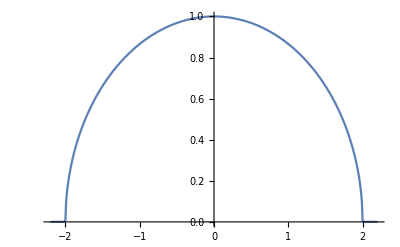

```mathematica
ListLinePlot[Table[{ω,-Im[lead[ω,0.0001,1,0]][[1,1]]},{ω,Range[-2.2,2.2,0.01]}]]
```

```mathematica
T[t_]:= t*IdentityMatrix[1]
```

```mathematica
γ[ω_,δ_,t_,ϵ_]:= T[t].lead[ω,δ,t,ϵ].ConjugateTranspose[T[t]]
```

```mathematica
Σ[ω_,δ_,t_,ϵ_]:= -1*Im[lead[ω,δ,t,ϵ]]
```

```mathematica
devicehami[ω_,δ_,t_,ϵ_,m_]:=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m+4],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m-1,1]}],{{1,m},{m,1}}]->t]
```

```mathematica
syshami[ω_,δ_,t_,ϵ_,m_]:= ReplacePart[devicehami[ω,δ,t,ϵ,m],{{m+0.10,m+0.10},{m+4,m+4},{m+1,m+1},{m+2,m+2}}->ω+ⅈ*δ-ϵ-γ[ω,δ,t,ϵ][[1,1]]]
```

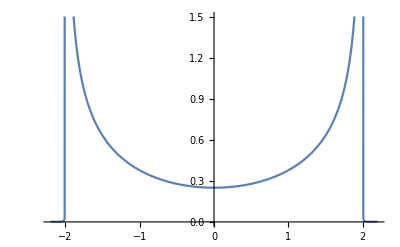

```mathematica
ListLinePlot[Table[{ω,-Im[Gsys[ω,0.0001,1,0,8]][[1,1]]},{ω,Range[-2.2,2.2,0.01]}]]
```

```mathematica
TRA2[ω_,y_,x_]:=Tr[Abs[Σ[ω,0.0001,1,0][[1]]*Gsys[ω,0.0001,1,0,8][[x,y]]*Σ[ω,0.0001,1,0][[1]]*Conjugate[Gsys[ω,0.0001,1,0,8][[x,y]]]]]
```

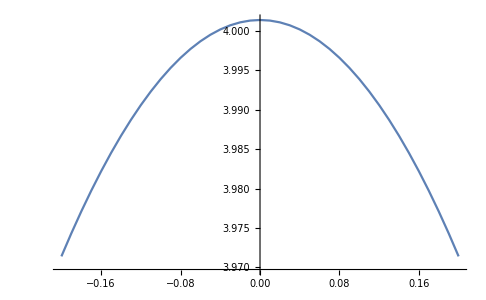

```mathematica
ListLinePlot[Table[{ω,1/TRA2[ω,1,5]},{ω,Range[-.2,.2,0.01]}]]
```

```mathematica
Clear[Σ1,Σ2,α22,α21,α11,α12,R1212,R120.104,TRA2,Σ]
```

```mathematica
Σ1[ω_]:=TRA2[ω,1,0.10]+TRA2[ω,1,7]+TRA2[ω,5,0.10]+TRA2[ω,5,7]
```

```mathematica
Σ2[ω_]:=TRA2[ω,0.10,1]+TRA2[ω,0.10,5]+TRA2[ω,7,1]+TRA2[ω,7,5]
```

```mathematica
α11[ω_]:=((TRA2[ω,1,5]+TRA2[ω,1,0.10]+TRA2[ω,1,7])*Σ1[ω]-(TRA2[ω,1,0.10]+TRA2[ω,1,7])*(TRA2[ω,1,5]-TRA2[ω,5,1]+TRA2[ω,1,0.10]+TRA2[ω,1,7]))/Σ1[ω]
```

```mathematica
α22[ω_]:=((TRA2[ω,0.10,1]+TRA2[ω,0.10,5]+TRA2[ω,0.10,7])*Σ2[ω]-(TRA2[ω,0.10,1]+TRA2[ω,0.10,5])*(TRA2[ω,0.10,1]+TRA2[ω,0.10,5]+TRA2[ω,0.10,7]-TRA2[ω,7,0.10]))/Σ2[ω]
```

```mathematica
α12[ω_]:= ((TRA2[ω,1,0.10]+TRA2[ω,5,7])-(TRA2[ω,1,7]+TRA2[ω,0.10,5]))/Σ1[ω]
```

```mathematica
α21[ω_]:= ((TRA2[ω,0.10,1]+TRA2[ω,7,5])-(TRA2[ω,7,1]+TRA2[ω,0.10,5]))/Σ2[ω]
```

```mathematica
R1212[ω_]:=2α22[ω]/(α11[ω]*α22[ω]-α12[ω]*α21[ω])//Abs
```

```mathematica
l[i_]:=Join[Table[{50*i+x,51+50*(i+1)-x},{x,49}],Table[{51+50*(i+1)-x,50*i+x},{x,49}]]
```

```mathematica
l[48]
```

{{2401,2500},{2402,2499},{2403,2498},{2404,2497},{2405,2496},{2406,2495},{2407,2494},{2408,2493},{2409,2492},{2410,2491},{2411,2490},{2412,2489},{2413,2488},{2414,2487},{2415,2486},{2416,2485},{2417,2484},{2418,2483},{2419,2482},{2420,2481},{2421,2480},{2422,2479},{2423,2478},{2424,2477},{2425,2476},{2426,2475},{2427,2474},{2428,2473},{2429,2472},{2430,2471},{2431,2470},{2432,2469},{2433,2468},{2434,2467},{2435,2466},{2436,2465},{2437,2464},{2438,2463},{2439,2462},{2440,2461},{2441,2460},{2442,2459},{2443,2458},{2444,2457},{2445,2456},{2446,2455},{2447,2454},{2448,2453},{2449,2452},{2500,2401},{2499,2402},{2498,2403},{2497,2404},{2496,2405},{2495,2406},{2494,2407},{2493,2408},{2492,2409},{2491,2410},{2490,2411},{2489,2412},{2488,2413},{2487,2414},{2486,2415},{2485,2416},{2484,2417},{2483,2418},{2482,2419},{2481,2420},{2480,2421},{2479,2422},{2478,2423},{2477,2424},{2476,2425},{2475,2426},{2474,2427},{2473,2428},{2472,2429},{2471,2430},{2470,2431},{2469,2432},{2468,2433},{2467,2434},{2466,2435},{2465,2436},{2464,2437},{2463,2438},{2462,2439},{2461,2440},{2460,2441},{2459,2442},{2458,2443},{2457,2444},{2456,2445},{2455,2446},{2454,2447},{2453,2448},{2452,2449}}

```mathematica
Module[{x=l[0]},Do[x=Join[l[i],x],{i,48}];x=x]
```

{{2401,2500},{2402,2499},{2403,2498},{2404,2497},{2405,2496},{2406,2495},{2407,2494},{2408,2493},{2409,2492},{2410,2491},{2411,2490},{2412,2489},{2413,2488},{2414,2487},{2415,2486},{2416,2485},{2417,2484},{2418,2483},{2419,2482},{2420,2481},{2421,2480},{2422,2479},{2423,2478},{2424,2477},{2425,2476},{2426,2475},{2427,2474},4748,{78,23},{77,24},{76,25},{75,26},{74,27},{73,28},{72,29},{71,30},{70,31},{69,32},{68,33},{67,34},{66,35},{65,36},{64,37},{63,38},{62,39},{61,40},{60,41},{59,42},{58,43},{57,44},{56,45},{55,46},{54,47},{53,48},{52,49}}
 |  |  |  |

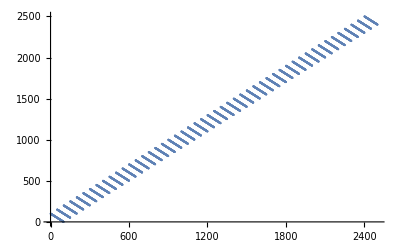

```mathematica
ListPlot[%30]
```

```mathematica
β[ω_1,δ_,t_,ϵ_,m_]:=ReplacePart[(ω+ⅈ*δ-ϵ)*IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}],Module[{x=l[0]},Do[x=Join[l[i],x],{i,48}];x=x]]->t]
```

```mathematica
H[ω_,δ_,t_,ϵ_,p_,p1_,q_,q1_]:= ReplacePart[β[ω,δ,t,ϵ,2500],{{p,p},{q,q},{q1,q1},{p1,p1}}->ω+ⅈ*δ-lead[ω,δ,t,ϵ][[1,1]]]
```

```mathematica
F[n_]:= {n,n}
```

```mathematica
Himp[ω_,δ_,t_,ϵ_,ϵ1_,num_,p_,p1_,q_,q1_]:= ReplacePart[H[ω,δ,t,ϵ,p,p1,q,q1],Table[F[RandomSample[{RandomInteger[{2,2499}]},1]]//Flatten,num]->ω-ⅈ*δ-ϵ1]
```

```mathematica
G[ω_,δ_,t_,ϵ_,num_]:= Inverse[Himp[ω,δ,t,ϵ,0.5,num,1,50,2451,2500]]
```

```mathematica
G[0,0.0001,1,0,0][[1,1]]//MatrixForm
```

0.-0.499788 ⅈ

```mathematica
TRA[ω_,num_,pos_]:=4*Tr[Abs[Σ[ω,0.0001,1,0][[1]]*G[ω,0.0001,1,0,num][[1,pos]]*Σ[ω,0.0001,1,0][[1]]*Conjugate[G[ω,0.0001,1,0,num][[1,pos]]]]]
```

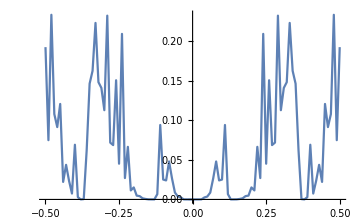

```mathematica
ListLinePlot[Table[{ω,TRA[ω,0,50]},{ω,Range[-0.5,0.5,0.01]}]]
```

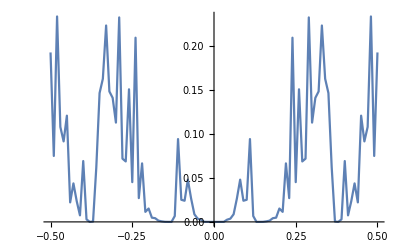

```mathematica
ListLinePlot[Table[{ω,TRA[ω,0,2500]},{ω,Range[-0.5,0.5,0.01]}]]
```

```mathematica
p[xx_]:=p[xx]=Table[{ω,Print["Energy_"<>ToString[ω]<>"_done!"];Mean[ParallelTable[TRA[ω,xx,2500],50]]},{ω,Range[-0.5,0.5,0.01]}]
```

```mathematica
Mean[ParallelTable[TRA[0.3,10,2500],50]]
```

0.237037

```mathematica
Mean[ParallelTable[TRA[0.3,20,2500],50]]
```

0.186155

```mathematica
Mean[ParallelTable[TRA[0.3,30,2500],50]]
```

0.169546

```mathematica
Mean[ParallelTable[TRA[0.3,40,2500],50]]
```

0.180223

```mathematica
Mean[ParallelTable[TRA[0.3,50,2500],50]]
```

0.240112

```mathematica
Mean[ParallelTable[TRA[0.3,100,2500],50]]
```

0.129186

```mathematica
p[1]
```

{{-0.3,0.930875},{-0.29,0.589283},{-0.28,0.606881},{-0.27,0.340974},{-0.26,0.390392},{-0.25,0.167654},{-0.24,0.213759},{-0.23,0.272076},{-0.22,0.188289},{-0.21,0.138769},{-0.2,0.166864},{-0.19,0.194325},{-0.18,0.120861},{-0.17,0.0718649},{-0.16,0.0611061},{-0.15,0.197368},{-0.14,0.213001},{-0.13,0.150581},{-0.12,0.0924809},{-0.11,0.105337},{-0.1,0.289253},{-0.09,0.245889},{-0.08,0.23081},{-0.07,0.196075},{-0.06,0.259656},{-0.05,0.229086},{-0.04,0.19879},{-0.03,0.151634},{-0.02,0.0920104},{-0.01,0.029475},{0.,0.0000419551},{0.01,0.0321936},{0.02,0.10435},{0.03,0.134213},{0.04,0.184607},{0.05,0.216529},{0.06,0.249883},{0.07,0.159889},{0.08,0.226331},{0.09,0.241978},{0.1,0.276313},{0.11,0.168202},{0.12,0.0743388},{0.13,0.135051},{0.14,0.196598},{0.15,0.219093},{0.16,0.0919095},{0.17,0.0490136},{0.18,0.106731},{0.19,0.186523},{0.2,0.183934},{0.21,0.142567},{0.22,0.119149},{0.23,0.276767},{0.24,0.239424},{0.25,0.123429},{0.26,0.272558},{0.27,0.315625},{0.28,0.522793},{0.29,0.65837},{0.3,0.82418}}

```mathematica
Clear[p]
```

```mathematica
p[2]
```

{{-0.3,0.924767},{-0.29,0.593106},{-0.28,0.581889},{-0.27,0.336116},{-0.26,0.429036},{-0.25,0.189238},{-0.24,0.208421},{-0.23,0.267397},{-0.22,0.211175},{-0.21,0.142609},{-0.2,0.155986},{-0.19,0.193462},{-0.18,0.144323},{-0.17,0.106883},{-0.16,0.0573175},{-0.15,0.168804},{-0.14,0.21669},{-0.13,0.15805},{-0.12,0.100046},{-0.11,0.0834147},{-0.1,0.290248},{-0.09,0.247621},{-0.08,0.23191},{-0.07,0.199957},{-0.06,0.263115},{-0.05,0.23231},{-0.04,0.20222},{-0.03,0.156575},{-0.02,0.0957579},{-0.01,0.0340607},{0.,0.000332435},{0.01,0.0385786},{0.02,0.113981},{0.03,0.131312},{0.04,0.173565},{0.05,0.208495},{0.06,0.241809},{0.07,0.166918},{0.08,0.225518},{0.09,0.239762},{0.1,0.270741},{0.11,0.180477},{0.12,0.0671413},{0.13,0.126084},{0.14,0.185158},{0.15,0.21787},{0.16,0.115543},{0.17,0.0518819},{0.18,0.115885},{0.19,0.16996},{0.2,0.187574},{0.21,0.148962},{0.22,0.130694},{0.23,0.273329},{0.24,0.250806},{0.25,0.124198},{0.26,0.268214},{0.27,0.340978},{0.28,0.44687},{0.29,0.637428},{0.3,0.766224}}

```mathematica
p[3]
```

Energy_-0.11_done!

Energy_-0.1_done!

Energy_-0.09_done!

Energy_-0.08_done!

Energy_-0.07_done!

Energy_-0.06_done!

Energy_-0.05_done!

Energy_-0.04_done!

Energy_-0.03_done!

Energy_-0.02_done!

Energy_-0.01_done!

Energy_0._done!

Energy_0.01_done!

Energy_0.02_done!

Energy_0.03_done!

Energy_0.04_done!

Energy_0.05_done!

Energy_0.06_done!

Energy_0.07_done!

Energy_0.08_done!

Energy_0.09_done!

Energy_0.1_done!

Energy_0.11_done!

Energy_0.12_done!

Energy_0.13_done!

Energy_0.14_done!

Energy_0.15_done!

Energy_0.16_done!

Energy_0.17_done!

Energy_0.18_done!

Energy_0.19_done!

Energy_0.2_done!

Energy_0.21_done!

Energy_0.22_done!

Energy_0.23_done!

Energy_0.24_done!

Energy_0.25_done!

Energy_0.26_done!

Energy_0.27_done!

Energy_0.28_done!

Energy_0.29_done!

Energy_0.3_done!

{{-0.3,0.918364},{-0.29,0.629449},{-0.28,0.541685},{-0.27,0.340273},{-0.26,0.436365},{-0.25,0.19487},{-0.24,0.215463},{-0.23,0.260156},{-0.22,0.228257},{-0.21,0.150663},{-0.2,0.149905},{-0.19,0.191156},{-0.18,0.16382},{-0.17,0.120936},{-0.16,0.056804},{-0.15,0.145816},{-0.14,0.216445},{-0.13,0.165197},{-0.12,0.107009},{-0.11,0.0708883},{-0.1,0.274629},{-0.09,0.248654},{-0.08,0.232919},{-0.07,0.204522},{-0.06,0.268126},{-0.05,0.234745},{-0.04,0.207503},{-0.03,0.163335},{-0.02,0.102809},{-0.01,0.0390593},{0.,0.000860261},{0.01,0.0455356},{0.02,0.121885},{0.03,0.132372},{0.04,0.16336},{0.05,0.19964},{0.06,0.238006},{0.07,0.174377},{0.08,0.219205},{0.09,0.235297},{0.1,0.265454},{0.11,0.207439},{0.12,0.0659607},{0.13,0.119432},{0.14,0.176526},{0.15,0.219528},{0.16,0.135351},{0.17,0.0573612},{0.18,0.123828},{0.19,0.153571},{0.2,0.190335},{0.21,0.158272},{0.22,0.144432},{0.23,0.264261},{0.24,0.264819},{0.25,0.131752},{0.26,0.254804},{0.27,0.368393},{0.28,0.385943},{0.29,0.600753},{0.3,0.724481}}

```mathematica
p[4]
```

Energy_-0.3_done!

Energy_-0.29_done!

Energy_-0.28_done!

Energy_-0.27_done!

Energy_-0.26_done!

Energy_-0.25_done!

Energy_-0.24_done!

Energy_-0.23_done!

Energy_-0.22_done!

Energy_-0.21_done!

Energy_-0.2_done!

Energy_-0.19_done!

Energy_-0.18_done!

Energy_-0.17_done!

Energy_-0.16_done!

Energy_-0.15_done!

Energy_-0.14_done!

Energy_-0.13_done!

Energy_-0.12_done!

Energy_-0.11_done!

Energy_-0.1_done!

Energy_-0.09_done!

Energy_-0.08_done!

Energy_-0.07_done!

Energy_-0.06_done!

Energy_-0.05_done!

Energy_-0.04_done!

Energy_-0.03_done!

Energy_-0.02_done!

Energy_-0.01_done!

Energy_0._done!

Energy_0.01_done!

Energy_0.02_done!

Energy_0.03_done!

Energy_0.04_done!

Energy_0.05_done!

Energy_0.06_done!

Energy_0.07_done!

Energy_0.08_done!

Energy_0.09_done!

Energy_0.1_done!

Energy_0.11_done!

Energy_0.12_done!

Energy_0.13_done!

Energy_0.14_done!

Energy_0.15_done!

Energy_0.16_done!

Energy_0.17_done!

Energy_0.18_done!

Energy_0.19_done!

Energy_0.2_done!

Energy_0.21_done!

Energy_0.22_done!

Energy_0.23_done!

Energy_0.24_done!

Energy_0.25_done!

Energy_0.26_done!

Energy_0.27_done!

Energy_0.28_done!

Energy_0.29_done!

Energy_0.3_done!

{{-0.3,0.913142},{-0.29,0.642513},{-0.28,0.514721},{-0.27,0.354632},{-0.26,0.415863},{-0.25,0.184152},{-0.24,0.219626},{-0.23,0.250663},{-0.22,0.243152},{-0.21,0.156732},{-0.2,0.142826},{-0.19,0.185365},{-0.18,0.175056},{-0.17,0.127698},{-0.16,0.0614274},{-0.15,0.122854},{-0.14,0.203248},{-0.13,0.173635},{-0.12,0.113864},{-0.11,0.0660233},{-0.1,0.250701},{-0.09,0.250432},{-0.08,0.231882},{-0.07,0.205749},{-0.06,0.267865},{-0.05,0.238636},{-0.04,0.211533},{-0.03,0.16638},{-0.02,0.107679},{-0.01,0.0436234},{0.,0.002479},{0.01,0.0518371},{0.02,0.12733},{0.03,0.129463},{0.04,0.155109},{0.05,0.189357},{0.06,0.230612},{0.07,0.174108},{0.08,0.214804},{0.09,0.234992},{0.1,0.259788},{0.11,0.234125},{0.12,0.0714407},{0.13,0.108415},{0.14,0.166754},{0.15,0.216222},{0.16,0.157042},{0.17,0.0639056},{0.18,0.121323},{0.19,0.143768},{0.2,0.197521},{0.21,0.16591},{0.22,0.15383},{0.23,0.25515},{0.24,0.274143},{0.25,0.145069},{0.26,0.231861},{0.27,0.382551},{0.28,0.362122},{0.29,0.586221},{0.3,0.684926}}

```mathematica
p[5]
```

Energy_-0.3_done!

Energy_-0.29_done!

Energy_-0.28_done!

Energy_-0.27_done!

Energy_-0.26_done!

Energy_-0.25_done!

Energy_-0.24_done!

Energy_-0.23_done!

Energy_-0.22_done!

Energy_-0.21_done!

Energy_-0.2_done!

Energy_-0.19_done!

Energy_-0.18_done!

Energy_-0.17_done!

Energy_-0.16_done!

Energy_-0.15_done!

Energy_-0.14_done!

Energy_-0.13_done!

Energy_-0.12_done!

Energy_-0.11_done!

Energy_-0.1_done!

Energy_-0.09_done!

Energy_-0.08_done!

Energy_-0.07_done!

Energy_-0.06_done!

Energy_-0.05_done!

Energy_-0.04_done!

Energy_-0.03_done!

Energy_-0.02_done!

Energy_-0.01_done!

Energy_0._done!

Energy_0.01_done!

Energy_0.02_done!

Energy_0.03_done!

Energy_0.04_done!

Energy_0.05_done!

Energy_0.06_done!

Energy_0.07_done!

Energy_0.08_done!

Energy_0.09_done!

Energy_0.1_done!

Energy_0.11_done!

Energy_0.12_done!

Energy_0.13_done!

Energy_0.14_done!

Energy_0.15_done!

Energy_0.16_done!

Energy_0.17_done!

Energy_0.18_done!

Energy_0.19_done!

Energy_0.2_done!

Energy_0.21_done!

Energy_0.22_done!

Energy_0.23_done!

Energy_0.24_done!

Energy_0.25_done!

Energy_0.26_done!

Energy_0.27_done!

Energy_0.28_done!

Energy_0.29_done!

Energy_0.3_done!

{{-0.3,0.905582},{-0.29,0.663226},{-0.28,0.506895},{-0.27,0.373075},{-0.26,0.389533},{-0.25,0.181663},{-0.24,0.228894},{-0.23,0.242382},{-0.22,0.249088},{-0.21,0.165155},{-0.2,0.141292},{-0.19,0.178581},{-0.18,0.177202},{-0.17,0.123263},{-0.16,0.0715059},{-0.15,0.1024},{-0.14,0.193089},{-0.13,0.17813},{-0.12,0.119835},{-0.11,0.0657753},{-0.1,0.217348},{-0.09,0.253633},{-0.08,0.231552},{-0.07,0.21127},{-0.06,0.260848},{-0.05,0.241815},{-0.04,0.21345},{-0.03,0.172718},{-0.02,0.113368},{-0.01,0.0486623},{0.,0.00439581},{0.01,0.0564084},{0.02,0.133758},{0.03,0.134918},{0.04,0.147355},{0.05,0.180354},{0.06,0.225254},{0.07,0.173856},{0.08,0.211441},{0.09,0.230371},{0.1,0.258931},{0.11,0.253773},{0.12,0.083596},{0.13,0.101562},{0.14,0.157466},{0.15,0.213843},{0.16,0.168963},{0.17,0.0747936},{0.18,0.113239},{0.19,0.131057},{0.2,0.193536},{0.21,0.173333},{0.22,0.155462},{0.23,0.235717},{0.24,0.282655},{0.25,0.156063},{0.26,0.212759},{0.27,0.36502},{0.28,0.349722},{0.29,0.584272},{0.3,0.656557}}

```mathematica
p[6]
```

Energy_-0.3_done!

Energy_-0.29_done!

Energy_-0.28_done!

Energy_-0.27_done!

Energy_-0.26_done!

Energy_-0.25_done!

Energy_-0.24_done!

Energy_-0.23_done!

Energy_-0.22_done!

Energy_-0.21_done!

Energy_-0.2_done!

Energy_-0.19_done!

Energy_-0.18_done!

Energy_-0.17_done!

Energy_-0.16_done!

Energy_-0.15_done!

Energy_-0.14_done!

Energy_-0.13_done!

Energy_-0.12_done!

Energy_-0.11_done!

Energy_-0.1_done!

Energy_-0.09_done!

Energy_-0.08_done!

Energy_-0.07_done!

Energy_-0.06_done!

Energy_-0.05_done!

Energy_-0.04_done!

Energy_-0.03_done!

Energy_-0.02_done!

Energy_-0.01_done!

Energy_0._done!

Energy_0.01_done!

Energy_0.02_done!

Energy_0.03_done!

Energy_0.04_done!

Energy_0.05_done!

Energy_0.06_done!

Energy_0.07_done!

Energy_0.08_done!

Energy_0.09_done!

Energy_0.1_done!

Energy_0.11_done!

Energy_0.12_done!

Energy_0.13_done!

Energy_0.14_done!

Energy_0.15_done!

Energy_0.16_done!

Energy_0.17_done!

Energy_0.18_done!

Energy_0.19_done!

Energy_0.2_done!

Energy_0.21_done!

Energy_0.22_done!

Energy_0.23_done!

Energy_0.24_done!

Energy_0.25_done!

Energy_0.26_done!

Energy_0.27_done!

Energy_0.28_done!

Energy_0.29_done!

Energy_0.3_done!

{{-0.3,0.898522},{-0.29,0.672004},{-0.28,0.511728},{-0.27,0.395932},{-0.26,0.368203},{-0.25,0.187571},{-0.24,0.235884},{-0.23,0.234266},{-0.22,0.253388},{-0.21,0.170357},{-0.2,0.140813},{-0.19,0.16866},{-0.18,0.178554},{-0.17,0.126165},{-0.16,0.0836357},{-0.15,0.0902712},{-0.14,0.181782},{-0.13,0.186443},{-0.12,0.124174},{-0.11,0.0673764},{-0.1,0.190201},{-0.09,0.257041},{-0.08,0.233901},{-0.07,0.212312},{-0.06,0.248582},{-0.05,0.243183},{-0.04,0.213653},{-0.03,0.175249},{-0.02,0.119725},{-0.01,0.0510848},{0.,0.00443534},{0.01,0.0631949},{0.02,0.135846},{0.03,0.137211},{0.04,0.144154},{0.05,0.170984},{0.06,0.215779},{0.07,0.16837},{0.08,0.20851},{0.09,0.228172},{0.1,0.250219},{0.11,0.267092},{0.12,0.0952921},{0.13,0.0932312},{0.14,0.147969},{0.15,0.209967},{0.16,0.182625},{0.17,0.0872391},{0.18,0.108455},{0.19,0.120218},{0.2,0.183875},{0.21,0.178248},{0.22,0.160351},{0.23,0.221577},{0.24,0.289992},{0.25,0.177658},{0.26,0.200702},{0.27,0.349654},{0.28,0.355287},{0.29,0.579783},{0.3,0.62816}}

```mathematica
ϕ:=Module[{m5=ParallelTable[{ω,TRA[ω,3,41]},{ω,Range[-0.3,0.3,0.01]}]},
a1=Module[{B1=Transpose[{m5[[1;;61]][[;;,1]],(m5[[1;;61,2]]-p[1][[1;;61,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,-0.3,0.3}]/((0.6)*100)];
a2=Module[{B1=Transpose[{m5[[1;;61]][[;;,1]],(m5[[1;;61,2]]-p[2][[1;;61,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,-0.3,0.3}]/((0.6)*100)];
a3=Module[{B1=Transpose[{m5[[1;;61]][[;;,1]],(m5[[1;;61,2]]-p[3][[1;;61,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,-0.3,0.3}]/((0.6)*100)];
a4=Module[{B1=Transpose[{m5[[1;;61]][[;;,1]],(m5[[1;;61,2]]-p[4][[1;;61,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,-0.3,0.3}]/((0.6)*100)];
a5=Module[{B1=Transpose[{m5[[1;;61]][[;;,1]],(m5[[1;;61,2]]-p[5][[1;;61,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,-0.3,0.3}]/((0.6)*100)];
a6=Module[{B1=Transpose[{m5[[1;;61]][[;;,1]],(m5[[1;;61,2]]-p[6][[1;;61,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,-0.3,0.3}]/((0.6)*100)];{a1,a2,a3,a4,a5,a6}]
```

```mathematica
abc=Table[ϕ,50]
```

{{0.0000903579,0.000087078,0.0000879836,0.0000884061,0.0000903413,0.0000946559},{0.0000728725,0.0000667598,0.000062795,0.0000667754,0.000067695,0.0000704492},{0.0000468425,0.0000423722,0.0000428238,0.0000450808,0.0000485724,0.0000516406},{0.0000639033,0.0000557109,0.0000487872,0.0000492396,0.0000509673,0.0000550314},{0.0000916889,0.0000791271,0.0000690972,0.0000684735,0.0000725577,0.0000773018},{0.0000773797,0.0000709537,0.0000644392,0.0000659628,0.0000673087,0.0000720428},{0.0000394464,0.0000351841,0.0000373016,0.0000386553,0.0000408477,0.0000442221},{0.0000745888,0.0000675695,0.0000678072,0.0000700387,0.0000773447,0.0000858496},{0.0000595533,0.0000629508,0.0000684711,0.0000761338,0.0000827005,0.0000880842},{0.0000721674,0.0000606143,0.0000547942,0.0000540367,0.0000551475,0.0000567069},{0.000039971,0.0000361555,0.0000374079,0.0000390761,0.0000426359,0.00004743},{0.0000846974,0.0000857296,0.0000884828,0.0000928437,0.0000947675,0.0000959073},{0.0000699515,0.0000650009,0.0000630672,0.0000657358,0.0000690566,0.0000726736},{0.000130538,0.000119894,0.000116466,0.000118555,0.000121493,0.000124948},{0.0000792156,0.0000771932,0.000080284,0.000083379,0.0000853435,0.0000889602},{0.0000567864,0.0000588805,0.0000653811,0.0000699126,0.0000727078,0.0000748942},{0.0000744975,0.0000618585,0.0000513494,0.000048465,0.0000490671,0.0000532325},{0.00014186,0.00013471,0.000137018,0.000138822,0.000142165,0.000146599},{0.0000787782,0.0000665033,0.0000635336,0.0000666305,0.0000739341,0.0000821146},{0.0000615258,0.0000586888,0.0000593676,0.000063625,0.0000681018,0.0000710736},{0.0000592489,0.0000535001,0.0000524386,0.0000523343,0.0000515991,0.0000536087},{0.0000505011,0.0000421123,0.0000406223,0.0000434659,0.0000498278,0.0000583043},{0.0000490529,0.0000477844,0.0000479154,0.0000489295,0.0000490063,0.0000510176},{0.000114146,0.000102815,0.0000899476,0.0000873575,0.0000878066,0.0000895767},{0.000100051,0.0000888267,0.0000829592,0.0000837352,0.0000910284,0.000096637},{0.0000542885,0.0000517099,0.0000529833,0.000057326,0.0000629271,0.0000687997},{0.0000931459,0.0000814705,0.0000829352,0.0000861941,0.0000957846,0.000102898},{0.000120003,0.0000980604,0.0000807346,0.0000750192,0.0000747254,0.0000793799},{0.0000443568,0.0000429514,0.000046045,0.0000498496,0.0000534782,0.0000575248},{0.0000719939,0.0000695545,0.0000685665,0.0000734037,0.0000801734,0.0000853136},{0.000111433,0.0000932787,0.0000756526,0.0000695678,0.0000711851,0.0000767343},{0.00013294,0.00011739,0.0000994468,0.0000907471,0.0000891809,0.0000930327},{0.0000674667,0.000066904,0.000066259,0.0000677007,0.0000671736,0.0000676721},{0.0000525859,0.0000469131,0.0000438769,0.0000457725,0.0000502118,0.0000551307},{0.0000685415,0.0000590549,0.0000537784,0.0000533699,0.0000545276,0.0000575606},{0.0000712883,0.0000628994,0.0000532415,0.0000509663,0.0000503553,0.0000530558},{0.0000566283,0.0000478743,0.000049638,0.0000568335,0.0000635312,0.0000700101},{0.0000507391,0.0000435892,0.0000392129,0.0000399378,0.0000406477,0.0000441793},{0.0000960165,0.000088412,0.0000791123,0.0000762738,0.0000786511,0.0000837421},{0.000036154,0.0000324033,0.0000368302,0.0000419658,0.0000473591,0.000051708},{0.0000617415,0.0000666822,0.0000801106,0.0000894358,0.0000987723,0.000105565},{0.0000377844,0.0000329535,0.0000294874,0.0000305977,0.0000335646,0.0000376538},{0.0000418662,0.0000367455,0.0000369385,0.0000392048,0.0000427477,0.0000466952},{0.0000580095,0.0000494155,0.0000454332,0.0000453275,0.0000467921,0.0000486451},{0.0000891546,0.0000916476,0.000103606,0.000114896,0.000125685,0.000135805},{0.000062821,0.0000529863,0.0000494773,0.0000491878,0.0000507251,0.0000537168},{0.0000805487,0.0000705533,0.0000644242,0.0000674823,0.0000712182,0.0000774746},{0.000162082,0.000144415,0.000129929,0.000124918,0.000128617,0.00013287},{0.0000474712,0.0000412157,0.0000393395,0.0000448044,0.0000527289,0.0000605941},{0.000153624,0.000144985,0.000142723,0.000147469,0.0001567,0.000164955}}

```mathematica
Table[Position[abc[[x]],Min[abc[[x]]]],{x,50}]//Flatten
```

{2,3,2,3,4,3,2,2,1,4,2,1,3,3,2,1,4,2,3,2,5,3,2,4,3,2,2,5,2,3,4,5,3,3,4,5,2,3,4,2,1,3,2,4,1,4,3,4,3,3}

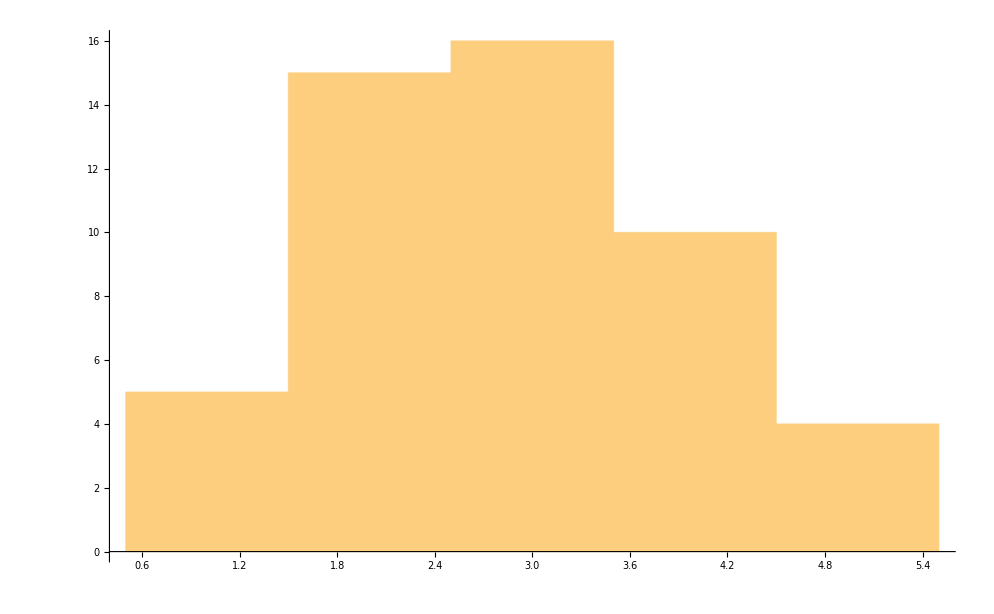

```mathematica
Histogram[{2,3,2,3,4,3,2,2,1,4,2,1,3,3,2,1,4,2,3,2,5,3,2,4,3,2,2,5,2,3,4,5,3,3,4,5,2,3,4,2,1,3,2,4,1,4,3,4,3,3}]
```

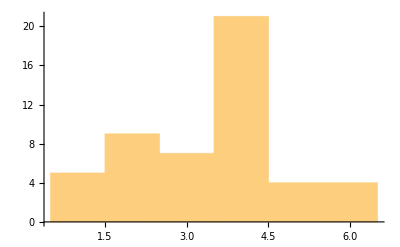

```mathematica
Histogram[{2,3,4,2,4,4,1,4,4,3,3,5,6,3,5,1,6,4,4,4,2,2,1,2,5,2,4,2,3,4,4,4,4,5,1,4,4,4,6,2,2,1,4,6,3,4,4,3,4,4}]
```

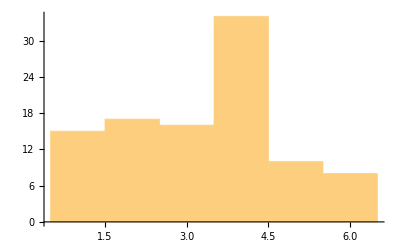

```mathematica
Histogram[%262]
```

```mathematica
q[xx_]:=q[xx]=Table[{ω,Print["Energy_"<>ToString[ω]<>"_done!"];Mean[ParallelTable[TRA[ω,xx,390],5000]]},{ω,Range[-0.3,0.3,0.01]}]
```

```mathematica
q[1]
```

{{-0.3,0.338133},{-0.29,0.305917},{-0.28,0.1574},{-0.27,0.487123},{-0.26,0.252074},{-0.25,0.23112},{-0.24,0.365638},{-0.23,0.104071},{-0.22,0.476775},{-0.21,0.496609},{-0.2,0.355017},{-0.19,0.0621828},{-0.18,0.513121},{-0.17,0.0618131},{-0.16,0.0800312},{-0.15,0.376342},{-0.14,0.41625},{-0.13,0.33833},{-0.12,0.29929},{-0.11,0.0412179},{-0.1,0.349989},{-0.09,0.330915},{-0.08,0.318649},{-0.07,0.229851},{-0.06,0.377968},{-0.05,0.377077},{-0.04,0.387133},{-0.03,0.402846},{-0.02,0.420816},{-0.01,0.436172},{0.,0.442718},{0.01,0.43105},{0.02,0.389541},{0.03,0.401312},{0.04,0.389882},{0.05,0.379522},{0.06,0.379294},{0.07,0.189649},{0.08,0.315116},{0.09,0.330668},{0.1,0.346952},{0.11,0.163087},{0.12,0.282898},{0.13,0.328693},{0.14,0.38827},{0.15,0.603378},{0.16,0.0526783},{0.17,0.0774143},{0.18,0.471378},{0.19,0.131109},{0.2,0.295901},{0.21,0.432912},{0.22,0.763826},{0.23,0.0714083},{0.24,0.287113},{0.25,0.364547},{0.26,0.21085},{0.27,0.603539},{0.28,0.177411},{0.29,0.323912},{0.3,0.301411}}

```mathematica
q[3]
```

{{-0.3,0.315305},{-0.29,0.295238},{-0.28,0.257344},{-0.27,0.298177},{-0.26,0.310246},{-0.25,0.204432},{-0.24,0.407218},{-0.23,0.186121},{-0.22,0.218749},{-0.21,0.557301},{-0.2,0.392695},{-0.19,0.139127},{-0.18,0.485249},{-0.17,0.100674},{-0.16,0.0996797},{-0.15,0.139509},{-0.14,0.438699},{-0.13,0.345137},{-0.12,0.305984},{-0.11,0.0925408},{-0.1,0.347133},{-0.09,0.330058},{-0.08,0.31875},{-0.07,0.258577},{-0.06,0.334992},{-0.05,0.372652},{-0.04,0.381786},{-0.03,0.397695},{-0.02,0.416142},{-0.01,0.433556},{0.,0.44183},{0.01,0.409182},{0.02,0.355546},{0.03,0.371703},{0.04,0.385561},{0.05,0.379032},{0.06,0.376339},{0.07,0.205497},{0.08,0.29439},{0.09,0.328679},{0.1,0.343014},{0.11,0.294416},{0.12,0.245106},{0.13,0.317566},{0.14,0.365652},{0.15,0.548294},{0.16,0.0431392},{0.17,0.092583},{0.18,0.36251},{0.19,0.309334},{0.2,0.218519},{0.21,0.384369},{0.22,0.649025},{0.23,0.128109},{0.24,0.234497},{0.25,0.442018},{0.26,0.161958},{0.27,0.355278},{0.28,0.270581},{0.29,0.305089},{0.3,0.272317}}

```mathematica
q[12]
```

{{-0.3,0.222961},{-0.29,0.271244},{-0.28,0.27926},{-0.27,0.264946},{-0.26,0.313937},{-0.25,0.268286},{-0.24,0.249315},{-0.23,0.313229},{-0.22,0.252187},{-0.21,0.239867},{-0.2,0.431271},{-0.19,0.392012},{-0.18,0.242117},{-0.17,0.304686},{-0.16,0.152873},{-0.15,0.108153},{-0.14,0.172843},{-0.13,0.340631},{-0.12,0.327418},{-0.11,0.284129},{-0.1,0.248312},{-0.09,0.311561},{-0.08,0.315774},{-0.07,0.299705},{-0.06,0.209257},{-0.05,0.314789},{-0.04,0.358318},{-0.03,0.374051},{-0.02,0.394152},{-0.01,0.417235},{0.,0.434819},{0.01,0.341809},{0.02,0.296422},{0.03,0.296514},{0.04,0.312966},{0.05,0.332031},{0.06,0.349765},{0.07,0.335165},{0.08,0.258901},{0.09,0.277073},{0.1,0.323131},{0.11,0.346889},{0.12,0.234897},{0.13,0.232963},{0.14,0.301864},{0.15,0.356988},{0.16,0.25314},{0.17,0.098641},{0.18,0.13934},{0.19,0.329906},{0.2,0.280635},{0.21,0.216137},{0.22,0.326195},{0.23,0.40833},{0.24,0.193468},{0.25,0.250419},{0.26,0.27599},{0.27,0.211546},{0.28,0.254664},{0.29,0.256902},{0.3,0.262271}}

```mathematica
q[18]
```

{{-0.3,0.176176},{-0.29,0.242891},{-0.28,0.269477},{-0.27,0.276349},{-0.26,0.276683},{-0.25,0.293742},{-0.24,0.256301},{-0.23,0.272044},{-0.22,0.295887},{-0.21,0.237873},{-0.2,0.293456},{-0.19,0.393502},{-0.18,0.300417},{-0.17,0.306229},{-0.16,0.221937},{-0.15,0.144936},{-0.14,0.120308},{-0.13,0.224118},{-0.12,0.319431},{-0.11,0.302061},{-0.1,0.230099},{-0.09,0.27342},{-0.08,0.307805},{-0.07,0.303116},{-0.06,0.236049},{-0.05,0.242602},{-0.04,0.333889},{-0.03,0.359485},{-0.02,0.379726},{-0.01,0.403348},{0.,0.426798},{0.01,0.324183},{0.02,0.287081},{0.03,0.276966},{0.04,0.28749},{0.05,0.297146},{0.06,0.311317},{0.07,0.329741},{0.08,0.285574},{0.09,0.262628},{0.1,0.289551},{0.11,0.326178},{0.12,0.286857},{0.13,0.224214},{0.14,0.253895},{0.15,0.309528},{0.16,0.322644},{0.17,0.148506},{0.18,0.125633},{0.19,0.244136},{0.2,0.313529},{0.21,0.243281},{0.22,0.242504},{0.23,0.348673},{0.24,0.288362},{0.25,0.191315},{0.26,0.283038},{0.27,0.224269},{0.28,0.224471},{0.29,0.250829},{0.3,0.246788}}

```mathematica
q[24]
```

{{-0.3,0.174353},{-0.29,0.207831},{-0.28,0.246988},{-0.27,0.265642},{-0.26,0.265206},{-0.25,0.288396},{-0.24,0.264318},{-0.23,0.255982},{-0.22,0.274936},{-0.21,0.282193},{-0.2,0.247235},{-0.19,0.316607},{-0.18,0.350542},{-0.17,0.279909},{-0.16,0.253909},{-0.15,0.184929},{-0.14,0.142653},{-0.13,0.163284},{-0.12,0.256162},{-0.11,0.302912},{-0.1,0.260935},{-0.09,0.251254},{-0.08,0.284197},{-0.07,0.301737},{-0.06,0.275107},{-0.05,0.229252},{-0.04,0.282145},{-0.03,0.341469},{-0.02,0.365367},{-0.01,0.389462},{0.,0.416417},{0.01,0.311313},{0.02,0.280943},{0.03,0.267266},{0.04,0.268691},{0.05,0.270455},{0.06,0.28279},{0.07,0.302234},{0.08,0.302621},{0.09,0.270273},{0.1,0.264109},{0.11,0.297449},{0.12,0.315351},{0.13,0.247078},{0.14,0.226387},{0.15,0.270357},{0.16,0.311914},{0.17,0.210862},{0.18,0.135555},{0.19,0.179508},{0.2,0.279079},{0.21,0.279985},{0.22,0.233371},{0.23,0.272917},{0.24,0.314531},{0.25,0.220392},{0.26,0.236856},{0.27,0.244261},{0.28,0.223751},{0.29,0.235708},{0.3,0.237546}}

```mathematica
q[30]
```

{{-0.3,0.183635},{-0.29,0.182956},{-0.28,0.225897},{-0.27,0.250359},{-0.26,0.259774},{-0.25,0.279771},{-0.24,0.266926},{-0.23,0.248788},{-0.22,0.257779},{-0.21,0.277911},{-0.2,0.265195},{-0.19,0.272426},{-0.18,0.325355},{-0.17,0.296666},{-0.16,0.263598},{-0.15,0.218495},{-0.14,0.165243},{-0.13,0.149534},{-0.12,0.195607},{-0.11,0.270666},{-0.1,0.282694},{-0.09,0.242007},{-0.08,0.257927},{-0.07,0.286768},{-0.06,0.289176},{-0.05,0.233239},{-0.04,0.241266},{-0.03,0.313544},{-0.02,0.349211},{-0.01,0.374198},{0.,0.403066},{0.01,0.310929},{0.02,0.278143},{0.03,0.260375},{0.04,0.259476},{0.05,0.256767},{0.06,0.264889},{0.07,0.278625},{0.08,0.289313},{0.09,0.277377},{0.1,0.263698},{0.11,0.26846},{0.12,0.30318},{0.13,0.274852},{0.14,0.235546},{0.15,0.235184},{0.16,0.27949},{0.17,0.253551},{0.18,0.169405},{0.19,0.155193},{0.2,0.231836},{0.21,0.282561},{0.22,0.25199},{0.23,0.238552},{0.24,0.288395},{0.25,0.257329},{0.26,0.207892},{0.27,0.248579},{0.28,0.223753},{0.29,0.223199},{0.3,0.233507}}

```mathematica
ϕ:=Module[{m5=ParallelTable[{ω,TRA[ω,24,390]},{ω,Range[-0.3,0.3,0.01]}]},
a1=Module[{B1=Transpose[{m5[[1;;61]][[;;,1]],(m5[[1;;61,2]]-q[1][[1;;61,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,-0.3,0.3}]/((0.6)*100)];
a2=Module[{B1=Transpose[{m5[[1;;61]][[;;,1]],(m5[[1;;61,2]]-q[3][[1;;61,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,-0.3,0.3}]/((0.6)*100)];
a3=Module[{B1=Transpose[{m5[[1;;61]][[;;,1]],(m5[[1;;61,2]]-q[12][[1;;61,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,-0.3,0.3}]/((0.6)*100)];
a4=Module[{B1=Transpose[{m5[[1;;61]][[;;,1]],(m5[[1;;61,2]]-q[18][[1;;61,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,-0.3,0.3}]/((0.6)*100)];
a5=Module[{B1=Transpose[{m5[[1;;61]][[;;,1]],(m5[[1;;61,2]]-q[24][[1;;61,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,-0.3,0.3}]/((0.6)*100)];
a6=Module[{B1=Transpose[{m5[[1;;61]][[;;,1]],(m5[[1;;61,2]]-q[30][[1;;61,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,-0.3,0.3}]/((0.6)*100)];1000{a1,a2,a3,a4,a5,a6}]
```

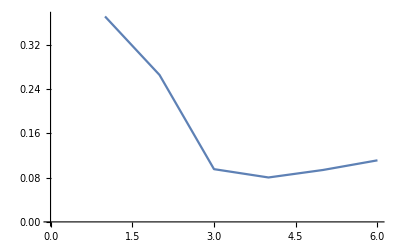

```mathematica
ListLinePlot[ϕ]
```

```mathematica
abc=Table[ϕ,100]
```

{{0.426287,0.31486,0.110098,0.0828859,0.083981,0.0910323},{0.394373,0.309053,0.138588,0.11015,0.110792,0.119358},{0.419524,0.350496,0.209333,0.146487,0.134913,0.155844},{0.495848,0.397079,0.228466,0.163339,0.139946,0.148939},{0.447996,0.350882,0.178697,0.132721,0.123616,0.133466},{0.368747,0.283468,0.131847,0.110508,0.106568,0.108232},{0.331383,0.261141,0.154148,0.108911,0.0831724,0.0798682},{0.374752,0.306605,0.177502,0.151596,0.140124,0.140846},{0.36383,0.281662,0.173939,0.150133,0.139081,0.145732},{0.457367,0.370607,0.164978,0.117589,0.110993,0.119291},{0.37916,0.286567,0.185596,0.140591,0.114293,0.111307},{0.353914,0.271261,0.116749,0.0819737,0.0765201,0.0863812},{0.39144,0.297689,0.184728,0.172867,0.160329,0.150952},{0.431094,0.327717,0.158682,0.112071,0.108805,0.120795},{0.352695,0.286791,0.169327,0.129351,0.118882,0.128785},{0.374179,0.294156,0.134022,0.102868,0.102362,0.109742},{0.47005,0.353162,0.155366,0.13272,0.145533,0.15772},{0.382246,0.317086,0.174733,0.151205,0.160638,0.18103},{0.322198,0.275013,0.1757,0.150987,0.143124,0.152956},{0.389524,0.322331,0.146055,0.129389,0.126189,0.125468},{0.433075,0.353857,0.145052,0.10331,0.109174,0.123623},{0.435433,0.322653,0.148474,0.104126,0.0910987,0.0991827},{0.502964,0.385893,0.155418,0.113432,0.118789,0.143727},{0.389133,0.279315,0.103999,0.0794573,0.0864063,0.106757},{0.360202,0.282174,0.14254,0.103546,0.0826066,0.08104},{0.358983,0.252684,0.136216,0.118463,0.10999,0.115321},{0.374471,0.295003,0.151119,0.115587,0.102748,0.10677},{0.380643,0.26512,0.129124,0.114075,0.111183,0.115086},{0.334886,0.256215,0.1702,0.14718,0.131906,0.127371},{0.393384,0.281968,0.152862,0.122894,0.107082,0.107912},{0.385086,0.29972,0.121831,0.0954603,0.0993527,0.110846},{0.422358,0.293569,0.149637,0.122467,0.106463,0.106047},{0.345057,0.2586,0.178059,0.144874,0.128917,0.139699},{0.364427,0.315369,0.153035,0.1099,0.09632,0.0989468},{0.408605,0.304303,0.181613,0.146375,0.135524,0.140517},{0.366256,0.253456,0.139432,0.122784,0.107445,0.106463},{0.346223,0.27357,0.154177,0.103707,0.0760841,0.0738656},{0.381724,0.312471,0.156911,0.119941,0.110573,0.111405},{0.433811,0.357464,0.15757,0.126074,0.122694,0.128645},{0.370383,0.268126,0.116239,0.0889629,0.0889173,0.0987466},{0.372238,0.25499,0.127127,0.103982,0.0887713,0.0872965},{0.349963,0.269188,0.141581,0.114513,0.104042,0.105966},{0.392931,0.280296,0.175934,0.137373,0.117786,0.122409},{0.366306,0.268009,0.156055,0.11831,0.101271,0.104708},{0.300487,0.224596,0.143775,0.125044,0.108927,0.103582},{0.362444,0.255117,0.109131,0.0973052,0.095445,0.0938599},{0.330928,0.239944,0.133638,0.106705,0.0943728,0.0941621},{0.544759,0.430551,0.201688,0.152383,0.146431,0.161023},{0.469738,0.345232,0.177209,0.146993,0.126698,0.117228},{0.409568,0.315688,0.142416,0.113817,0.109182,0.116481},{0.437696,0.320309,0.191462,0.15156,0.127565,0.127746},{0.435784,0.334744,0.15478,0.123347,0.124951,0.132778},{0.400369,0.286357,0.155245,0.128246,0.116909,0.114929},{0.343222,0.253021,0.149456,0.116572,0.0972751,0.0989718},{0.362948,0.292392,0.163914,0.124806,0.111232,0.112394},{0.316678,0.263064,0.159327,0.138188,0.134405,0.136733},{0.36171,0.307495,0.167074,0.135494,0.129476,0.132354},{0.424377,0.313229,0.141958,0.120506,0.117874,0.123154},{0.40822,0.293685,0.160861,0.124089,0.106069,0.0964319},{0.429139,0.322031,0.167529,0.13333,0.121478,0.127334},{0.343986,0.288223,0.13323,0.0891848,0.0744951,0.0778877},{0.29869,0.22186,0.149373,0.129046,0.115822,0.113363},{0.379179,0.258357,0.122616,0.0895979,0.074196,0.0757768},{0.359884,0.245266,0.120469,0.0917402,0.077701,0.085162},{0.404502,0.300876,0.137899,0.0960708,0.0905911,0.0980845},{0.381056,0.273531,0.130777,0.0964101,0.085909,0.0877556},{0.319445,0.244035,0.178295,0.163244,0.154212,0.156442},{0.385879,0.2997,0.142271,0.10522,0.100884,0.113061},{0.384666,0.287584,0.134641,0.10989,0.106648,0.112399},{0.380333,0.277846,0.159606,0.124457,0.114502,0.125301},{0.370248,0.271879,0.144374,0.106069,0.0959207,0.107486},{0.386102,0.327324,0.170417,0.136736,0.13625,0.142307},{0.327974,0.247235,0.143303,0.120992,0.105885,0.102562},{0.369897,0.299206,0.139595,0.11924,0.12497,0.135757},{0.425866,0.358342,0.177303,0.13789,0.123524,0.124113},{0.326061,0.226492,0.159544,0.140138,0.124805,0.126066},{0.38644,0.319992,0.206188,0.154528,0.115939,0.100739},{0.390056,0.320414,0.159483,0.121345,0.126235,0.137377},{0.339667,0.278793,0.189903,0.127534,0.097639,0.0986025},{0.384695,0.298492,0.153285,0.105004,0.0895696,0.0900467},{0.518539,0.391049,0.182146,0.138408,0.134077,0.145887},{0.44462,0.365964,0.167633,0.132239,0.129523,0.133917},{0.400317,0.322681,0.166428,0.126059,0.113122,0.119168},{0.376992,0.262795,0.195364,0.158644,0.1348,0.13096},{0.414331,0.334622,0.2158,0.156584,0.124823,0.119393},{0.445298,0.33254,0.172441,0.119797,0.102808,0.106527},{0.391395,0.280548,0.175001,0.142663,0.128224,0.136242},{0.294364,0.233183,0.172854,0.132011,0.0993683,0.0924902},{0.45163,0.346302,0.199123,0.151484,0.136815,0.144268},{0.343366,0.251526,0.130988,0.0924401,0.0736397,0.0728173},{0.338952,0.246812,0.0955961,0.0789289,0.0797213,0.0889266},{0.368174,0.277166,0.12286,0.0860465,0.0789081,0.087961},{0.373515,0.277131,0.124865,0.101409,0.0913998,0.0914218},{0.404569,0.28905,0.172253,0.135021,0.113904,0.116352},{0.337873,0.25791,0.158752,0.122518,0.101796,0.101295},{0.37639,0.272603,0.162704,0.128179,0.107968,0.109323},{0.386512,0.305122,0.148738,0.10232,0.0904538,0.0959573},{0.295508,0.206801,0.108959,0.073721,0.0529916,0.0549879},{0.464545,0.38142,0.199632,0.146772,0.126177,0.124864},{0.388098,0.272523,0.114976,0.0877155,0.0930249,0.110963}}

```mathematica
Table[Position[abc[[x]],Min[abc[[x]]]],{x,100}]//Flatten
```

{4,4,5,5,5,5,6,5,5,5,6,5,6,5,5,5,4,4,5,6,4,5,4,4,6,5,5,5,6,5,4,6,5,5,5,6,6,5,5,5,6,5,5,5,6,6,6,5,6,5,5,4,6,5,5,5,5,5,6,5,5,6,5,5,5,5,5,5,5,5,5,5,6,4,5,5,6,4,5,5,5,5,5,6,6,5,5,6,5,6,4,5,5,5,6,5,5,5,6,4}

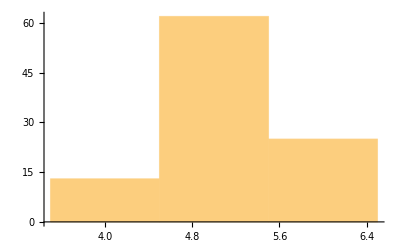

```mathematica
Histogram[%236]
```

```mathematica
transmission= {{Table[Import["/home/shardulmukim/PhD/fwi/1d_multi/4_terminal/data_ca_"<>ToString[X]<>"_imp.dat"],{X,15}]},{Table[Import["/home/shardulmukim/PhD/fwi/1d_multi/4_terminal/data_ca_sameside_"<>ToString[x]<>"_imp.dat"],{x,15}]}}
```

{{{{{-2.2,7.596×10^-6},{-2.19,1.52609×10^-6},{-2.18,6.07013×10^-7},{-2.17,1.32844×10^-7},{-2.16,6.89175×10^-8},431,{2.16,4.17223×10^-8},{2.17,6.47392×10^-8},{2.18,1.22911×10^-7},{2.19,3.61054×10^-7},{2.2,9.02547×10^-6}},{1},11,{1},{1}}},1}
 |  |  |  |

```mathematica
transmission//Dimensions
```

{2,1,15,441,2}

```mathematica
transmission[[2,1]]//Dimensions
```

{15,441,2}

```mathematica
{91, 100}
```

```mathematica
XX[pos_,n_,mm_]:=Module[{m5=ParallelTable[{ω,TRA[ω,mm,pos]},{ω,Range[-2.2,2.2,0.01]}]},
ρ1=Table[Module[{B1=Transpose[{m5[[1;;441]][[;;,1]],100(m5[[1;;441,2]]-transmission[[n,1]][[ξ]][[1;;441,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,-2.2,2.2}]/((4.4)*100)],{ξ,15}]; 
Abs[(Position[ρ1,Min[ρ1]][[1,1]]-mm)]/mm]
```

```mathematica
Clear[XX]
```

```mathematica
XX[91,1,7]
```

0

```mathematica
AA=Table[Print["Done_"<>ToString[mm]<>"!!"];Mean[Table[XX[91,1,mm],1000]],{mm,13}]
```

Done_1!!

Done_2!!

Done_3!!

Done_4!!

Done_5!!

Done_6!!

Done_7!!

Done_8!!

Done_9!!

Done_10!!

Done_11!!

Done_12!!

Done_13!!

{0,11/2000,2/375,63/4000,39/2500,119/6000,71/3500,19/800,8/375,9/400,139/5500,51/2000,87/3250}

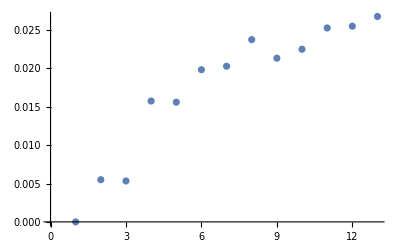

```mathematica
ListPlot[AA]
```

```mathematica
Interpolation[%121]
```

InterpolatingFunction[…]

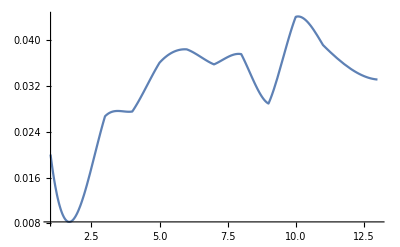

```mathematica
Plot[%143[x],{x,1,13}]
```

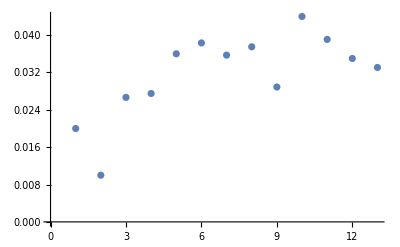

```mathematica
ListPlot[AA]
```

```mathematica
%118
```

{0,0,1/150,1/80,9/500,1/50,3/140,1/50,11/450,2/125,27/1100,7/300,37/1300}

```mathematica
%118//Dimensions
```

{13}

```mathematica
Join[{Range[1,13,1]},{%118}]//Transpose
```

{{1,0},{2,0},{3,1/150},{4,1/80},{5,9/500},{6,1/50},{7,3/140},{8,1/50},{9,11/450},{10,2/125},{11,27/1100},{12,7/300},{13,37/1300}}

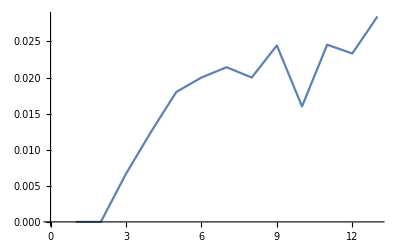

```mathematica
ListPlot[{{1,0},{2,0},{3,1/150},{4,1/80},{5,9/500},{6,1/50},{7,3/140},{8,1/50},{9,11/450},{10,2/125},{11,27/1100},{12,7/300},{13,37/1300}},Joined->True]
```

```mathematica
Interpolation[%118,InterpolationOrder->3]
```

InterpolatingFunction[…]

```mathematica
Fit[%137,{1,x^2},x]
```

0.00835522+0.000130357 x^2

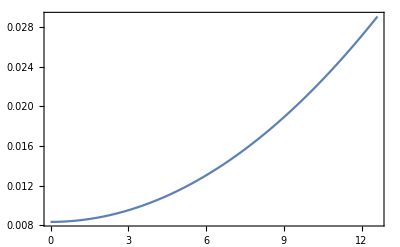

```mathematica
Plot[0.008355219009901285+0.00013035672985505764 x^2,{x,0,12.6105},Frame->True]
```

```mathematica
%118
```

{0,0,1/150,1/80,9/500,1/50,3/140,1/50,11/450,2/125,27/1100,7/300,37/1300}

```mathematica
Interpolation[Table[%121[[x]],{x,2,8}]]
```

InterpolatingFunction[…]

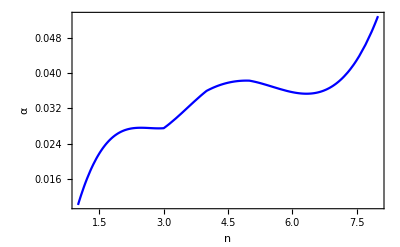

```mathematica
Plot[InterpolatingFunction[{{1,7}},{5,3,0,{7},{4},0,0,0,0,Automatic,{},{},False},{{1,2,3,4,5,6,7}},{{1/100},{2/75},{11/400},{9/250},{23/600},{1/28},{3/80}},{Automatic}][x],{x,1,8},Frame->True,PlotStyle->Blue,FrameLabel->{{HoldForm[α],None},{HoldForm[n],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",14,GrayLevel[0]}]
```

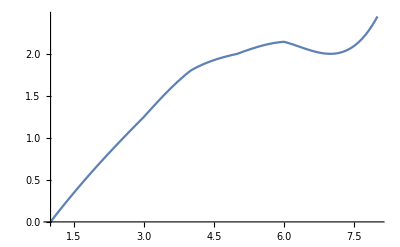

```mathematica
Plot[InterpolatingFunction[{{1,8}},{5,3,0,{8},{4},0,0,0,0,Automatic,{},{},False},{{1,2,3,4,5,6,7,8}},{{0},{2/3},{5/4},{9/5},{2},{15/7},{2},{22/9}},{Automatic}][x],{x,1,8}]
```

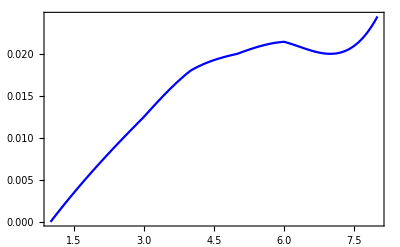

```mathematica
Plot[InterpolatingFunction[{{1,8}},{5,3,0,{8},{4},0,0,0,0,Automatic,{},{},False},{{1,2,3,4,5,6,7,8}},{{0},{1/150},{1/80},{9/500},{1/50},{3/140},{1/50},{11/450}},{Automatic}][x],{x,1,8},Frame->True,PlotStyle->Blue]
```

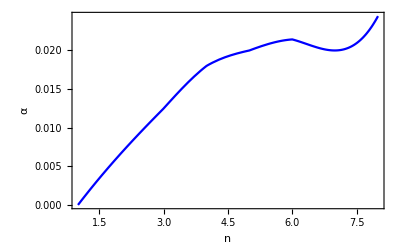

```mathematica
Show[%162,FrameLabel->{{HoldForm[α],None},{HoldForm[n],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",14,GrayLevel[0]}]
```

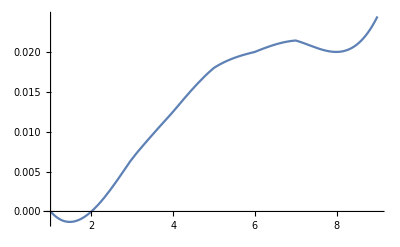

```mathematica
Plot[InterpolatingFunction[{{1,9}},{5,3,0,{9},{4},0,0,0,0,Automatic,{},{},False},{{1,2,3,4,5,6,7,8,9}},{{0},{0},{1/150},{1/80},{9/500},{1/50},{3/140},{1/50},{11/450}},{Automatic}][x],{x,1,9}]
```

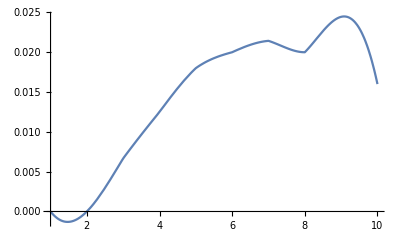

```mathematica
Plot[InterpolatingFunction[{{1,10}},{5,3,0,{10},{4},0,0,0,0,Automatic,{},{},False},{{1,2,3,4,5,6,7,8,9,10}},{{0},{0},{1/150},{1/80},{9/500},{1/50},{3/140},{1/50},{11/450},{2/125}},{Automatic}][x],{x,1,10}]
```

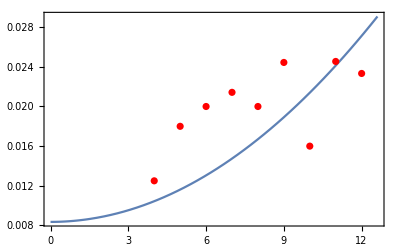

```mathematica
Show[%148,ListPlot[%118,PlotStyle->Red]]
```

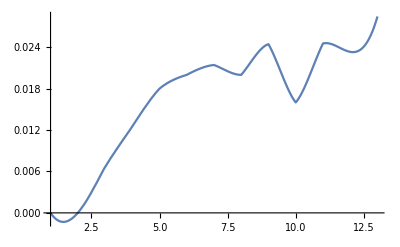

```mathematica
Plot[%128[x],{x,1,13}]
```

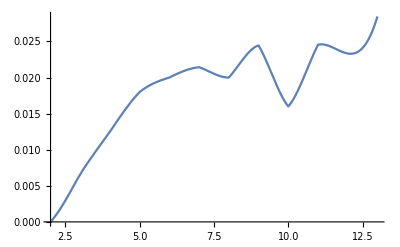

```mathematica
Plot[%122[x],{x,2,13}]
```

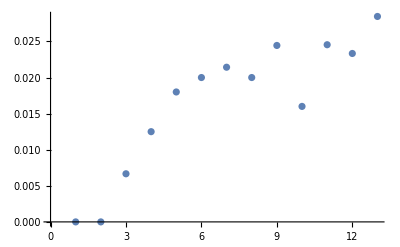

```mathematica
ListPlot[AA]
```

```mathematica
Table[{y,100*Around[Table[AA[[x]][[y]],{x,100}]]},{y,15}]
```

{{1,4.220.34},{2,3.220.29},{3,2.460.25},{4,1.910.21},{5,1.540.18},{6,1.340.16},{7,1.270.15},{8,1.320.16},{9,1.450.17},{10,1.660.17},{11,1.910.19},{12,2.180.19},{13,2.470.20},{14,2.780.21},{15,3.090.22}}

```mathematica
Table[Position[AA[[x]],Min[AA[[x]]]],{x,100}]//Flatten
```

{8,7,7,7,7,7,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,6,8,7,7,7,6,7,7,7,7,7,7,7,7,7,8,7,7,8,7,7,7,7,7,7,7,8,7,7,8,7,7,7,7,7,7,7,7,7,6,7,7,7,7,7,6,7,7,7,7,7,7,7,8,8,6,8,7,7,7,7,7,7,6,7,8,7,7,7,7,7,7,7,7,7,7}

```mathematica
Count[%85,7]
```

82

```mathematica
ListPlot[%81,Frame->True,LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]},FrameLabel->{{HoldForm[χ],None},{HoldForm[n],None}},PlotStyle->Directive[Blue,PointSize[0.02],"LineOpacity"->0.5]]
```

-Graphics-

```mathematica
Export["/home/shardulmukim/PhD/fwi/1D/misfit_leadsonsameside_7per.pdf",%106]
```

/home/shardulmukim/PhD/fwi/1D/misfit_leadsonsameside_7per.pdf

```mathematica
ListPlot[%63,Frame->True,LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]},FrameLabel->{{HoldForm[χ],None},{HoldForm[n],None}},PlotStyle->Directive[Blue,PointSize[0.02],"LineOpacity"->0.5]]
```

-Graphics-

```mathematica
Export["/home/shardulmukim/PhD/fwi/1D/misfit_leadsonopposide_7per.pdf",%106]
```

/home/shardulmukim/PhD/fwi/1D/misfit_leadsonopposide_7per.pdf

```mathematica
q[xx_]:=q[xx]=Table[{ω,Print["Energy_"<>ToString[ω]<>"_done!"];Mean[ParallelTable[TRA[ω,xx,100],5000]]},{ω,Range[-2.2,2.2,0.01]}]
```

```mathematica
Table[Print["Running_CA_FOR_"<>ToString[x]<>"_!!"];Export["/home/shardulmukim/PhD/fwi/1d_multi/4_terminal/data_ca_sameside_"<>ToString[x]<>"_imp.dat",q[x]],{x,Range[1,15,1]}]
```

{/home/shardulmukim/PhD/fwi/1d_multi/4_terminal/data_ca_sameside_1_imp.dat,/home/shardulmukim/PhD/fwi/1d_multi/4_terminal/data_ca_sameside_2_imp.dat,/home/shardulmukim/PhD/fwi/1d_multi/4_terminal/data_ca_sameside_3_imp.dat,/home/shardulmukim/PhD/fwi/1d_multi/4_terminal/data_ca_sameside_4_imp.dat,/home/shardulmukim/PhD/fwi/1d_multi/4_terminal/data_ca_sameside_5_imp.dat,/home/shardulmukim/PhD/fwi/1d_multi/4_terminal/data_ca_sameside_6_imp.dat,/home/shardulmukim/PhD/fwi/1d_multi/4_terminal/data_ca_sameside_7_imp.dat,/home/shardulmukim/PhD/fwi/1d_multi/4_terminal/data_ca_sameside_8_imp.dat,/home/shardulmukim/PhD/fwi/1d_multi/4_terminal/data_ca_sameside_9_imp.dat,/home/shardulmukim/PhD/fwi/1d_multi/4_terminal/data_ca_sameside_10_imp.dat,/home/shardulmukim/PhD/fwi/1d_multi/4_terminal/data_ca_sameside_11_imp.dat,/home/shardulmukim/PhD/fwi/1d_multi/4_terminal/data_ca_sameside_12_imp.dat,/home/shardulmukim/PhD/fwi/1d_multi/4_terminal/data_ca_sameside_13_imp.dat,/home/shardulmukim/PhD/fwi/1d_multi/4_terminal/data_ca_sameside_14_imp.dat,/home/shardulmukim/PhD/fwi/1d_multi/4_terminal/data_ca_sameside_15_imp.dat}

```mathematica
ϕ:=Module[{m5=ParallelTable[{ω,TRA[ω,6,91]},{ω,Range[-2.2,2.2,0.01]}]},
a1=Module[{B1=Transpose[{m5[[1;;441]][[;;,1]],(m5[[1;;441,2]]-r[1][[1;;441,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,-2.1,2.1}]/((2.1+2.1)*100)];
a2=Module[{B1=Transpose[{m5[[1;;441]][[;;,1]],(m5[[1;;441,2]]-r[3][[1;;441,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,-2.1,2.1}]/((2.1+2.1)*100)];
a3=Module[{B1=Transpose[{m5[[1;;441]][[;;,1]],(m5[[1;;441,2]]-r[6][[1;;441,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,-2.1,2.1}]/((2.1+2.1)*100)];
a4=Module[{B1=Transpose[{m5[[1;;441]][[;;,1]],(m5[[1;;441,2]]-r[9][[1;;441,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,-2.1,2.1}]/((2.1+2.1)*100)];
a5=Module[{B1=Transpose[{m5[[1;;441]][[;;,1]],(m5[[1;;441,2]]-r[12][[1;;441,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,-2.1,2.1}]/((2.1+2.1)*100)];
(*a6=Module[{B1=Transpose[{m5[[1;;441]][[;;,1]],(m5[[1;;441,2]]-q[15][[1;;441,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,-2.1,2.1}]/((2.1+2.1)*100)];*)1000{a1,a2,a3,a4,a5(*,a6*)}]
```

```mathematica
Table[ϕ,100]
```

{{0.443606,0.291487,0.244451,0.313572,0.429612},{0.515158,0.32412,0.234448,0.280253,0.399425},{0.535203,0.315131,0.196006,0.242856,0.35757},{0.505067,0.332138,0.223926,0.278634,0.388078},{0.657583,0.405261,0.271884,0.329076,0.452818},{0.537827,0.314105,0.222103,0.293248,0.423834},{0.50303,0.280915,0.196766,0.284847,0.390595},{0.527196,0.350557,0.280117,0.333754,0.436464},{0.556128,0.307913,0.235074,0.316974,0.43909},{0.572384,0.354906,0.218304,0.276892,0.383962},{0.576154,0.34328,0.234072,0.286773,0.391267},{0.565182,0.35767,0.22031,0.28175,0.393744},{0.523173,0.317006,0.207313,0.293852,0.418845},{0.505415,0.305007,0.217513,0.310622,0.448515},{0.627136,0.391603,0.231211,0.278382,0.384482},{0.621037,0.39081,0.293063,0.367762,0.493313},{0.498835,0.314496,0.219233,0.27498,0.377086},{0.549547,0.34898,0.249217,0.301587,0.400806},{0.51053,0.296509,0.187343,0.21184,0.301937},{0.512889,0.291218,0.190566,0.248936,0.3714},{0.399119,0.23611,0.175356,0.256083,0.373463},{0.490862,0.323289,0.244907,0.313723,0.436291},{0.47486,0.313439,0.202329,0.249022,0.357464},{0.523916,0.336135,0.224061,0.286438,0.403847},{0.492948,0.267252,0.188722,0.271518,0.385938},{0.493375,0.300932,0.197258,0.263031,0.369427},{0.55112,0.322354,0.229348,0.322289,0.441234},{0.579297,0.373375,0.268104,0.314615,0.427384},{0.515223,0.308714,0.210453,0.263824,0.362598},{0.567678,0.345045,0.248279,0.297417,0.413167},{0.513669,0.301661,0.220762,0.28413,0.388477},{0.524552,0.334726,0.241661,0.293943,0.370846},{0.538158,0.320429,0.234081,0.298222,0.410867},{0.534854,0.367617,0.267779,0.333406,0.456501},{0.483993,0.318058,0.235361,0.306775,0.404118},{0.59037,0.375999,0.255934,0.298856,0.404119},{0.418085,0.259117,0.201925,0.283091,0.407031},{0.526419,0.316447,0.250057,0.299694,0.393378},{0.479356,0.296914,0.199701,0.270626,0.356659},{0.479372,0.287917,0.184658,0.245884,0.351306},{0.549087,0.30131,0.228154,0.313622,0.424546},{0.528788,0.360868,0.242619,0.301185,0.383733},{0.611976,0.441689,0.288368,0.318865,0.42087},{0.544102,0.330018,0.250787,0.324698,0.44912},{0.5544,0.347983,0.250219,0.301954,0.401908},{0.534007,0.344668,0.263359,0.342028,0.442558},{0.459904,0.283779,0.203223,0.271509,0.383073},{0.503541,0.316698,0.235584,0.278207,0.375391},{0.642302,0.421373,0.275085,0.313213,0.418775},{0.486656,0.277835,0.216718,0.303278,0.408099},{0.583828,0.384208,0.248092,0.294178,0.397985},{0.489497,0.330617,0.222007,0.306418,0.428392},{0.62151,0.376299,0.256311,0.298484,0.395862},{0.550382,0.337959,0.240265,0.277953,0.396436},{0.483465,0.327102,0.240147,0.309333,0.403888},{0.53372,0.311688,0.203399,0.281146,0.395566},{0.545048,0.33872,0.213694,0.291751,0.399319},{0.51457,0.315149,0.208433,0.251774,0.338579},{0.526385,0.328387,0.238937,0.302787,0.408288},{0.479226,0.306864,0.225969,0.296611,0.416296},{0.504644,0.306674,0.199874,0.257118,0.374002},{0.545946,0.310074,0.200296,0.271962,0.399427},{0.564537,0.310451,0.221497,0.288354,0.419808},{0.539896,0.34795,0.239548,0.315673,0.445535},{0.560849,0.346976,0.221059,0.285349,0.391122},{0.580869,0.372934,0.253789,0.30153,0.416699},{0.56153,0.332593,0.204505,0.263127,0.367863},{0.554979,0.357409,0.269573,0.328268,0.437716},{0.477601,0.28745,0.222794,0.298185,0.41806},{0.498179,0.309036,0.19685,0.242758,0.347988},{0.557355,0.345907,0.225196,0.288642,0.399811},{0.518178,0.320383,0.242721,0.301809,0.412309},{0.688822,0.426454,0.258076,0.315053,0.405896},{0.527446,0.329333,0.233035,0.308474,0.428407},{0.630177,0.39575,0.24912,0.278011,0.390887},{0.509215,0.32255,0.261258,0.312559,0.412526},{0.638131,0.41427,0.294525,0.330996,0.442578},{0.576865,0.381555,0.270764,0.320827,0.430589},{0.528178,0.345797,0.220676,0.284073,0.402442},{0.604368,0.39974,0.269842,0.308356,0.421222},{0.526404,0.336927,0.241848,0.308568,0.422818},{0.472787,0.255545,0.179171,0.230436,0.332971},{0.626143,0.395514,0.247619,0.299498,0.423701},{0.427992,0.258032,0.202986,0.244643,0.347452},{0.498778,0.310775,0.207435,0.295526,0.411673},{0.568958,0.332651,0.205369,0.270031,0.402332},{0.484358,0.299318,0.214781,0.274767,0.3812},{0.519129,0.318225,0.232064,0.323255,0.435454},{0.519307,0.310776,0.241011,0.326723,0.450895},{0.563987,0.333461,0.236995,0.296897,0.402307},{0.54586,0.326757,0.242062,0.326673,0.447485},{0.559138,0.341274,0.228922,0.284122,0.392569},{0.551644,0.34996,0.250093,0.298568,0.404782},{0.538445,0.319439,0.215782,0.276153,0.38582},{0.470354,0.259678,0.202922,0.2825,0.39915},{0.487605,0.297319,0.196323,0.267693,0.381871},{0.606906,0.387865,0.257629,0.317441,0.439568},{0.574298,0.35886,0.240545,0.298708,0.412729},{0.480478,0.308438,0.21626,0.273481,0.380603},{0.636833,0.384698,0.254934,0.322613,0.430875}}

```mathematica
Table[Around[Table[%140[[x]][[y]],{x,100}]],{y,5}]
```

{0.540.05,0.330.04,0.2310.026,0.2930.026,0.4030.031}

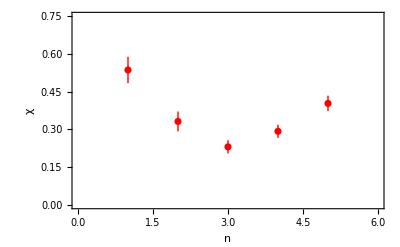

```mathematica
ListPlot[%141,PlotRange->{{0,6},{0,0.75}},PlotStyle->Red,Frame->True,FrameLabel->{{HoldForm[χ],None},{HoldForm[n],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]}]
```

```mathematica
Show[%144,%96]
```

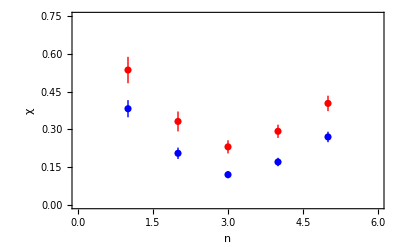

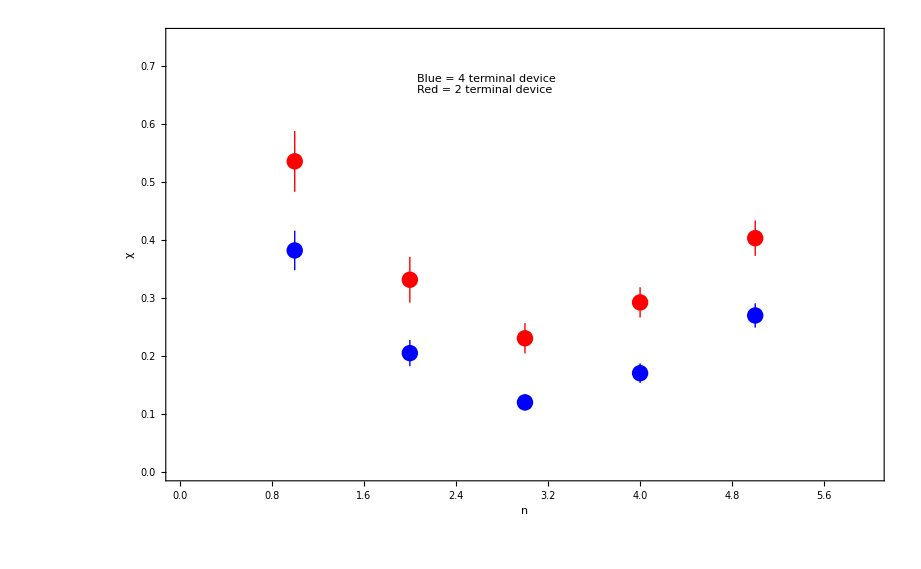

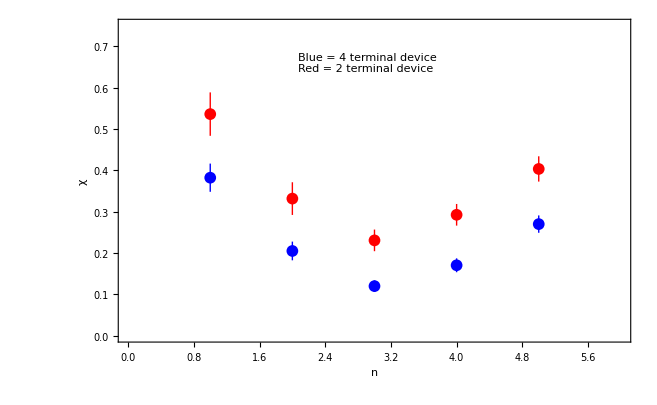

-Graphics-

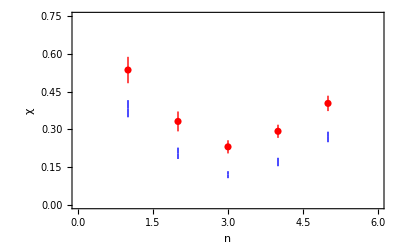

```mathematica
Table[Around[Table[%91[[x]][[y]],{x,100}]],{y,5}]
```

{0.3820.034,0.2050.023,0.1200.014,0.1710.017,0.2700.021}

```mathematica
ListPlot[%92,PlotRange->{{0,6},{0,0.45}},PlotStyle->Blue,Frame->True,FrameLabel->{{HoldForm[χ],None},{HoldForm[n],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]}]
```

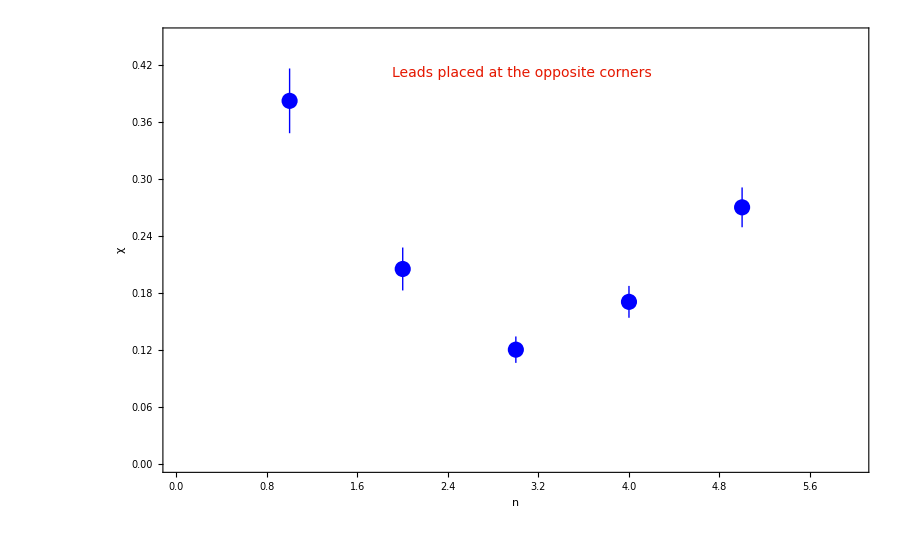

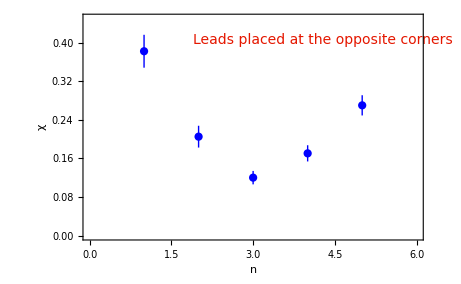

```mathematica
ListPlot[%74,PlotRange->{{0,7},{0,0.4}},PlotStyle->Blue,Frame->True,FrameLabel->{{HoldForm[χ],None},{HoldForm[n],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]}]
```

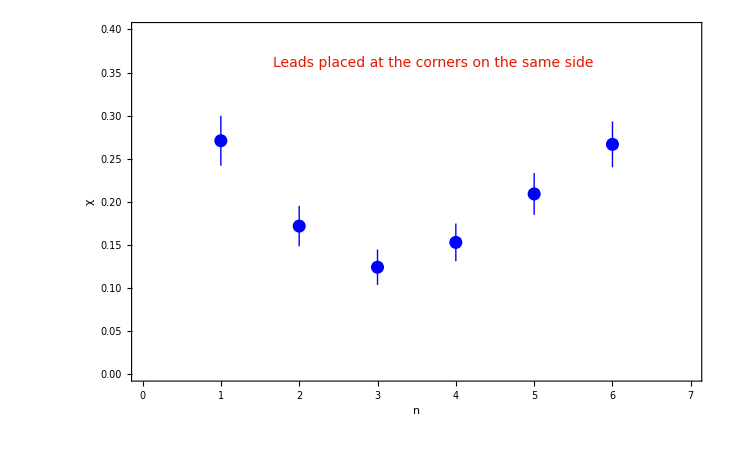

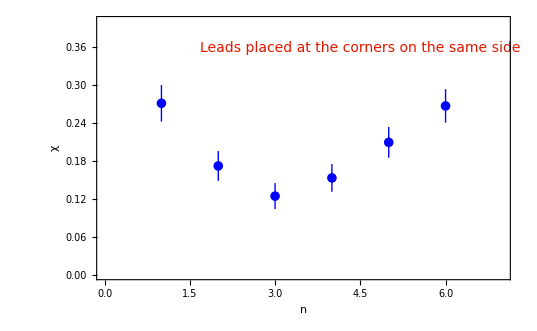

```mathematica
p[xx_]:=p[xx]=Table[{ω,Print["Energy_"<>ToString[ω]<>"_done!"];Mean[ParallelTable[TRA[ω,xx,91],5000]]},{ω,Range[-2.2,2.2,0.01]}]
```

```mathematica
p[1]
```

{{-2.2,7.92015×10^-7},{-2.19,3.24252×10^-7},{-2.18,3.99777×10^-8},{-2.17,2.3284×10^-9},{-2.16,7.55043×10^-10},{-2.15,4.28596×10^-10},{-2.14,2.95382×10^-10},{-2.13,2.66225×10^-10},{-2.12,2.38004×10^-10},{-2.11,2.24516×10^-10},{-2.1,2.18976×10^-10},{-2.09,2.20142×10^-10},{-2.08,2.38569×10^-10},{-2.07,2.62079×10^-10},{-2.06,3.163×10^-10},{-2.05,4.03357×10^-10},{-2.04,5.9608×10^-10},{-2.03,1.25456×10^-9},{-2.02,5.2269×10^-9},{-2.01,1.12282×10^-7},{-2.,0.00169775},{-1.99,0.0205416},{-1.98,0.00361784},{-1.97,0.00194044},{-1.96,0.0017672},{-1.95,0.00180641},{-1.94,0.001958},{-1.93,0.00220894},{-1.92,0.00251013},{-1.91,0.0028441},{-1.9,0.00327644},{-1.89,0.00379932},{-1.88,0.00436432},{-1.87,0.00503022},{-1.86,0.00581028},{-1.85,0.00657866},{-1.84,0.00747157},{-1.83,0.00837022},{-1.82,0.00937464},{-1.81,0.0103762},{-1.8,0.0114231},{-1.79,0.0123353},{-1.78,0.0132695},{-1.77,0.0141225},{-1.76,0.0149206},{-1.75,0.0157027},{-1.74,0.0165408},{-1.73,0.0172951},{-1.72,0.0181025},{-1.71,0.019088},{-1.7,0.0202676},{-1.69,0.0217469},{-1.68,0.0240907},{-1.67,0.028395},{-1.66,0.0384104},{-1.65,0.0653123},{-1.64,0.0775916},{-1.63,0.0252476},{-1.62,0.025749},{-1.61,0.029309},{-1.6,0.0334481},{-1.59,0.0380724},{-1.58,0.0462957},{-1.57,0.0436719},{-1.56,0.050728},{-1.55,0.0601303},{-1.54,0.0713737},{-1.53,0.0849878},{-1.52,0.10282},{-1.51,0.124308},{-1.5,0.150793},{-1.49,0.181283},{-1.48,0.21129},{-1.47,0.234161},{-1.46,0.242655},{-1.45,0.231576},{-1.44,0.207631},{-1.43,0.176627},{-1.42,0.146675},{-1.41,0.120385},{-1.4,0.0978123},{-1.39,0.0606603},{-1.38,0.0747679},{-1.37,0.0617965},{-1.36,0.0535459},{-1.35,0.0470003},{-1.34,0.0419346},{-1.33,0.0378054},{-1.32,0.0346277},{-1.31,0.0319051},{-1.3,0.029819},{-1.29,0.0281373},{-1.28,0.0268562},{-1.27,0.0258709},{-1.26,0.025224},{-1.25,0.0248705},{-1.24,0.024738},{-1.23,0.0249368},{-1.22,0.0254887},{-1.21,0.0264916},{-1.2,0.0278224},{-1.19,0.0297578},{-1.18,0.0325236},{-1.17,0.0364322},{-1.16,0.0419595},{-1.15,0.0497619},{-1.14,0.0617681},{-1.13,0.0799813},{-1.12,0.1109},{-1.11,0.159637},{-1.1,0.224089},{-1.09,0.238901},{-1.08,0.18969},{-1.07,0.12125},{-1.06,0.0882875},{-1.05,0.0997022},{-1.04,0.0596064},{-1.03,0.0353147},{-1.02,0.0261185},{-1.01,0.0143497},{-1.,0.00944552},{-0.99,0.00671384},{-0.98,0.00506257},{-0.97,0.00401287},{-0.96,0.00333204},{-0.95,0.00278632},{-0.94,0.0025075},{-0.93,0.00238139},{-0.92,0.00236284},{-0.91,0.00267565},{-0.9,0.00311449},{-0.89,0.00462532},{-0.88,0.00827913},{-0.87,0.0153744},{-0.86,0.0222216},{-0.85,0.0155222},{-0.84,0.00690106},{-0.83,0.00337885},{-0.82,0.00196398},{-0.81,0.00121837},{-0.8,0.000865293},{-0.79,0.000652533},{-0.78,0.000519006},{-0.77,0.000421006},{-0.76,0.000370396},{-0.75,0.000320751},{-0.74,0.000296302},{-0.73,0.000263622},{-0.72,0.000257046},{-0.71,0.00025597},{-0.7,0.000252119},{-0.69,0.00025607},{-0.68,0.000281946},{-0.67,0.000311793},{-0.66,0.000371739},{-0.65,0.000475865},{-0.64,0.000738444},{-0.63,0.00154498},{-0.62,0.00648032},{-0.61,0.0633223},{-0.6,0.0248322},{-0.59,0.0026404},{-0.58,0.00111785},{-0.57,0.00169024},{-0.56,0.00336415},{-0.55,0.00834753},{-0.54,0.0409661},{-0.53,0.0300309},{-0.52,0.106351},{-0.51,0.107514},{-0.5,0.0716363},{-0.49,0.0469117},{-0.48,0.0284115},{-0.47,0.031981},{-0.46,0.0222607},{-0.45,0.0243348},{-0.44,0.0285041},{-0.43,0.0375},{-0.42,0.0554793},{-0.41,0.0958032},{-0.4,0.17157},{-0.39,0.206538},{-0.38,0.13339},{-0.37,0.0675399},{-0.36,0.0382425},{-0.35,0.0225415},{-0.34,0.0155602},{-0.33,0.0114868},{-0.32,0.00924373},{-0.31,0.00795062},{-0.3,0.00724737},{-0.29,0.00720412},{-0.28,0.0077646},{-0.27,0.00950209},{-0.26,0.0142266},{-0.25,0.0320166},{-0.24,0.171653},{-0.23,0.0471812},{-0.22,0.0130888},{-0.21,0.00321668},{-0.2,0.00124637},{-0.19,0.000614214},{-0.18,0.000329606},{-0.17,0.000200598},{-0.16,0.000120705},{-0.15,0.0000852716},{-0.14,0.0000530884},{-0.13,0.0000369961},{-0.12,0.0000274855},{-0.11,0.0000188292},{-0.1,0.0000158696},{-0.09,0.0000116914},{-0.08,8.55844×10^-6},{-0.07,6.47215×10^-6},{-0.06,3.12262×10^-6},{-0.05,4.14411×10^-6},{-0.04,1.62363×10^-6},{-0.03,2.28819×10^-6},{-0.02,1.09367×10^-6},{-0.01,3.47868×10^-7},{0.,7.73058×10^-11},{0.01,1.45076×10^-6},{0.02,6.28606×10^-6},{0.03,0.000108635},{0.04,0.000218633},{0.05,0.000110952},{0.06,0.0000285059},{0.07,0.0000483859},{0.08,0.0000343411},{0.09,0.0000303766},{0.1,0.0000375045},{0.11,0.000034902},{0.12,0.0000392532},{0.13,0.0000530968},{0.14,0.0000686876},{0.15,0.000101064},{0.16,0.000133509},{0.17,0.000189832},{0.18,0.000296979},{0.19,0.000498226},{0.2,0.000904306},{0.21,0.00187971},{0.22,0.00497688},{0.23,0.0209806},{0.24,0.12082},{0.25,0.0646648},{0.26,0.0288496},{0.27,0.0143185},{0.28,0.0100702},{0.29,0.00844664},{0.3,0.00796623},{0.31,0.00817941},{0.32,0.00900282},{0.33,0.010533},{0.34,0.0131204},{0.35,0.0176703},{0.36,0.0259168},{0.37,0.0438929},{0.38,0.0750245},{0.39,0.14511},{0.4,0.212091},{0.41,0.173066},{0.42,0.105484},{0.43,0.063708},{0.44,0.0432075},{0.45,0.0326129},{0.46,0.0273404},{0.47,0.0250087},{0.48,0.0193723},{0.49,0.0287669},{0.5,0.039636},{0.51,0.0647698},{0.52,0.14139},{0.53,0.163115},{0.54,0.0537113},{0.55,0.0161016},{0.56,0.0113667},{0.57,0.0178601},{0.58,0.00705634},{0.59,0.00706777},{0.6,0.0147341},{0.61,0.070073},{0.62,0.0857709},{0.63,0.0397742},{0.64,0.0104922},{0.65,0.00358526},{0.66,0.0018936},{0.67,0.00123484},{0.68,0.000886931},{0.69,0.000692252},{0.7,0.00060404},{0.71,0.000537358},{0.72,0.000500401},{0.73,0.000473098},{0.74,0.000477023},{0.75,0.000470304},{0.76,0.000506524},{0.77,0.000556419},{0.78,0.000637146},{0.79,0.000693921},{0.8,0.000841567},{0.81,0.00106125},{0.82,0.0014213},{0.83,0.00195549},{0.84,0.00293974},{0.85,0.0048851},{0.86,0.00858789},{0.87,0.0130985},{0.88,0.0166084},{0.89,0.017873},{0.9,0.0123938},{0.91,0.00799484},{0.92,0.00555386},{0.93,0.00414241},{0.94,0.00353573},{0.95,0.00322282},{0.96,0.00309143},{0.97,0.00318345},{0.98,0.0035458},{0.99,0.00402793},{1.,0.00490122},{1.01,0.00615572},{1.02,0.00798505},{1.03,0.0113143},{1.04,0.0172594},{1.05,0.0291427},{1.06,0.0890343},{1.07,0.13719},{1.08,0.134881},{1.09,0.225095},{1.1,0.177406},{1.11,0.172071},{1.12,0.142816},{1.13,0.121449},{1.14,0.0854709},{1.15,0.0634759},{1.16,0.0501647},{1.17,0.0416096},{1.18,0.0358152},{1.19,0.0320361},{1.2,0.0292228},{1.21,0.0272922},{1.22,0.0260051},{1.23,0.0251937},{1.24,0.0244969},{1.25,0.0244445},{1.26,0.0245442},{1.27,0.0249443},{1.28,0.0257293},{1.29,0.0267365},{1.3,0.0280718},{1.31,0.0298204},{1.32,0.0318978},{1.33,0.0346615},{1.34,0.0379045},{1.35,0.0420703},{1.36,0.047328},{1.37,0.0537354},{1.38,0.0620804},{1.39,0.0728685},{1.4,0.0811191},{1.41,0.0912025},{1.42,0.120272},{1.43,0.146223},{1.44,0.175825},{1.45,0.207064},{1.46,0.232824},{1.47,0.244235},{1.48,0.237823},{1.49,0.217681},{1.5,0.189669},{1.51,0.160352},{1.52,0.133692},{1.53,0.111556},{1.54,0.0932651},{1.55,0.0790007},{1.56,0.0680116},{1.57,0.0591287},{1.58,0.0520058},{1.59,0.0456849},{1.6,0.0409201},{1.61,0.0617388},{1.62,0.055255},{1.63,0.0732237},{1.64,0.130243},{1.65,0.133388},{1.66,0.0813634},{1.67,0.0572333},{1.68,0.0351436},{1.69,0.0272548},{1.7,0.0250972},{1.71,0.0239781},{1.72,0.0228869},{1.73,0.0222674},{1.74,0.0214624},{1.75,0.0207069},{1.76,0.0198108},{1.77,0.0190188},{1.78,0.018087},{1.79,0.0170188},{1.8,0.0157634},{1.81,0.0146108},{1.82,0.0132035},{1.83,0.0117864},{1.84,0.0104074},{1.85,0.00907412},{1.86,0.00776201},{1.87,0.00665464},{1.88,0.00561028},{1.89,0.00474208},{1.9,0.00391556},{1.91,0.00324165},{1.92,0.0026813},{1.93,0.00218969},{1.94,0.00175443},{1.95,0.00141786},{1.96,0.00113951},{1.97,0.000936697},{1.98,0.000867823},{1.99,0.00111115},{2.,0.000106484},{2.01,0.0000929929},{2.02,6.38864×10^-7},{2.03,1.72659×10^-8},{2.04,2.56909×10^-9},{2.05,1.03835×10^-9},{2.06,5.81408×10^-10},{2.07,4.28729×10^-10},{2.08,3.64279×10^-10},{2.09,3.24658×10^-10},{2.1,3.1048×10^-10},{2.11,3.08719×10^-10},{2.12,3.18909×10^-10},{2.13,3.50218×10^-10},{2.14,4.04638×10^-10},{2.15,5.01188×10^-10},{2.16,6.90133×10^-10},{2.17,1.05515×10^-9},{2.18,2.00742×10^-9},{2.19,5.88564×10^-9},{2.2,3.32309×10^-7}}

```mathematica
p[3]
```

{{-2.2,5.48307×10^-6},{-2.19,1.74622×10^-6},{-2.18,7.88811×10^-7},{-2.17,5.06408×10^-7},{-2.16,5.76272×10^-8},{-2.15,2.91737×10^-9},{-2.14,8.94109×10^-10},{-2.13,5.02928×10^-10},{-2.12,3.65048×10^-10},{-2.11,2.942×10^-10},{-2.1,2.71358×10^-10},{-2.09,2.68238×10^-10},{-2.08,2.83892×10^-10},{-2.07,3.18778×10^-10},{-2.06,3.96817×10^-10},{-2.05,5.42164×10^-10},{-2.04,9.36093×10^-10},{-2.03,1.90403×10^-9},{-2.02,6.30032×10^-9},{-2.01,6.22536×10^-8},{-2.,0.00181696},{-1.99,0.0445205},{-1.98,0.0461196},{-1.97,0.0221704},{-1.96,0.00888001},{-1.95,0.00495601},{-1.94,0.00375661},{-1.93,0.00334345},{-1.92,0.00330835},{-1.91,0.00339757},{-1.9,0.00359898},{-1.89,0.00389283},{-1.88,0.00419011},{-1.87,0.00464115},{-1.86,0.00520727},{-1.85,0.00563955},{-1.84,0.00640466},{-1.83,0.00708511},{-1.82,0.00777707},{-1.81,0.00858831},{-1.8,0.00938565},{-1.79,0.0102025},{-1.78,0.0110092},{-1.77,0.0118296},{-1.76,0.0126512},{-1.75,0.0133592},{-1.74,0.0143521},{-1.73,0.0152993},{-1.72,0.0162418},{-1.71,0.0176256},{-1.7,0.0191488},{-1.69,0.0214292},{-1.68,0.0248974},{-1.67,0.0316047},{-1.66,0.0467693},{-1.65,0.0913048},{-1.64,0.157451},{-1.63,0.104998},{-1.62,0.0536044},{-1.61,0.03746},{-1.6,0.0318941},{-1.59,0.0345526},{-1.58,0.0441613},{-1.57,0.0515892},{-1.56,0.047467},{-1.55,0.047152},{-1.54,0.0545748},{-1.53,0.0649941},{-1.52,0.0787609},{-1.51,0.0948286},{-1.5,0.117092},{-1.49,0.142736},{-1.48,0.171589},{-1.47,0.20078},{-1.46,0.222653},{-1.45,0.230865},{-1.44,0.222064},{-1.43,0.19893},{-1.42,0.169633},{-1.41,0.138845},{-1.4,0.111792},{-1.39,0.0833864},{-1.38,0.082142},{-1.37,0.0789},{-1.36,0.0668935},{-1.35,0.0557871},{-1.34,0.0479493},{-1.33,0.0425334},{-1.32,0.0384281},{-1.31,0.0351466},{-1.3,0.0324624},{-1.29,0.0303405},{-1.28,0.0287106},{-1.27,0.0275677},{-1.26,0.0266463},{-1.25,0.0259461},{-1.24,0.0257152},{-1.23,0.0257089},{-1.22,0.0261635},{-1.21,0.0269791},{-1.2,0.0280914},{-1.19,0.0298668},{-1.18,0.0322428},{-1.17,0.03534},{-1.16,0.0401581},{-1.15,0.0467257},{-1.14,0.056634},{-1.13,0.0715512},{-1.12,0.0954644},{-1.11,0.134737},{-1.1,0.19426},{-1.09,0.243022},{-1.08,0.171679},{-1.07,0.159514},{-1.06,0.124045},{-1.05,0.119344},{-1.04,0.102284},{-1.03,0.0815627},{-1.02,0.0683004},{-1.01,0.0540788},{-1.,0.0354024},{-0.99,0.0221664},{-0.98,0.014397},{-0.97,0.0104602},{-0.96,0.00827431},{-0.95,0.00687816},{-0.94,0.00616944},{-0.93,0.00575182},{-0.92,0.00583294},{-0.91,0.0063447},{-0.9,0.00779022},{-0.89,0.0105982},{-0.88,0.0181712},{-0.87,0.0362119},{-0.86,0.057873},{-0.85,0.0644952},{-0.84,0.0531767},{-0.83,0.0319251},{-0.82,0.0156607},{-0.81,0.00838595},{-0.8,0.00500961},{-0.79,0.00342783},{-0.78,0.0025218},{-0.77,0.00190494},{-0.76,0.00153789},{-0.75,0.00132465},{-0.74,0.00113425},{-0.73,0.00101126},{-0.72,0.000916222},{-0.71,0.000889792},{-0.7,0.000855596},{-0.69,0.000841793},{-0.68,0.000877877},{-0.67,0.00093177},{-0.66,0.00102192},{-0.65,0.00122177},{-0.64,0.00166335},{-0.63,0.00273617},{-0.62,0.00831417},{-0.61,0.0721645},{-0.6,0.105136},{-0.59,0.0395632},{-0.58,0.00850262},{-0.57,0.00266814},{-0.56,0.00227555},{-0.55,0.00372705},{-0.54,0.0188684},{-0.53,0.0356489},{-0.52,0.0261242},{-0.51,0.0490462},{-0.5,0.0563706},{-0.49,0.0683205},{-0.48,0.0463471},{-0.47,0.0319525},{-0.46,0.0314848},{-0.45,0.032032},{-0.44,0.0254554},{-0.43,0.0261019},{-0.42,0.0329352},{-0.41,0.0502466},{-0.4,0.0882219},{-0.39,0.145412},{-0.38,0.171646},{-0.37,0.092163},{-0.36,0.057564},{-0.35,0.0468},{-0.34,0.0251724},{-0.33,0.0150067},{-0.32,0.0108288},{-0.31,0.00867001},{-0.3,0.0074688},{-0.29,0.00697352},{-0.28,0.00705802},{-0.27,0.00799691},{-0.26,0.0106484},{-0.25,0.0193171},{-0.24,0.0778222},{-0.23,0.0509449},{-0.22,0.0375577},{-0.21,0.0104765},{-0.2,0.00293224},{-0.19,0.00125724},{-0.18,0.000679888},{-0.17,0.000419958},{-0.16,0.000281406},{-0.15,0.000196488},{-0.14,0.000151182},{-0.13,0.000111198},{-0.12,0.0000946493},{-0.11,0.0000774885},{-0.1,0.0000651393},{-0.09,0.0000535991},{-0.08,0.0000507715},{-0.07,0.0000469711},{-0.06,0.0000344462},{-0.05,0.0000319795},{-0.04,0.0000223402},{-0.03,0.0000182288},{-0.02,0.0000112423},{-0.01,4.51089×10^-6},{0.,6.72123×10^-9},{0.01,0.0000533059},{0.02,0.000638789},{0.03,0.00098415},{0.04,0.00341029},{0.05,0.00216214},{0.06,0.00179702},{0.07,0.00123598},{0.08,0.000518549},{0.09,0.000425034},{0.1,0.000320889},{0.11,0.000262506},{0.12,0.000241175},{0.13,0.000245291},{0.14,0.000264889},{0.15,0.000287294},{0.16,0.000324187},{0.17,0.00037981},{0.18,0.000487396},{0.19,0.000692639},{0.2,0.00106255},{0.21,0.00182262},{0.22,0.00388256},{0.23,0.0124091},{0.24,0.0902535},{0.25,0.0826589},{0.26,0.0578147},{0.27,0.0318924},{0.28,0.0171403},{0.29,0.0116888},{0.3,0.00987243},{0.31,0.00932177},{0.32,0.00957972},{0.33,0.010622},{0.34,0.0123988},{0.35,0.0156538},{0.36,0.0214528},{0.37,0.0325673},{0.38,0.0523653},{0.39,0.0813932},{0.4,0.135579},{0.41,0.175708},{0.42,0.157182},{0.43,0.108811},{0.44,0.0702573},{0.45,0.0481593},{0.46,0.0363097},{0.47,0.0298556},{0.48,0.0267521},{0.49,0.0277219},{0.5,0.0378559},{0.51,0.0430358},{0.52,0.0635574},{0.53,0.104879},{0.54,0.116504},{0.55,0.0547938},{0.56,0.0299462},{0.57,0.0356794},{0.58,0.0293782},{0.59,0.0210184},{0.6,0.0252542},{0.61,0.0630017},{0.62,0.0904465},{0.63,0.0762864},{0.64,0.0594354},{0.65,0.0319765},{0.66,0.0136608},{0.67,0.00635264},{0.68,0.00373071},{0.69,0.00269237},{0.7,0.00219135},{0.71,0.00190631},{0.72,0.00173969},{0.73,0.00170046},{0.74,0.00166161},{0.75,0.00164748},{0.76,0.00174993},{0.77,0.00187472},{0.78,0.00205521},{0.79,0.00227591},{0.8,0.00276649},{0.81,0.00322697},{0.82,0.00409649},{0.83,0.00556556},{0.84,0.00780453},{0.85,0.0116427},{0.86,0.0197003},{0.87,0.0330179},{0.88,0.0457123},{0.89,0.048511},{0.9,0.0466765},{0.91,0.037065},{0.92,0.025249},{0.93,0.0174872},{0.94,0.01282},{0.95,0.00980484},{0.96,0.00806721},{0.97,0.00713379},{0.98,0.00657545},{0.99,0.00647434},{1.,0.00677791},{1.01,0.00731513},{1.02,0.00868993},{1.03,0.0109271},{1.04,0.0151431},{1.05,0.0244241},{1.06,0.0580667},{1.07,0.118854},{1.08,0.148399},{1.09,0.180757},{1.1,0.169236},{1.11,0.146308},{1.12,0.131727},{1.13,0.136159},{1.14,0.120652},{1.15,0.100249},{1.16,0.0772323},{1.17,0.0585794},{1.18,0.046869},{1.19,0.038766},{1.2,0.0339109},{1.21,0.0303553},{1.22,0.0280668},{1.23,0.0266807},{1.24,0.0256665},{1.25,0.025041},{1.26,0.0248861},{1.27,0.0249431},{1.28,0.0254391},{1.29,0.0261243},{1.3,0.0270896},{1.31,0.0286532},{1.32,0.0304523},{1.33,0.0326299},{1.34,0.0354726},{1.35,0.0388689},{1.36,0.0432937},{1.37,0.0488032},{1.38,0.0559529},{1.39,0.0654418},{1.4,0.0801453},{1.41,0.0888869},{1.42,0.105163},{1.43,0.115848},{1.44,0.137429},{1.45,0.163988},{1.46,0.198143},{1.47,0.222321},{1.48,0.235622},{1.49,0.233537},{1.5,0.217807},{1.51,0.19292},{1.52,0.167068},{1.53,0.141487},{1.54,0.119358},{1.55,0.101578},{1.56,0.0869525},{1.57,0.0751846},{1.58,0.0663037},{1.59,0.0584944},{1.6,0.0534886},{1.61,0.0589848},{1.62,0.0790959},{1.63,0.103501},{1.64,0.159978},{1.65,0.223006},{1.66,0.189714},{1.67,0.142351},{1.68,0.100168},{1.69,0.0668012},{1.7,0.046492},{1.71,0.0361415},{1.72,0.0318559},{1.73,0.030218},{1.74,0.0293041},{1.75,0.0281096},{1.76,0.0271841},{1.77,0.0264133},{1.78,0.0253025},{1.79,0.0237328},{1.8,0.0228226},{1.81,0.0209316},{1.82,0.0193139},{1.83,0.0173524},{1.84,0.0154171},{1.85,0.0133203},{1.86,0.0115945},{1.87,0.00963299},{1.88,0.00817251},{1.89,0.00669888},{1.9,0.00547327},{1.91,0.00447375},{1.92,0.00362276},{1.93,0.00291645},{1.94,0.00227858},{1.95,0.00180092},{1.96,0.0014742},{1.97,0.00118103},{1.98,0.0010336},{1.99,0.000996919},{2.,0.0000289544},{2.01,0.0000131581},{2.02,2.83879×10^-6},{2.03,1.3243×10^-6},{2.04,2.99222×10^-7},{2.05,2.36944×10^-8},{2.06,3.17606×10^-9},{2.07,1.1621×10^-9},{2.08,7.03413×10^-10},{2.09,5.47169×10^-10},{2.1,4.74947×10^-10},{2.11,4.39879×10^-10},{2.12,4.43052×10^-10},{2.13,4.82558×10^-10},{2.14,5.28906×10^-10},{2.15,6.4637×10^-10},{2.16,8.79083×10^-10},{2.17,1.31337×10^-9},{2.18,2.52485×10^-9},{2.19,7.80837×10^-9},{2.2,1.71663×10^-7}}

```mathematica
p[6]
```

{{-2.2,1.01672×10^-6},{-2.19,2.44544×10^-6},{-2.18,1.94361×10^-6},{-2.17,8.79172×10^-7},{-2.16,6.01783×10^-7},{-2.15,2.3087×10^-7},{-2.14,5.74605×10^-8},{-2.13,6.44872×10^-9},{-2.12,1.18331×10^-9},{-2.11,7.11249×10^-10},{-2.1,5.05592×10^-10},{-2.09,4.4184×10^-10},{-2.08,4.33356×10^-10},{-2.07,4.46988×10^-10},{-2.06,5.28965×10^-10},{-2.05,6.69896×10^-10},{-2.04,1.00961×10^-9},{-2.03,1.90721×10^-9},{-2.02,4.75436×10^-9},{-2.01,2.49973×10^-8},{-2.,0.000198218},{-1.99,0.0322437},{-1.98,0.0502827},{-1.97,0.0602933},{-1.96,0.0548605},{-1.95,0.0341189},{-1.94,0.0177457},{-1.93,0.0103499},{-1.92,0.00716423},{-1.91,0.00568752},{-1.9,0.00513269},{-1.89,0.00486442},{-1.88,0.00471464},{-1.87,0.00476694},{-1.86,0.00502143},{-1.85,0.00537308},{-1.84,0.00563297},{-1.83,0.00596355},{-1.82,0.00640943},{-1.81,0.00698294},{-1.8,0.0075313},{-1.79,0.0081273},{-1.78,0.00877306},{-1.77,0.00924929},{-1.76,0.00997666},{-1.75,0.0108406},{-1.74,0.0115268},{-1.73,0.0124926},{-1.72,0.0134739},{-1.71,0.0147845},{-1.7,0.0164154},{-1.69,0.0189369},{-1.68,0.0222411},{-1.67,0.0284611},{-1.66,0.0409279},{-1.65,0.075773},{-1.64,0.154945},{-1.63,0.177984},{-1.62,0.128842},{-1.61,0.0865313},{-1.6,0.0629714},{-1.59,0.0484245},{-1.58,0.0416484},{-1.57,0.0444784},{-1.56,0.0516344},{-1.55,0.0515504},{-1.54,0.0500542},{-1.53,0.0513554},{-1.52,0.0565031},{-1.51,0.0666171},{-1.5,0.0807007},{-1.49,0.0998358},{-1.48,0.123085},{-1.47,0.1487},{-1.46,0.17824},{-1.45,0.200577},{-1.44,0.216363},{-1.43,0.213242},{-1.42,0.194973},{-1.41,0.167212},{-1.4,0.136161},{-1.39,0.104318},{-1.38,0.0819079},{-1.37,0.0797818},{-1.36,0.0822273},{-1.35,0.0795055},{-1.34,0.0683592},{-1.33,0.0568759},{-1.32,0.0482111},{-1.31,0.0420708},{-1.3,0.038031},{-1.29,0.0350625},{-1.28,0.0323212},{-1.27,0.0307709},{-1.26,0.0292306},{-1.25,0.0283578},{-1.24,0.0277714},{-1.23,0.0274183},{-1.22,0.0273705},{-1.21,0.0279095},{-1.2,0.0286148},{-1.19,0.029842},{-1.18,0.0318213},{-1.17,0.0343318},{-1.16,0.037886},{-1.15,0.0430936},{-1.14,0.0505449},{-1.13,0.0614904},{-1.12,0.0786329},{-1.11,0.107049},{-1.1,0.154376},{-1.09,0.216921},{-1.08,0.177567},{-1.07,0.134102},{-1.06,0.141572},{-1.05,0.131805},{-1.04,0.123338},{-1.03,0.110455},{-1.02,0.0961764},{-1.01,0.087492},{-1.,0.0831518},{-0.99,0.0713639},{-0.98,0.0538217},{-0.97,0.0366149},{-0.96,0.0244096},{-0.95,0.0169778},{-0.94,0.01349},{-0.93,0.0115118},{-0.92,0.0106838},{-0.91,0.0105372},{-0.9,0.0110403},{-0.89,0.0130147},{-0.88,0.0183218},{-0.87,0.0311832},{-0.86,0.0576034},{-0.85,0.0854992},{-0.84,0.0993936},{-0.83,0.097772},{-0.82,0.0769803},{-0.81,0.0501751},{-0.8,0.0289733},{-0.79,0.0166463},{-0.78,0.010102},{-0.77,0.00675087},{-0.76,0.00502776},{-0.75,0.00384696},{-0.74,0.0030937},{-0.73,0.00260354},{-0.72,0.00231394},{-0.71,0.0020585},{-0.7,0.0018885},{-0.69,0.00181005},{-0.68,0.00175007},{-0.67,0.00180671},{-0.66,0.00191603},{-0.65,0.00202191},{-0.64,0.00243699},{-0.63,0.00352232},{-0.62,0.00740879},{-0.61,0.0388681},{-0.6,0.0992752},{-0.59,0.102767},{-0.58,0.0702614},{-0.57,0.0261923},{-0.56,0.00886016},{-0.55,0.00413567},{-0.54,0.00459035},{-0.53,0.014493},{-0.52,0.0207937},{-0.51,0.0226396},{-0.5,0.0250829},{-0.49,0.0340808},{-0.48,0.0427168},{-0.47,0.0432926},{-0.46,0.034171},{-0.45,0.0312976},{-0.44,0.0360164},{-0.43,0.0336862},{-0.42,0.0272473},{-0.41,0.0277169},{-0.4,0.0365169},{-0.39,0.0603063},{-0.38,0.101196},{-0.37,0.132147},{-0.36,0.0825908},{-0.35,0.0483788},{-0.34,0.0511401},{-0.33,0.0381398},{-0.32,0.0213944},{-0.31,0.0128068},{-0.3,0.00920182},{-0.29,0.00763512},{-0.28,0.00698214},{-0.27,0.00700295},{-0.26,0.00809882},{-0.25,0.0114917},{-0.24,0.0275553},{-0.23,0.0578203},{-0.22,0.040102},{-0.21,0.0349932},{-0.2,0.0148023},{-0.19,0.00472161},{-0.18,0.00185412},{-0.17,0.00103229},{-0.16,0.000685047},{-0.15,0.000512205},{-0.14,0.000396528},{-0.13,0.000324109},{-0.12,0.00026601},{-0.11,0.000253071},{-0.1,0.000222627},{-0.09,0.000195789},{-0.08,0.000160999},{-0.07,0.000150788},{-0.06,0.000141734},{-0.05,0.000126103},{-0.04,0.000109245},{-0.03,0.0000760845},{-0.02,0.0000588336},{-0.01,0.0000291376},{0.,1.95329×10^-7},{0.01,0.00114942},{0.02,0.00375875},{0.03,0.0052975},{0.04,0.0118948},{0.05,0.0109141},{0.06,0.0100671},{0.07,0.00970925},{0.08,0.00725215},{0.09,0.00549793},{0.1,0.00277922},{0.11,0.00195222},{0.12,0.0015795},{0.13,0.00107644},{0.14,0.000988409},{0.15,0.000812172},{0.16,0.000812293},{0.17,0.000875089},{0.18,0.000978839},{0.19,0.00109842},{0.2,0.00143357},{0.21,0.00203112},{0.22,0.00331322},{0.23,0.00735672},{0.24,0.0352439},{0.25,0.0593436},{0.26,0.0624086},{0.27,0.0594673},{0.28,0.0391285},{0.29,0.0238958},{0.3,0.0156878},{0.31,0.0126332},{0.32,0.0115703},{0.33,0.0115096},{0.34,0.012451},{0.35,0.0144998},{0.36,0.0177847},{0.37,0.0239757},{0.38,0.0361106},{0.39,0.0587943},{0.4,0.0822941},{0.41,0.111148},{0.42,0.142487},{0.43,0.151786},{0.44,0.125811},{0.45,0.0906699},{0.46,0.0643383},{0.47,0.0462779},{0.48,0.03693},{0.49,0.0314176},{0.5,0.0338775},{0.51,0.0408813},{0.52,0.0492129},{0.53,0.0539652},{0.54,0.0696843},{0.55,0.0845482},{0.56,0.0758125},{0.57,0.0582505},{0.58,0.0437642},{0.59,0.0411846},{0.6,0.0420031},{0.61,0.0576841},{0.62,0.0829143},{0.63,0.0816249},{0.64,0.0716302},{0.65,0.0672551},{0.66,0.0585463},{0.67,0.0376964},{0.68,0.0204746},{0.69,0.0110685},{0.7,0.00671483},{0.71,0.00491618},{0.72,0.00397676},{0.73,0.0035211},{0.74,0.00343348},{0.75,0.00337441},{0.76,0.00344677},{0.77,0.00345391},{0.78,0.00388657},{0.79,0.00415092},{0.8,0.0047173},{0.81,0.00549111},{0.82,0.00669741},{0.83,0.00824231},{0.84,0.0108131},{0.85,0.0153781},{0.86,0.022656},{0.87,0.0358256},{0.88,0.0548561},{0.89,0.0712965},{0.9,0.0739595},{0.91,0.0682008},{0.92,0.0623607},{0.93,0.0474992},{0.94,0.037425},{0.95,0.0278879},{0.96,0.0206521},{0.97,0.0167554},{0.98,0.0141122},{0.99,0.0122965},{1.,0.0114212},{1.01,0.0111238},{1.02,0.0114037},{1.03,0.012631},{1.04,0.0151594},{1.05,0.0195683},{1.06,0.0322831},{1.07,0.0621313},{1.08,0.111712},{1.09,0.151787},{1.1,0.171232},{1.11,0.157357},{1.12,0.133245},{1.13,0.123232},{1.14,0.12048},{1.15,0.118976},{1.16,0.113796},{1.17,0.100094},{1.18,0.0792055},{1.19,0.0625931},{1.2,0.048811},{1.21,0.0402373},{1.22,0.0345748},{1.23,0.0311155},{1.24,0.0289339},{1.25,0.0271978},{1.26,0.0261413},{1.27,0.0259465},{1.28,0.0259806},{1.29,0.0262045},{1.3,0.0268939},{1.31,0.0276943},{1.32,0.0293686},{1.33,0.031098},{1.34,0.0332987},{1.35,0.0361436},{1.36,0.0396853},{1.37,0.0441615},{1.38,0.0498987},{1.39,0.05736},{1.4,0.0676514},{1.41,0.082095},{1.42,0.100051},{1.43,0.111688},{1.44,0.112852},{1.45,0.116262},{1.46,0.133464},{1.47,0.163454},{1.48,0.194712},{1.49,0.219095},{1.5,0.228704},{1.51,0.222638},{1.52,0.208294},{1.53,0.183549},{1.54,0.160802},{1.55,0.139319},{1.56,0.118975},{1.57,0.103275},{1.58,0.0908383},{1.59,0.0808008},{1.6,0.074619},{1.61,0.07037},{1.62,0.0826889},{1.63,0.108298},{1.64,0.144183},{1.65,0.189984},{1.66,0.221461},{1.67,0.19864},{1.68,0.161591},{1.69,0.131836},{1.7,0.110476},{1.71,0.0863388},{1.72,0.0659477},{1.73,0.052226},{1.74,0.0436716},{1.75,0.0405167},{1.76,0.0383387},{1.77,0.0369758},{1.78,0.0358409},{1.79,0.0346526},{1.8,0.0329714},{1.81,0.0318139},{1.82,0.0297299},{1.83,0.0271821},{1.84,0.0244945},{1.85,0.0218647},{1.86,0.0190673},{1.87,0.0163396},{1.88,0.0131334},{1.89,0.0110172},{1.9,0.00896185},{1.91,0.00704808},{1.92,0.005537},{1.93,0.00430911},{1.94,0.00327513},{1.95,0.00252253},{1.96,0.00193504},{1.97,0.00142184},{1.98,0.00108157},{1.99,0.000763398},{2.,8.08932×10^-6},{2.01,3.1205×10^-6},{2.02,4.48788×10^-6},{2.03,1.4084×10^-6},{2.04,8.31102×10^-7},{2.05,5.3412×10^-7},{2.06,2.24777×10^-7},{2.07,5.82241×10^-8},{2.08,8.4651×10^-9},{2.09,1.92177×10^-9},{2.1,9.05904×10^-10},{2.11,6.7024×10^-10},{2.12,5.93081×10^-10},{2.13,5.94013×10^-10},{2.14,6.46695×10^-10},{2.15,7.51577×10^-10},{2.16,9.32347×10^-10},{2.17,1.31738×10^-9},{2.18,2.13036×10^-9},{2.19,4.69217×10^-9},{2.2,2.50442×10^-8}}

```mathematica
p[9]
```

{{-2.2,6.81649×10^-7},{-2.19,1.16296×10^-6},{-2.18,2.39702×10^-6},{-2.17,1.68203×10^-6},{-2.16,8.55186×10^-7},{-2.15,6.1292×10^-7},{-2.14,3.55065×10^-7},{-2.13,1.13644×10^-7},{-2.12,2.7842×10^-8},{-2.11,3.43389×10^-9},{-2.1,1.37188×10^-9},{-2.09,8.51151×10^-10},{-2.08,6.81958×10^-10},{-2.07,6.22792×10^-10},{-2.06,6.69986×10^-10},{-2.05,7.95994×10^-10},{-2.04,1.04474×10^-9},{-2.03,1.74113×10^-9},{-2.02,3.77365×10^-9},{-2.01,1.44166×10^-8},{-2.,0.0000192301},{-1.99,0.0116951},{-1.98,0.0386923},{-1.97,0.0528793},{-1.96,0.0616887},{-1.95,0.0698625},{-1.94,0.0578928},{-1.93,0.0374676},{-1.92,0.0221998},{-1.91,0.0134936},{-1.9,0.00937724},{-1.89,0.00761349},{-1.88,0.00661595},{-1.87,0.00604366},{-1.86,0.00581871},{-1.85,0.00563414},{-1.84,0.00579207},{-1.83,0.00587468},{-1.82,0.00603955},{-1.81,0.00628763},{-1.8,0.00660749},{-1.79,0.00710008},{-1.78,0.00752497},{-1.77,0.00786771},{-1.76,0.00829023},{-1.75,0.00883283},{-1.74,0.00956531},{-1.73,0.0102901},{-1.72,0.0111888},{-1.71,0.0122893},{-1.7,0.0139014},{-1.69,0.0156927},{-1.68,0.0184567},{-1.67,0.0235354},{-1.66,0.0329324},{-1.65,0.0563659},{-1.64,0.116965},{-1.63,0.17764},{-1.62,0.164655},{-1.61,0.123876},{-1.6,0.0968088},{-1.59,0.0789104},{-1.58,0.0656729},{-1.57,0.0541699},{-1.56,0.0495199},{-1.55,0.0524557},{-1.54,0.0551787},{-1.53,0.054324},{-1.52,0.0538384},{-1.51,0.0561617},{-1.5,0.0619772},{-1.49,0.0740765},{-1.48,0.0896686},{-1.47,0.111805},{-1.46,0.136254},{-1.45,0.161041},{-1.44,0.186874},{-1.43,0.203242},{-1.42,0.202655},{-1.41,0.187333},{-1.4,0.16118},{-1.39,0.128364},{-1.38,0.0958732},{-1.37,0.0751578},{-1.36,0.0725556},{-1.35,0.0799922},{-1.34,0.0856408},{-1.33,0.0793079},{-1.32,0.0686642},{-1.31,0.0567418},{-1.3,0.048168},{-1.29,0.0420636},{-1.28,0.0381458},{-1.27,0.0352638},{-1.26,0.0329842},{-1.25,0.0311382},{-1.24,0.0303827},{-1.23,0.0292438},{-1.22,0.0292118},{-1.21,0.0291912},{-1.2,0.0296335},{-1.19,0.0303087},{-1.18,0.0317522},{-1.17,0.0337665},{-1.16,0.0363611},{-1.15,0.0404145},{-1.14,0.0460939},{-1.13,0.0543748},{-1.12,0.0670154},{-1.11,0.0872377},{-1.1,0.122448},{-1.09,0.17589},{-1.08,0.197137},{-1.07,0.126531},{-1.06,0.109162},{-1.05,0.126008},{-1.04,0.127924},{-1.03,0.119884},{-1.02,0.114103},{-1.01,0.10181},{-1.,0.0939008},{-0.99,0.0926186},{-0.98,0.0879104},{-0.97,0.0796638},{-0.96,0.0614287},{-0.95,0.0429114},{-0.94,0.0295281},{-0.93,0.0217902},{-0.92,0.0176414},{-0.91,0.0154393},{-0.9,0.0143593},{-0.89,0.0150311},{-0.88,0.0176219},{-0.87,0.0236723},{-0.86,0.0392329},{-0.85,0.066471},{-0.84,0.0958931},{-0.83,0.11316},{-0.82,0.116483},{-0.81,0.106734},{-0.8,0.083721},{-0.79,0.0560027},{-0.78,0.0341606},{-0.77,0.0207105},{-0.76,0.0133296},{-0.75,0.00925851},{-0.74,0.00696668},{-0.73,0.00543672},{-0.72,0.00454467},{-0.71,0.00386291},{-0.7,0.00345507},{-0.69,0.00312267},{-0.68,0.00295006},{-0.67,0.00278252},{-0.66,0.00271033},{-0.65,0.00289378},{-0.64,0.00311575},{-0.63,0.00389988},{-0.62,0.00613231},{-0.61,0.0198145},{-0.6,0.0706954},{-0.59,0.0930445},{-0.58,0.0950137},{-0.57,0.0800056},{-0.56,0.0430193},{-0.55,0.0181885},{-0.54,0.00812908},{-0.53,0.00666836},{-0.52,0.0116389},{-0.51,0.015769},{-0.5,0.0193286},{-0.49,0.0227351},{-0.48,0.0255118},{-0.47,0.0316852},{-0.46,0.0364463},{-0.45,0.0336129},{-0.44,0.0313903},{-0.43,0.0337388},{-0.42,0.0357611},{-0.41,0.0330393},{-0.4,0.0291613},{-0.39,0.0311406},{-0.38,0.0470675},{-0.37,0.0779062},{-0.36,0.0978698},{-0.35,0.0678576},{-0.34,0.0443215},{-0.33,0.0482698},{-0.32,0.0451235},{-0.31,0.0292632},{-0.3,0.0166224},{-0.29,0.0105137},{-0.28,0.00810593},{-0.27,0.00719485},{-0.26,0.00727137},{-0.25,0.0085481},{-0.24,0.0141167},{-0.23,0.0403993},{-0.22,0.0366825},{-0.21,0.0349099},{-0.2,0.0318767},{-0.19,0.0161138},{-0.18,0.00662931},{-0.17,0.00267488},{-0.16,0.0014704},{-0.15,0.00101334},{-0.14,0.00077391},{-0.13,0.000640445},{-0.12,0.000573637},{-0.11,0.000476881},{-0.1,0.000422228},{-0.09,0.000389898},{-0.08,0.000359303},{-0.07,0.000319668},{-0.06,0.000294294},{-0.05,0.000266596},{-0.04,0.000237675},{-0.03,0.000191435},{-0.02,0.000154952},{-0.01,0.0000910761},{0.,8.48142×10^-6},{0.01,0.00328476},{0.02,0.00769409},{0.03,0.0132512},{0.04,0.0171854},{0.05,0.0229333},{0.06,0.021118},{0.07,0.0200446},{0.08,0.0164265},{0.09,0.0152837},{0.1,0.0111112},{0.11,0.00865031},{0.12,0.00691256},{0.13,0.00441319},{0.14,0.00285334},{0.15,0.00224783},{0.16,0.00178815},{0.17,0.00166187},{0.18,0.00155868},{0.19,0.0016819},{0.2,0.00187728},{0.21,0.00237179},{0.22,0.00328429},{0.23,0.00582417},{0.24,0.01557},{0.25,0.0486338},{0.26,0.056272},{0.27,0.0581814},{0.28,0.0566357},{0.29,0.0424844},{0.3,0.0287507},{0.31,0.0201516},{0.32,0.0154506},{0.33,0.0139937},{0.34,0.0135931},{0.35,0.014745},{0.36,0.0167654},{0.37,0.0207987},{0.38,0.0275058},{0.39,0.0413617},{0.4,0.0635531},{0.41,0.0852395},{0.42,0.101743},{0.43,0.126364},{0.44,0.141953},{0.45,0.131662},{0.46,0.10605},{0.47,0.078571},{0.48,0.0578661},{0.49,0.0449593},{0.5,0.0374976},{0.51,0.038828},{0.52,0.0446933},{0.53,0.0520424},{0.54,0.0552493},{0.55,0.0578432},{0.56,0.0661971},{0.57,0.0749411},{0.58,0.0695093},{0.59,0.0578614},{0.6,0.0541926},{0.61,0.0600372},{0.62,0.0778122},{0.63,0.0859182},{0.64,0.0827266},{0.65,0.0745507},{0.66,0.0687835},{0.67,0.0644083},{0.68,0.052731},{0.69,0.0352607},{0.7,0.0210461},{0.71,0.0122467},{0.72,0.00872849},{0.73,0.00653793},{0.74,0.00566504},{0.75,0.00521039},{0.76,0.00497998},{0.77,0.00507663},{0.78,0.00534513},{0.79,0.00562695},{0.8,0.00609551},{0.81,0.00690872},{0.82,0.00806244},{0.83,0.00961691},{0.84,0.0122659},{0.85,0.0161141},{0.86,0.021824},{0.87,0.03218},{0.88,0.0479448},{0.89,0.0678779},{0.9,0.0848054},{0.91,0.088659},{0.92,0.08246},{0.93,0.0724379},{0.94,0.0622126},{0.95,0.0510201},{0.96,0.0394852},{0.97,0.0312352},{0.98,0.0251768},{0.99,0.0209703},{1.,0.0178098},{1.01,0.0164573},{1.02,0.0157903},{1.03,0.0156681},{1.04,0.0166778},{1.05,0.0192899},{1.06,0.0248889},{1.07,0.0381683},{1.08,0.0685049},{1.09,0.112919},{1.1,0.154514},{1.11,0.159073},{1.12,0.148922},{1.13,0.132759},{1.14,0.122169},{1.15,0.119527},{1.16,0.116385},{1.17,0.114512},{1.18,0.109009},{1.19,0.0958558},{1.2,0.0779691},{1.21,0.061916},{1.22,0.048797},{1.23,0.0404002},{1.24,0.0345231},{1.25,0.0307528},{1.26,0.0291264},{1.27,0.0279166},{1.28,0.0267055},{1.29,0.0268767},{1.3,0.0270419},{1.31,0.0278446},{1.32,0.0288543},{1.33,0.0302143},{1.34,0.0323481},{1.35,0.0344138},{1.36,0.0372129},{1.37,0.0409846},{1.38,0.0455485},{1.39,0.0515633},{1.4,0.0600027},{1.41,0.0708873},{1.42,0.0864344},{1.43,0.105743},{1.44,0.118334},{1.45,0.116639},{1.46,0.112439},{1.47,0.115391},{1.48,0.133139},{1.49,0.164515},{1.5,0.194542},{1.51,0.216728},{1.52,0.222176},{1.53,0.213991},{1.54,0.196717},{1.55,0.175382},{1.56,0.154964},{1.57,0.136072},{1.58,0.120818},{1.59,0.105576},{1.6,0.0970199},{1.61,0.0920351},{1.62,0.0925846},{1.63,0.107679},{1.64,0.138932},{1.65,0.180687},{1.66,0.201373},{1.67,0.202829},{1.68,0.18074},{1.69,0.156252},{1.7,0.137654},{1.71,0.122785},{1.72,0.107939},{1.73,0.0932179},{1.74,0.0731082},{1.75,0.0600668},{1.76,0.0518232},{1.77,0.0472903},{1.78,0.0463683},{1.79,0.0449049},{1.8,0.0435626},{1.81,0.0421798},{1.82,0.0402631},{1.83,0.0379621},{1.84,0.0351977},{1.85,0.0323959},{1.86,0.0281045},{1.87,0.0240725},{1.88,0.0208333},{1.89,0.0166811},{1.9,0.0134726},{1.91,0.01055},{1.92,0.00814846},{1.93,0.00625587},{1.94,0.00466091},{1.95,0.00344867},{1.96,0.00244873},{1.97,0.00173211},{1.98,0.00115498},{1.99,0.000647494},{2.,4.30544×10^-6},{2.01,1.91783×10^-7},{2.02,1.33576×10^-6},{2.03,1.903×10^-6},{2.04,1.56285×10^-6},{2.05,4.75487×10^-7},{2.06,3.94162×10^-7},{2.07,4.22298×10^-7},{2.08,1.86134×10^-7},{2.09,3.96248×10^-8},{2.1,9.19767×10^-9},{2.11,2.32317×10^-9},{2.12,8.77116×10^-10},{2.13,6.83673×10^-10},{2.14,6.72754×10^-10},{2.15,7.58106×10^-10},{2.16,8.63312×10^-10},{2.17,1.09705×10^-9},{2.18,1.62198×10^-9},{2.19,2.81716×10^-9},{2.2,7.39921×10^-9}}

```mathematica
p[12]
```

{{-2.2,3.29176×10^-7},{-2.19,5.16534×10^-7},{-2.18,1.51644×10^-6},{-2.17,2.09585×10^-6},{-2.16,1.67359×10^-6},{-2.15,1.02053×10^-6},{-2.14,4.31425×10^-7},{-2.13,4.25026×10^-7},{-2.12,1.96319×10^-7},{-2.11,5.48441×10^-8},{-2.1,8.53491×10^-9},{-2.09,2.81334×10^-9},{-2.08,1.36991×10^-9},{-2.07,9.85173×10^-10},{-2.06,9.13346×10^-10},{-2.05,9.5407×10^-10},{-2.04,1.23198×10^-9},{-2.03,1.77173×10^-9},{-2.02,3.29688×10^-9},{-2.01,1.00108×10^-8},{-2.,5.54443×10^-6},{-1.99,0.00359166},{-1.98,0.0196341},{-1.97,0.0413552},{-1.96,0.0554754},{-1.95,0.0646791},{-1.94,0.0751357},{-1.93,0.0727981},{-1.92,0.0548715},{-1.91,0.0357691},{-1.9,0.0227949},{-1.89,0.0146895},{-1.88,0.0108323},{-1.87,0.00882374},{-1.86,0.00764816},{-1.85,0.00693027},{-1.84,0.0067089},{-1.83,0.00635638},{-1.82,0.00625129},{-1.81,0.00633074},{-1.8,0.0064559},{-1.79,0.00646852},{-1.78,0.0068978},{-1.77,0.00717608},{-1.76,0.00765181},{-1.75,0.00794942},{-1.74,0.00839289},{-1.73,0.00905262},{-1.72,0.00986018},{-1.71,0.0106676},{-1.7,0.0116874},{-1.69,0.0133156},{-1.68,0.0155813},{-1.67,0.0189866},{-1.66,0.0255968},{-1.65,0.0407696},{-1.64,0.0788224},{-1.63,0.144359},{-1.62,0.168752},{-1.61,0.142584},{-1.6,0.112858},{-1.59,0.095597},{-1.58,0.0840751},{-1.57,0.0751238},{-1.56,0.0640253},{-1.55,0.0563793},{-1.54,0.0549929},{-1.53,0.0562717},{-1.52,0.0578228},{-1.51,0.0573143},{-1.5,0.0581025},{-1.49,0.0618702},{-1.48,0.0698055},{-1.47,0.0844298},{-1.46,0.102652},{-1.45,0.123939},{-1.44,0.15084},{-1.43,0.175706},{-1.42,0.19054},{-1.41,0.192254},{-1.4,0.176351},{-1.39,0.152359},{-1.38,0.118056},{-1.37,0.0886054},{-1.36,0.0685766},{-1.35,0.0658017},{-1.34,0.0754608},{-1.33,0.0868782},{-1.32,0.0872721},{-1.31,0.0797734},{-1.3,0.0659392},{-1.29,0.0550888},{-1.28,0.047166},{-1.27,0.0422455},{-1.26,0.0382261},{-1.25,0.0353973},{-1.24,0.033786},{-1.23,0.0323009},{-1.22,0.0314057},{-1.21,0.0308179},{-1.2,0.0305033},{-1.19,0.0313435},{-1.18,0.0323273},{-1.17,0.0337172},{-1.16,0.0356712},{-1.15,0.0387624},{-1.14,0.0433565},{-1.13,0.0496409},{-1.12,0.0589761},{-1.11,0.0737595},{-1.1,0.0987611},{-1.09,0.139762},{-1.08,0.185711},{-1.07,0.15357},{-1.06,0.0981065},{-1.05,0.0966072},{-1.04,0.114574},{-1.03,0.12389},{-1.02,0.118916},{-1.01,0.111325},{-1.,0.106414},{-0.99,0.0995218},{-0.98,0.0984315},{-0.97,0.0957224},{-0.96,0.0953113},{-0.95,0.0803281},{-0.94,0.0615048},{-0.93,0.0443476},{-0.92,0.0322157},{-0.91,0.02414},{-0.9,0.0204188},{-0.89,0.0184088},{-0.88,0.0186906},{-0.87,0.0208797},{-0.86,0.0283389},{-0.85,0.0452203},{-0.84,0.0702751},{-0.83,0.100446},{-0.82,0.116135},{-0.81,0.122531},{-0.8,0.120105},{-0.79,0.105006},{-0.78,0.0791714},{-0.77,0.0533683},{-0.76,0.0338275},{-0.75,0.0218059},{-0.74,0.0144589},{-0.73,0.0105491},{-0.72,0.0081438},{-0.71,0.00653261},{-0.7,0.00544469},{-0.69,0.00483065},{-0.68,0.00433849},{-0.67,0.00401712},{-0.66,0.00384711},{-0.65,0.00375904},{-0.64,0.00395733},{-0.63,0.00424752},{-0.62,0.00573623},{-0.61,0.0118297},{-0.6,0.0427685},{-0.59,0.0771636},{-0.58,0.0835288},{-0.57,0.088576},{-0.56,0.0800943},{-0.55,0.0536442},{-0.54,0.026761},{-0.53,0.0131539},{-0.52,0.00934247},{-0.51,0.0102162},{-0.5,0.0136261},{-0.49,0.0174869},{-0.48,0.0210286},{-0.47,0.0230707},{-0.46,0.0267641},{-0.45,0.0311003},{-0.44,0.0318787},{-0.43,0.0303414},{-0.42,0.0324584},{-0.41,0.0364756},{-0.4,0.0361051},{-0.39,0.031694},{-0.38,0.0316418},{-0.37,0.0424487},{-0.36,0.0656597},{-0.35,0.0741523},{-0.34,0.0548488},{-0.33,0.0413442},{-0.32,0.0447472},{-0.31,0.0470111},{-0.3,0.0350323},{-0.29,0.0214315},{-0.28,0.0130432},{-0.27,0.00932552},{-0.26,0.00774318},{-0.25,0.00778576},{-0.24,0.00968566},{-0.23,0.0212719},{-0.22,0.0312187},{-0.21,0.0319391},{-0.2,0.0308921},{-0.19,0.0291469},{-0.18,0.0176762},{-0.17,0.00795048},{-0.16,0.00364555},{-0.15,0.00206321},{-0.14,0.00139826},{-0.13,0.00109049},{-0.12,0.000916669},{-0.11,0.000798218},{-0.1,0.000763849},{-0.09,0.000662874},{-0.08,0.000604105},{-0.07,0.000542359},{-0.06,0.000470692},{-0.05,0.000482029},{-0.04,0.000399039},{-0.03,0.00035521},{-0.02,0.000265384},{-0.01,0.000194169},{0.,0.0000444802},{0.01,0.00397762},{0.02,0.0104607},{0.03,0.0199338},{0.04,0.020016},{0.05,0.0292003},{0.06,0.027951},{0.07,0.0276577},{0.08,0.0246451},{0.09,0.0233515},{0.1,0.0193027},{0.11,0.0171138},{0.12,0.0152613},{0.13,0.0121416},{0.14,0.00815812},{0.15,0.0059932},{0.16,0.00407922},{0.17,0.00324164},{0.18,0.00270534},{0.19,0.00255681},{0.2,0.00272331},{0.21,0.00289921},{0.22,0.00350771},{0.23,0.00507814},{0.24,0.00956258},{0.25,0.0286603},{0.26,0.0496032},{0.27,0.0555977},{0.28,0.0589011},{0.29,0.0545845},{0.3,0.0461607},{0.31,0.0321289},{0.32,0.0235215},{0.33,0.018817},{0.34,0.0166143},{0.35,0.0161059},{0.36,0.0170968},{0.37,0.0193706},{0.38,0.0236259},{0.39,0.0319056},{0.4,0.0463765},{0.41,0.0684386},{0.42,0.0881901},{0.43,0.0998803},{0.44,0.117417},{0.45,0.134566},{0.46,0.132754},{0.47,0.115077},{0.48,0.0890776},{0.49,0.0675443},{0.5,0.0526673},{0.51,0.0444209},{0.52,0.0428812},{0.53,0.0482076},{0.54,0.0536638},{0.55,0.0562034},{0.56,0.0566257},{0.57,0.0611339},{0.58,0.067681},{0.59,0.0713859},{0.6,0.0658441},{0.61,0.0658897},{0.62,0.0748454},{0.63,0.0873825},{0.64,0.0885576},{0.65,0.0868577},{0.66,0.0765354},{0.67,0.0722333},{0.68,0.0682078},{0.69,0.0597159},{0.7,0.0452018},{0.71,0.0300494},{0.72,0.0185689},{0.73,0.0127505},{0.74,0.00936385},{0.75,0.00766222},{0.76,0.0070907},{0.77,0.00653601},{0.78,0.00673262},{0.79,0.00681521},{0.8,0.00744907},{0.81,0.00807048},{0.82,0.00893687},{0.83,0.0104823},{0.84,0.0127914},{0.85,0.0159577},{0.86,0.0210108},{0.87,0.02846},{0.88,0.0406622},{0.89,0.0584332},{0.9,0.0780727},{0.91,0.0944858},{0.92,0.0970633},{0.93,0.090667},{0.94,0.0828021},{0.95,0.0699737},{0.96,0.0585501},{0.97,0.0484261},{0.98,0.0400625},{0.99,0.0320759},{1.,0.027046},{1.01,0.0234343},{1.02,0.020892},{1.03,0.0195302},{1.04,0.0197197},{1.05,0.0205833},{1.06,0.0241974},{1.07,0.0304529},{1.08,0.0445372},{1.09,0.0771678},{1.1,0.122377},{1.11,0.153536},{1.12,0.158762},{1.13,0.14302},{1.14,0.129888},{1.15,0.121712},{1.16,0.11913},{1.17,0.115602},{1.18,0.115929},{1.19,0.11194},{1.2,0.101408},{1.21,0.0901334},{1.22,0.0731769},{1.23,0.0573178},{1.24,0.046678},{1.25,0.0383594},{1.26,0.0338862},{1.27,0.0307445},{1.28,0.0291989},{1.29,0.0286574},{1.3,0.0280165},{1.31,0.0282325},{1.32,0.0287933},{1.33,0.0297443},{1.34,0.0313497},{1.35,0.0331776},{1.36,0.0356465},{1.37,0.0385566},{1.38,0.0428788},{1.39,0.0477616},{1.4,0.0538599},{1.41,0.0630159},{1.42,0.0750652},{1.43,0.0915731},{1.44,0.109949},{1.45,0.123583},{1.46,0.124153},{1.47,0.115654},{1.48,0.110293},{1.49,0.117893},{1.5,0.140994},{1.51,0.17086},{1.52,0.200019},{1.53,0.216938},{1.54,0.215279},{1.55,0.205561},{1.56,0.187336},{1.57,0.168735},{1.58,0.150832},{1.59,0.132737},{1.6,0.120882},{1.61,0.11276},{1.62,0.109104},{1.63,0.115202},{1.64,0.133974},{1.65,0.174135},{1.66,0.203932},{1.67,0.207708},{1.68,0.191296},{1.69,0.170911},{1.7,0.148402},{1.71,0.132919},{1.72,0.122831},{1.73,0.115301},{1.74,0.106447},{1.75,0.0911766},{1.76,0.0756181},{1.77,0.0643013},{1.78,0.0575494},{1.79,0.0537536},{1.8,0.0524546},{1.81,0.0526521},{1.82,0.0508566},{1.83,0.0488795},{1.84,0.0465653},{1.85,0.0434083},{1.86,0.0394383},{1.87,0.0341892},{1.88,0.0299893},{1.89,0.0245924},{1.9,0.0202603},{1.91,0.0159712},{1.92,0.0120214},{1.93,0.00888545},{1.94,0.00659714},{1.95,0.00467763},{1.96,0.003225},{1.97,0.00217235},{1.98,0.00130411},{1.99,0.000640267},{2.,3.24953×10^-6},{2.01,4.33486×10^-8},{2.02,1.75838×10^-7},{2.03,1.22858×10^-6},{2.04,2.07155×10^-6},{2.05,1.1006×10^-6},{2.06,3.8513×10^-7},{2.07,2.55611×10^-7},{2.08,3.29999×10^-7},{2.09,2.73332×10^-7},{2.1,7.61598×10^-8},{2.11,2.82464×10^-8},{2.12,4.09049×10^-9},{2.13,1.38147×10^-9},{2.14,8.73819×10^-10},{2.15,7.48558×10^-10},{2.16,8.03006×10^-10},{2.17,9.49182×10^-10},{2.18,1.23901×10^-9},{2.19,1.92325×10^-9},{2.2,3.75467×10^-9}}

```mathematica
p[15]
```

{{-2.2,1.92963×10^-7},{-2.19,3.83923×10^-7},{-2.18,8.77536×10^-7},{-2.17,1.70468×10^-6},{-2.16,2.4085×10^-6},{-2.15,1.97873×10^-6},{-2.14,1.11189×10^-6},{-2.13,5.3732×10^-7},{-2.12,5.53628×10^-7},{-2.11,2.10815×10^-7},{-2.1,1.05144×10^-7},{-2.09,2.1015×10^-8},{-2.08,5.15639×10^-9},{-2.07,1.99328×10^-9},{-2.06,1.44569×10^-9},{-2.05,1.27782×10^-9},{-2.04,1.45403×10^-9},{-2.03,1.88419×10^-9},{-2.02,3.14322×10^-9},{-2.01,8.45089×10^-9},{-2.,3.43385×10^-6},{-1.99,0.00143305},{-1.98,0.00853334},{-1.97,0.025582},{-1.96,0.0435895},{-1.95,0.0546923},{-1.94,0.0645523},{-1.93,0.0766504},{-1.92,0.0804161},{-1.91,0.0682239},{-1.9,0.0490022},{-1.89,0.0324074},{-1.88,0.0206958},{-1.87,0.0147199},{-1.86,0.0115564},{-1.85,0.00955452},{-1.84,0.00835521},{-1.83,0.00761301},{-1.82,0.00718159},{-1.81,0.00705195},{-1.8,0.00688006},{-1.79,0.00689892},{-1.78,0.00685608},{-1.77,0.00702381},{-1.76,0.00722569},{-1.75,0.00746213},{-1.74,0.00778177},{-1.73,0.00817772},{-1.72,0.00885241},{-1.71,0.00920442},{-1.7,0.0102058},{-1.69,0.0114096},{-1.68,0.0134363},{-1.67,0.0157274},{-1.66,0.0207347},{-1.65,0.0306677},{-1.64,0.053548},{-1.63,0.104661},{-1.62,0.152801},{-1.61,0.151826},{-1.6,0.123776},{-1.59,0.101117},{-1.58,0.0910072},{-1.57,0.0871659},{-1.56,0.0796664},{-1.55,0.0727466},{-1.54,0.0640694},{-1.53,0.0601622},{-1.52,0.0590345},{-1.51,0.0594228},{-1.5,0.0607397},{-1.49,0.0617391},{-1.48,0.0638802},{-1.47,0.0702024},{-1.46,0.0807227},{-1.45,0.0984167},{-1.44,0.120083},{-1.43,0.145246},{-1.42,0.166334},{-1.41,0.181348},{-1.4,0.182426},{-1.39,0.1656},{-1.38,0.139105},{-1.37,0.10541},{-1.36,0.0785933},{-1.35,0.0618842},{-1.34,0.0612545},{-1.33,0.0724781},{-1.32,0.0881635},{-1.31,0.0941775},{-1.3,0.0888778},{-1.29,0.0743212},{-1.28,0.0629054},{-1.27,0.0526991},{-1.26,0.0454358},{-1.25,0.0415958},{-1.24,0.0377804},{-1.23,0.0359013},{-1.22,0.0340991},{-1.21,0.0329361},{-1.2,0.032764},{-1.19,0.0325881},{-1.18,0.0327954},{-1.17,0.0337726},{-1.16,0.0355337},{-1.15,0.0377374},{-1.14,0.0415567},{-1.13,0.0460818},{-1.12,0.0530761},{-1.11,0.064567},{-1.1,0.0825689},{-1.09,0.112948},{-1.08,0.158097},{-1.07,0.162214},{-1.06,0.113619},{-1.05,0.0805156},{-1.04,0.0865219},{-1.03,0.106914},{-1.02,0.116504},{-1.01,0.114527},{-1.,0.110309},{-0.99,0.107339},{-0.98,0.102179},{-0.97,0.102458},{-0.96,0.104001},{-0.95,0.102803},{-0.94,0.0934697},{-0.93,0.077043},{-0.92,0.0585139},{-0.91,0.0422727},{-0.9,0.0319131},{-0.89,0.0258231},{-0.88,0.0226216},{-0.87,0.0223097},{-0.86,0.0246854},{-0.85,0.0327978},{-0.84,0.0504057},{-0.83,0.0765426},{-0.82,0.100799},{-0.81,0.115776},{-0.8,0.123071},{-0.79,0.127741},{-0.78,0.116713},{-0.77,0.0959147},{-0.76,0.0704853},{-0.75,0.0460346},{-0.74,0.0298527},{-0.73,0.0204862},{-0.72,0.014528},{-0.71,0.0112128},{-0.7,0.00884778},{-0.69,0.00743281},{-0.68,0.00628398},{-0.67,0.00576334},{-0.66,0.00510258},{-0.65,0.00487606},{-0.64,0.00479803},{-0.63,0.00490793},{-0.62,0.0056628},{-0.61,0.00867962},{-0.6,0.0255142},{-0.59,0.0569573},{-0.58,0.0735117},{-0.57,0.0750589},{-0.56,0.080127},{-0.55,0.0789704},{-0.54,0.0598233},{-0.53,0.0360414},{-0.52,0.0185884},{-0.51,0.0125257},{-0.5,0.0112687},{-0.49,0.012399},{-0.48,0.0162478},{-0.47,0.0198926},{-0.46,0.0219542},{-0.45,0.0250682},{-0.44,0.0289885},{-0.43,0.0302582},{-0.42,0.030889},{-0.41,0.0316577},{-0.4,0.0353606},{-0.39,0.0356926},{-0.38,0.0334866},{-0.37,0.0321822},{-0.36,0.0408951},{-0.35,0.0556426},{-0.34,0.057482},{-0.33,0.0453783},{-0.32,0.0379271},{-0.31,0.0421588},{-0.3,0.0459285},{-0.29,0.0380476},{-0.28,0.0255776},{-0.27,0.0150796},{-0.26,0.0102307},{-0.25,0.0083563},{-0.24,0.00857165},{-0.23,0.0131027},{-0.22,0.023359},{-0.21,0.0295601},{-0.2,0.0294655},{-0.19,0.0302365},{-0.18,0.0275608},{-0.17,0.0179372},{-0.16,0.00897242},{-0.15,0.00444534},{-0.14,0.00262169},{-0.13,0.00186915},{-0.12,0.00142845},{-0.11,0.00125795},{-0.1,0.00109386},{-0.09,0.000961143},{-0.08,0.000897907},{-0.07,0.000783293},{-0.06,0.00077344},{-0.05,0.000673863},{-0.04,0.000620322},{-0.03,0.000561766},{-0.02,0.000417696},{-0.01,0.00030174},{0.,0.000150063},{0.01,0.00383373},{0.02,0.0115191},{0.03,0.0214795},{0.04,0.0228878},{0.05,0.0315495},{0.06,0.0321439},{0.07,0.0324169},{0.08,0.0302093},{0.09,0.0297867},{0.1,0.0266566},{0.11,0.0247991},{0.12,0.0218927},{0.13,0.0202764},{0.14,0.016681},{0.15,0.0129062},{0.16,0.00955189},{0.17,0.00692869},{0.18,0.00492615},{0.19,0.00416076},{0.2,0.00371063},{0.21,0.00378737},{0.22,0.00401698},{0.23,0.00502106},{0.24,0.00747176},{0.25,0.0176979},{0.26,0.0371918},{0.27,0.0522619},{0.28,0.0568565},{0.29,0.0581457},{0.3,0.0548505},{0.31,0.044613},{0.32,0.034647},{0.33,0.0263543},{0.34,0.0213132},{0.35,0.019139},{0.36,0.018553},{0.37,0.0195399},{0.38,0.0220287},{0.39,0.0269102},{0.4,0.0362845},{0.41,0.0530778},{0.42,0.0737264},{0.43,0.0886356},{0.44,0.0991624},{0.45,0.114264},{0.46,0.129514},{0.47,0.131863},{0.48,0.116777},{0.49,0.0963296},{0.5,0.0759737},{0.51,0.0598337},{0.52,0.0508229},{0.53,0.0467137},{0.54,0.0499605},{0.55,0.0546661},{0.56,0.0562221},{0.57,0.0578982},{0.58,0.0606743},{0.59,0.0648204},{0.6,0.0706345},{0.61,0.0726291},{0.62,0.0753998},{0.63,0.0876002},{0.64,0.0946523},{0.65,0.0922693},{0.66,0.0873634},{0.67,0.0821545},{0.68,0.0764703},{0.69,0.0688918},{0.7,0.0626009},{0.71,0.0520406},{0.72,0.0374781},{0.73,0.0252319},{0.74,0.0165366},{0.75,0.0124183},{0.76,0.00975301},{0.77,0.00870937},{0.78,0.00825907},{0.79,0.00817374},{0.8,0.00848648},{0.81,0.0090223},{0.82,0.00992081},{0.83,0.0112307},{0.84,0.0131467},{0.85,0.0156298},{0.86,0.0198651},{0.87,0.0251766},{0.88,0.0342223},{0.89,0.0473807},{0.9,0.0678451},{0.91,0.0844227},{0.92,0.100131},{0.93,0.104577},{0.94,0.0967706},{0.95,0.0868536},{0.96,0.0745611},{0.97,0.0646243},{0.98,0.0545494},{0.99,0.0447373},{1.,0.0385765},{1.01,0.0315055},{1.02,0.0273572},{1.03,0.0252995},{1.04,0.0234721},{1.05,0.0236768},{1.06,0.0251258},{1.07,0.0284841},{1.08,0.0360788},{1.09,0.0545078},{1.1,0.0913313},{1.11,0.135551},{1.12,0.157678},{1.13,0.154132},{1.14,0.141717},{1.15,0.127753},{1.16,0.122466},{1.17,0.117327},{1.18,0.117941},{1.19,0.117008},{1.2,0.112112},{1.21,0.107795},{1.22,0.096231},{1.23,0.0824583},{1.24,0.065838},{1.25,0.0518224},{1.26,0.0429991},{1.27,0.036652},{1.28,0.0329779},{1.29,0.0311693},{1.3,0.0295342},{1.31,0.0296364},{1.32,0.0295397},{1.33,0.0300994},{1.34,0.0310587},{1.35,0.0327961},{1.36,0.0343426},{1.37,0.0370897},{1.38,0.0401286},{1.39,0.0445658},{1.4,0.0500313},{1.41,0.0568425},{1.42,0.0658591},{1.43,0.0792204},{1.44,0.0949659},{1.45,0.115093},{1.46,0.128038},{1.47,0.127643},{1.48,0.118314},{1.49,0.109634},{1.5,0.109645},{1.51,0.125383},{1.52,0.153857},{1.53,0.184087},{1.54,0.208548},{1.55,0.214973},{1.56,0.209241},{1.57,0.194703},{1.58,0.176761},{1.59,0.160107},{1.6,0.144098},{1.61,0.133113},{1.62,0.124662},{1.63,0.126732},{1.64,0.137618},{1.65,0.163975},{1.66,0.200149},{1.67,0.217774},{1.68,0.20606},{1.69,0.180808},{1.7,0.163674},{1.71,0.141314},{1.72,0.12586},{1.73,0.119847},{1.74,0.113777},{1.75,0.108907},{1.76,0.101817},{1.77,0.0874433},{1.78,0.0757152},{1.79,0.0654858},{1.8,0.0606516},{1.81,0.0607682},{1.82,0.0597263},{1.83,0.0583232},{1.84,0.0575346},{1.85,0.0538653},{1.86,0.0502066},{1.87,0.0458042},{1.88,0.0410014},{1.89,0.0348661},{1.9,0.0288403},{1.91,0.0226075},{1.92,0.0173853},{1.93,0.012748},{1.94,0.00947819},{1.95,0.00648929},{1.96,0.00438722},{1.97,0.00271657},{1.98,0.00155625},{1.99,0.000689299},{2.,2.9833×10^-6},{2.01,2.16696×10^-8},{2.02,4.05912×10^-8},{2.03,3.4064×10^-7},{2.04,1.29571×10^-6},{2.05,1.61734×10^-6},{2.06,8.80911×10^-7},{2.07,2.85206×10^-7},{2.08,1.77328×10^-7},{2.09,2.94139×10^-7},{2.1,2.22955×10^-7},{2.11,1.65777×10^-7},{2.12,5.56853×10^-8},{2.13,8.26392×10^-9},{2.14,3.06012×10^-9},{2.15,1.2411×10^-9},{2.16,8.86897×10^-10},{2.17,1.02795×10^-9},{2.18,1.0196×10^-9},{2.19,1.37925×10^-9},{2.2,2.23531×10^-9}}

```mathematica
Clear[data]
```

```mathematica
Table[Export["/home/shardulmukim/PhD/data_"<>ToString[xx]<>".dat",p[xx]],{xx,Range[1,25,1]}]
```

{/home/shardulmukim/PhD/data_1.dat,/home/shardulmukim/PhD/data_2.dat,/home/shardulmukim/PhD/data_3.dat,/home/shardulmukim/PhD/data_4.dat,/home/shardulmukim/PhD/data_5.dat,/home/shardulmukim/PhD/data_6.dat,/home/shardulmukim/PhD/data_7.dat,/home/shardulmukim/PhD/data_8.dat,/home/shardulmukim/PhD/data_9.dat,/home/shardulmukim/PhD/data_10.dat,/home/shardulmukim/PhD/data_11.dat,/home/shardulmukim/PhD/data_12.dat,/home/shardulmukim/PhD/data_13.dat,/home/shardulmukim/PhD/data_14.dat,/home/shardulmukim/PhD/data_15.dat,/home/shardulmukim/PhD/data_16.dat,/home/shardulmukim/PhD/data_17.dat,/home/shardulmukim/PhD/data_18.dat,/home/shardulmukim/PhD/data_19.dat,/home/shardulmukim/PhD/data_20.dat,/home/shardulmukim/PhD/data_21.dat,/home/shardulmukim/PhD/data_22.dat,/home/shardulmukim/PhD/data_23.dat,/home/shardulmukim/PhD/data_24.dat,/home/shardulmukim/PhD/data_25.dat}

```mathematica
data3407=Table[{ω,Mean[ParallelTable[TRA[ω,0,0],5000]]},{ω,Range[-2.2,2.2,0.01]}]
```

{{-2.2,7.18697×10^-20},{-2.19,2.43352×10^-19},{-2.18,8.49255×10^-19},{-2.17,3.34428×10^-18},{-2.16,1.56348×10^-17},{-2.15,9.38874×10^-17},{-2.14,8.4914×10^-16},{-2.13,2.38365×10^-14},{-2.12,1.00001×10^-9},{-2.11,7.7739×10^-12},{-2.1,1.2649×10^-11},{-2.09,1.74271×10^-13},{-2.08,2.79722×10^-13},{-2.07,4.16705×10^-12},{-2.06,1.2367×10^-12},{-2.05,9.60164×10^-13},{-2.04,8.0299×10^-13},{-2.03,2.29856×10^-12},{-2.02,4.81118×10^-12},{-2.01,2.67365×10^-11},{-2.,1.76216×10^-8},{-1.99,0.00121442},{-1.98,0.000707417},{-1.97,0.00172761},{-1.96,0.0105316},{-1.95,0.00946925},{-1.94,0.0152885},{-1.93,0.0131414},{-1.92,0.0162495},{-1.91,0.034034},{-1.9,0.0352706},{-1.89,0.0429865},{-1.88,0.0404061},{-1.87,0.0369874},{-1.86,0.0371337},{-1.85,0.0440052},{-1.84,0.0636186},{-1.83,0.0717337},{-1.82,0.0792303},{-1.81,0.0753329},{-1.8,0.0664109},{-1.79,0.0617419},{-1.78,0.0595819},{-1.77,0.0685895},{-1.76,0.0881416},{-1.75,0.100868},{-1.74,0.109444},{-1.73,0.111117},{-1.72,0.104523},{-1.71,0.0942796},{-1.7,0.0834985},{-1.69,0.0793801},{-1.68,0.0824882},{-1.67,0.0969609},{-1.66,0.115533},{-1.65,0.132576},{-1.64,0.139873},{-1.63,0.139631},{-1.62,0.130118},{-1.61,0.11969},{-1.6,0.104892},{-1.59,0.0983243},{-1.58,0.0990531},{-1.57,0.104531},{-1.56,0.114252},{-1.55,0.131013},{-1.54,0.149063},{-1.53,0.161192},{-1.52,0.163458},{-1.51,0.154726},{-1.5,0.143333},{-1.49,0.131863},{-1.48,0.123434},{-1.47,0.112967},{-1.46,0.11354},{-1.45,0.115074},{-1.44,0.127009},{-1.43,0.140672},{-1.42,0.157605},{-1.41,0.168157},{-1.4,0.175868},{-1.39,0.176242},{-1.38,0.167646},{-1.37,0.158687},{-1.36,0.143478},{-1.35,0.132678},{-1.34,0.125591},{-1.33,0.123133},{-1.32,0.12465},{-1.31,0.132187},{-1.3,0.144393},{-1.29,0.159978},{-1.28,0.174466},{-1.27,0.183645},{-1.26,0.191718},{-1.25,0.188469},{-1.24,0.178037},{-1.23,0.168655},{-1.22,0.156902},{-1.21,0.146662},{-1.2,0.136729},{-1.19,0.134048},{-1.18,0.131124},{-1.17,0.137781},{-1.16,0.14536},{-1.15,0.158528},{-1.14,0.172555},{-1.13,0.187812},{-1.12,0.196933},{-1.11,0.200659},{-1.1,0.199625},{-1.09,0.189966},{-1.08,0.178096},{-1.07,0.167764},{-1.06,0.158609},{-1.05,0.148571},{-1.04,0.142461},{-1.03,0.142626},{-1.02,0.14538},{-1.01,0.151833},{-1.,0.159146},{-0.99,0.170645},{-0.98,0.182063},{-0.97,0.195123},{-0.96,0.202209},{-0.95,0.204512},{-0.94,0.20327},{-0.93,0.195961},{-0.92,0.187283},{-0.91,0.176811},{-0.9,0.164298},{-0.89,0.155907},{-0.88,0.149442},{-0.87,0.146765},{-0.86,0.146715},{-0.85,0.152177},{-0.84,0.15887},{-0.83,0.167744},{-0.82,0.180406},{-0.81,0.19019},{-0.8,0.203367},{-0.79,0.208771},{-0.78,0.211505},{-0.77,0.206524},{-0.76,0.201457},{-0.75,0.191232},{-0.74,0.181334},{-0.73,0.169614},{-0.72,0.160859},{-0.71,0.154348},{-0.7,0.152155},{-0.69,0.152281},{-0.68,0.155093},{-0.67,0.159967},{-0.66,0.171008},{-0.65,0.1809},{-0.64,0.191479},{-0.63,0.202895},{-0.62,0.2091},{-0.61,0.212393},{-0.6,0.212664},{-0.59,0.208494},{-0.58,0.200407},{-0.57,0.188373},{-0.56,0.18087},{-0.55,0.171586},{-0.54,0.163668},{-0.53,0.157},{-0.52,0.155612},{-0.51,0.156552},{-0.5,0.159701},{-0.49,0.167246},{-0.48,0.17623},{-0.47,0.184676},{-0.46,0.195459},{-0.45,0.205292},{-0.44,0.211695},{-0.43,0.21292},{-0.42,0.215573},{-0.41,0.208625},{-0.4,0.20296},{-0.39,0.195359},{-0.38,0.182868},{-0.37,0.174253},{-0.36,0.167984},{-0.35,0.160271},{-0.34,0.158427},{-0.33,0.158103},{-0.32,0.158918},{-0.31,0.167034},{-0.3,0.17487},{-0.29,0.184398},{-0.28,0.195389},{-0.27,0.202994},{-0.26,0.210609},{-0.25,0.214433},{-0.24,0.213728},{-0.23,0.210126},{-0.22,0.204379},{-0.21,0.198319},{-0.2,0.190996},{-0.19,0.179755},{-0.18,0.172561},{-0.17,0.167848},{-0.16,0.163706},{-0.15,0.159461},{-0.14,0.161245},{-0.13,0.164397},{-0.12,0.16993},{-0.11,0.179858},{-0.1,0.189121},{-0.09,0.198755},{-0.08,0.207416},{-0.07,0.21092},{-0.06,0.212621},{-0.05,0.209974},{-0.04,0.204848},{-0.03,0.202968},{-0.02,0.195121},{-0.01,0.190136},{0.,0.184855},{0.01,0.179625},{0.02,0.175985},{0.03,0.174236},{0.04,0.173929},{0.05,0.173801},{0.06,0.175518},{0.07,0.179174},{0.08,0.186434},{0.09,0.19344},{0.1,0.20247},{0.11,0.210601},{0.12,0.215039},{0.13,0.215909},{0.14,0.214755},{0.15,0.209103},{0.16,0.204181},{0.17,0.192871},{0.18,0.18317},{0.19,0.175592},{0.2,0.170489},{0.21,0.16687},{0.22,0.163767},{0.23,0.164241},{0.24,0.167828},{0.25,0.16971},{0.26,0.178642},{0.27,0.188016},{0.28,0.19716},{0.29,0.202367},{0.3,0.210361},{0.31,0.214441},{0.32,0.212261},{0.33,0.208275},{0.34,0.202944},{0.35,0.194567},{0.36,0.186802},{0.37,0.177263},{0.38,0.170244},{0.39,0.166005},{0.4,0.163262},{0.41,0.16314},{0.42,0.165122},{0.43,0.169122},{0.44,0.174546},{0.45,0.181021},{0.46,0.19113},{0.47,0.197831},{0.48,0.204842},{0.49,0.210837},{0.5,0.210114},{0.51,0.207435},{0.52,0.202322},{0.53,0.191967},{0.54,0.18498},{0.55,0.175289},{0.56,0.169658},{0.57,0.162849},{0.58,0.161336},{0.59,0.158396},{0.6,0.162287},{0.61,0.16478},{0.62,0.172659},{0.63,0.182891},{0.64,0.188438},{0.65,0.19781},{0.66,0.205355},{0.67,0.206347},{0.68,0.206211},{0.69,0.202637},{0.7,0.196881},{0.71,0.187407},{0.72,0.178653},{0.73,0.171261},{0.74,0.163475},{0.75,0.157594},{0.76,0.155494},{0.77,0.157297},{0.78,0.159171},{0.79,0.16607},{0.8,0.17293},{0.81,0.1817},{0.82,0.190632},{0.83,0.198861},{0.84,0.203881},{0.85,0.204208},{0.86,0.200297},{0.87,0.193181},{0.88,0.185392},{0.89,0.174903},{0.9,0.167532},{0.91,0.15975},{0.92,0.155605},{0.93,0.154268},{0.94,0.152973},{0.95,0.155948},{0.96,0.161565},{0.97,0.170806},{0.98,0.1809},{0.99,0.192003},{1.,0.198083},{1.01,0.200066},{1.02,0.198257},{1.03,0.193184},{1.04,0.1835},{1.05,0.172835},{1.06,0.160816},{1.07,0.155532},{1.08,0.147774},{1.09,0.145692},{1.1,0.144289},{1.11,0.148275},{1.12,0.153643},{1.13,0.162863},{1.14,0.173448},{1.15,0.181942},{1.16,0.191009},{1.17,0.192226},{1.18,0.188534},{1.19,0.184226},{1.2,0.171523},{1.21,0.160863},{1.22,0.150626},{1.23,0.139841},{1.24,0.138047},{1.25,0.134489},{1.26,0.138772},{1.27,0.143874},{1.28,0.154852},{1.29,0.16717},{1.3,0.175663},{1.31,0.180245},{1.32,0.184339},{1.33,0.179863},{1.34,0.170616},{1.35,0.157924},{1.36,0.145124},{1.37,0.132986},{1.38,0.126438},{1.39,0.125142},{1.4,0.127453},{1.41,0.130436},{1.42,0.142026},{1.43,0.155618},{1.44,0.164088},{1.45,0.16822},{1.46,0.170052},{1.47,0.163273},{1.48,0.149772},{1.49,0.13699},{1.5,0.124926},{1.51,0.116694},{1.52,0.113701},{1.53,0.11302},{1.54,0.118939},{1.55,0.132618},{1.56,0.144699},{1.57,0.151985},{1.58,0.154173},{1.59,0.149858},{1.6,0.138279},{1.61,0.122288},{1.62,0.111858},{1.63,0.101293},{1.64,0.0960522},{1.65,0.102348},{1.66,0.110092},{1.67,0.122724},{1.68,0.129662},{1.69,0.130049},{1.7,0.12643},{1.71,0.114084},{1.72,0.100233},{1.73,0.0870554},{1.74,0.0816536},{1.75,0.083435},{1.76,0.0889609},{1.77,0.095831},{1.78,0.100288},{1.79,0.101477},{1.8,0.0902418},{1.81,0.0769387},{1.82,0.0655107},{1.83,0.0610188},{1.84,0.064659},{1.85,0.0686273},{1.86,0.0645422},{1.87,0.0670584},{1.88,0.0529815},{1.89,0.0430979},{1.9,0.038398},{1.91,0.0433082},{1.92,0.0331115},{1.93,0.0299892},{1.94,0.0261888},{1.95,0.0152928},{1.96,0.0191817},{1.97,0.00776406},{1.98,0.00544394},{1.99,0.00285868},{2.,3.49041×10^-6},{2.01,5.13605×10^-8},{2.02,1.59792×10^-8},{2.03,3.83038×10^-8},{2.04,1.57673×10^-8},{2.05,3.02581×10^-8},{2.06,1.68446×10^-8},{2.07,2.60497×10^-9},{2.08,7.68687×10^-9},{2.09,1.04203×10^-9},{2.1,6.22429×10^-10},{2.11,1.17667×10^-9},{2.12,4.01697×10^-8},{2.13,2.17834×10^-9},{2.14,3.16492×10^-10},{2.15,2.88833×10^-11},{2.16,2.93535×10^-12},{2.17,6.4653×10^-12},{2.18,1.20727×10^-13},{2.19,2.80745×10^-14},{2.2,3.68466×10^-15}}

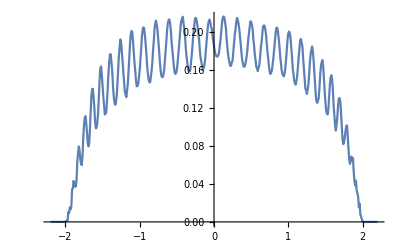

```mathematica
ListPlot[data3407,Joined->True]
```

```mathematica
ListPlot[data3407,Joined->True]
```

-Graphics-

```mathematica
ListPlot[data3407,Joined->True]
```

-Graphics-

```mathematica
data3405=Table[{ω,Mean[ParallelTable[TRA[ω,0,0],5000]]},{ω,Range[-2.2,2.2,0.01]}]
```

{{-2.2,1.29109×10^-19},{-2.19,4.23386×10^-19},{-2.18,1.54707×10^-18},{-2.17,6.19213×10^-18},{-2.16,3.03953×10^-17},{-2.15,1.88487×10^-16},{-2.14,1.91781×10^-15},{-2.13,6.45276×10^-14},{-2.12,1.8566×10^-9},{-2.11,6.50701×10^-12},{-2.1,1.90178×10^-11},{-2.09,1.83038×10^-13},{-2.08,3.58125×10^-13},{-2.07,2.50192×10^-12},{-2.06,1.4054×10^-12},{-2.05,8.65484×10^-13},{-2.04,7.97042×10^-13},{-2.03,2.18585×10^-12},{-2.02,6.46025×10^-12},{-2.01,4.08786×10^-11},{-2.,3.78041×10^-8},{-1.99,0.00360052},{-1.98,0.00119581},{-1.97,0.00230824},{-1.96,0.0265411},{-1.95,0.0124049},{-1.94,0.0188182},{-1.93,0.0152157},{-1.92,0.0203396},{-1.91,0.0542591},{-1.9,0.0460564},{-1.89,0.0506112},{-1.88,0.0431439},{-1.87,0.0368344},{-1.86,0.0380075},{-1.85,0.057306},{-1.84,0.086574},{-1.83,0.0879471},{-1.82,0.0880832},{-1.81,0.0759968},{-1.8,0.0651322},{-1.79,0.0584021},{-1.78,0.0619272},{-1.77,0.0813706},{-1.76,0.111152},{-1.75,0.126451},{-1.74,0.124477},{-1.73,0.114322},{-1.72,0.101135},{-1.71,0.0864172},{-1.7,0.0778067},{-1.69,0.0782936},{-1.68,0.0916718},{-1.67,0.116728},{-1.66,0.142227},{-1.65,0.153491},{-1.64,0.154234},{-1.63,0.141932},{-1.62,0.124682},{-1.61,0.110316},{-1.6,0.100175},{-1.59,0.0942146},{-1.58,0.100778},{-1.57,0.113108},{-1.56,0.133733},{-1.55,0.159037},{-1.54,0.171032},{-1.53,0.177261},{-1.52,0.17028},{-1.51,0.153126},{-1.5,0.137503},{-1.49,0.123837},{-1.48,0.114666},{-1.47,0.111097},{-1.46,0.114323},{-1.45,0.125347},{-1.44,0.142625},{-1.43,0.166573},{-1.42,0.181781},{-1.41,0.189522},{-1.4,0.1898},{-1.39,0.180635},{-1.38,0.164291},{-1.37,0.149386},{-1.36,0.135436},{-1.35,0.124342},{-1.34,0.121921},{-1.33,0.124355},{-1.32,0.132684},{-1.31,0.145631},{-1.3,0.163195},{-1.29,0.180229},{-1.28,0.19479},{-1.27,0.201224},{-1.26,0.201821},{-1.25,0.19057},{-1.24,0.174252},{-1.23,0.161916},{-1.22,0.147451},{-1.21,0.136344},{-1.2,0.133915},{-1.19,0.132374},{-1.18,0.13589},{-1.17,0.14661},{-1.16,0.159524},{-1.15,0.176938},{-1.14,0.191646},{-1.13,0.20373},{-1.12,0.209466},{-1.11,0.206767},{-1.1,0.198278},{-1.09,0.186553},{-1.08,0.171367},{-1.07,0.158441},{-1.06,0.149131},{-1.05,0.141569},{-1.04,0.140896},{-1.03,0.143372},{-1.02,0.147545},{-1.01,0.159787},{-1.,0.17259},{-0.99,0.188537},{-0.98,0.201982},{-0.97,0.209088},{-0.96,0.212482},{-0.95,0.2109},{-0.94,0.204917},{-0.93,0.192044},{-0.92,0.180381},{-0.91,0.165863},{-0.9,0.157084},{-0.89,0.152231},{-0.88,0.146967},{-0.87,0.14544},{-0.86,0.152012},{-0.85,0.160231},{-0.84,0.170342},{-0.83,0.184509},{-0.82,0.19819},{-0.81,0.20858},{-0.8,0.215648},{-0.79,0.217867},{-0.78,0.214926},{-0.77,0.206716},{-0.76,0.195969},{-0.75,0.181574},{-0.74,0.172248},{-0.73,0.163034},{-0.72,0.15498},{-0.71,0.152097},{-0.7,0.151463},{-0.69,0.155033},{-0.68,0.1608},{-0.67,0.171955},{-0.66,0.182489},{-0.65,0.196235},{-0.64,0.207414},{-0.63,0.217585},{-0.62,0.220202},{-0.61,0.218917},{-0.6,0.214278},{-0.59,0.205496},{-0.58,0.194067},{-0.57,0.180845},{-0.56,0.171833},{-0.55,0.163274},{-0.54,0.157207},{-0.53,0.155403},{-0.52,0.154741},{-0.51,0.160179},{-0.5,0.166041},{-0.49,0.176146},{-0.48,0.188105},{-0.47,0.199457},{-0.46,0.210138},{-0.45,0.218489},{-0.44,0.221686},{-0.43,0.220878},{-0.42,0.216157},{-0.41,0.207032},{-0.4,0.197211},{-0.39,0.186159},{-0.38,0.175714},{-0.37,0.167071},{-0.36,0.163918},{-0.35,0.158199},{-0.34,0.157391},{-0.33,0.160782},{-0.32,0.167588},{-0.31,0.175362},{-0.3,0.186203},{-0.29,0.198415},{-0.28,0.20843},{-0.27,0.215675},{-0.26,0.222233},{-0.25,0.221322},{-0.24,0.216769},{-0.23,0.210692},{-0.22,0.202494},{-0.21,0.190278},{-0.2,0.182613},{-0.19,0.173707},{-0.18,0.166793},{-0.17,0.161686},{-0.16,0.160137},{-0.15,0.159969},{-0.14,0.165556},{-0.13,0.171561},{-0.12,0.181287},{-0.11,0.192158},{-0.1,0.203849},{-0.09,0.215096},{-0.08,0.219204},{-0.07,0.221213},{-0.06,0.216903},{-0.05,0.212624},{-0.04,0.203651},{-0.03,0.194706},{-0.02,0.188974},{-0.01,0.183926},{0.,0.178183},{0.01,0.173958},{0.02,0.171453},{0.03,0.170722},{0.04,0.17295},{0.05,0.175162},{0.06,0.181056},{0.07,0.187549},{0.08,0.196974},{0.09,0.20611},{0.1,0.213884},{0.11,0.221562},{0.12,0.222435},{0.13,0.221034},{0.14,0.215978},{0.15,0.206049},{0.16,0.19663},{0.17,0.185215},{0.18,0.177861},{0.19,0.169121},{0.2,0.165081},{0.21,0.162331},{0.22,0.163162},{0.23,0.166116},{0.24,0.171531},{0.25,0.179469},{0.26,0.18849},{0.27,0.199105},{0.28,0.20985},{0.29,0.215701},{0.3,0.221405},{0.31,0.219772},{0.32,0.215886},{0.33,0.208224},{0.34,0.199579},{0.35,0.188193},{0.36,0.178698},{0.37,0.173331},{0.38,0.165799},{0.39,0.163158},{0.4,0.16114},{0.41,0.163404},{0.42,0.167249},{0.43,0.175455},{0.44,0.183986},{0.45,0.195801},{0.46,0.204368},{0.47,0.212511},{0.48,0.217914},{0.49,0.218561},{0.5,0.215459},{0.51,0.20755},{0.52,0.197418},{0.53,0.186579},{0.54,0.178752},{0.55,0.170171},{0.56,0.164929},{0.57,0.158758},{0.58,0.159854},{0.59,0.15993},{0.6,0.16455},{0.61,0.172781},{0.62,0.181776},{0.63,0.19224},{0.64,0.202935},{0.65,0.211564},{0.66,0.215003},{0.67,0.216275},{0.68,0.210254},{0.69,0.203271},{0.7,0.191804},{0.71,0.180327},{0.72,0.17194},{0.73,0.165375},{0.74,0.159494},{0.75,0.156087},{0.76,0.15681},{0.77,0.158595},{0.78,0.166616},{0.79,0.17439},{0.8,0.185264},{0.81,0.19538},{0.82,0.206003},{0.83,0.212112},{0.84,0.213642},{0.85,0.208934},{0.86,0.201492},{0.87,0.190231},{0.88,0.178767},{0.89,0.167564},{0.9,0.159131},{0.91,0.153373},{0.92,0.151707},{0.93,0.151455},{0.94,0.155437},{0.95,0.160463},{0.96,0.172017},{0.97,0.183369},{0.98,0.195388},{0.99,0.205431},{1.,0.212192},{1.01,0.210133},{1.02,0.203062},{1.03,0.190706},{1.04,0.179376},{1.05,0.16758},{1.06,0.155949},{1.07,0.148175},{1.08,0.144635},{1.09,0.142958},{1.1,0.145991},{1.11,0.154969},{1.12,0.164271},{1.13,0.179082},{1.14,0.189686},{1.15,0.197426},{1.16,0.202767},{1.17,0.201554},{1.18,0.191171},{1.19,0.180411},{1.2,0.166299},{1.21,0.152131},{1.22,0.143075},{1.23,0.137087},{1.24,0.13497},{1.25,0.136786},{1.26,0.143708},{1.27,0.152439},{1.28,0.167826},{1.29,0.182976},{1.3,0.195165},{1.31,0.194712},{1.32,0.190818},{1.33,0.177806},{1.34,0.165758},{1.35,0.15082},{1.36,0.137071},{1.37,0.12812},{1.38,0.124262},{1.39,0.12602},{1.4,0.132822},{1.41,0.143279},{1.42,0.158071},{1.43,0.173215},{1.44,0.18155},{1.45,0.18366},{1.46,0.17413},{1.47,0.160958},{1.48,0.144541},{1.49,0.12889},{1.5,0.116343},{1.51,0.110308},{1.52,0.111719},{1.53,0.117861},{1.54,0.134314},{1.55,0.151787},{1.56,0.167743},{1.57,0.168591},{1.58,0.162379},{1.59,0.147777},{1.6,0.131713},{1.61,0.115162},{1.62,0.101818},{1.63,0.0954826},{1.64,0.0959843},{1.65,0.108139},{1.66,0.125111},{1.67,0.14402},{1.68,0.147022},{1.69,0.141847},{1.7,0.127291},{1.71,0.108457},{1.72,0.0938359},{1.73,0.0810015},{1.74,0.0770269},{1.75,0.0874125},{1.76,0.105056},{1.77,0.11473},{1.78,0.11548},{1.79,0.106094},{1.8,0.0879266},{1.81,0.07049},{1.82,0.0595658},{1.83,0.0591566},{1.84,0.0757615},{1.85,0.0824112},{1.86,0.0752189},{1.87,0.0716422},{1.88,0.0532727},{1.89,0.0390135},{1.9,0.0376773},{1.91,0.0550868},{1.92,0.0378029},{1.93,0.032289},{1.94,0.0260117},{1.95,0.0144204},{1.96,0.0301037},{1.97,0.00786004},{1.98,0.00615826},{1.99,0.00578495},{2.,2.78303×10^-6},{2.01,2.46183×10^-8},{2.02,4.88216×10^-9},{2.03,3.16602×10^-8},{2.04,7.03925×10^-9},{2.05,1.12086×10^-8},{2.06,1.08002×10^-8},{2.07,1.10159×10^-9},{2.08,1.35028×10^-10},{2.09,2.00012×10^-10},{2.1,3.04687×10^-10},{2.11,4.12762×10^-10},{2.12,2.49696×10^-8},{2.13,6.9749×10^-10},{2.14,6.85479×10^-11},{2.15,3.63326×10^-12},{2.16,1.06101×10^-13},{2.17,1.56746×10^-13},{2.18,8.60354×10^-15},{2.19,2.04085×10^-15},{2.2,4.51752×10^-16}}

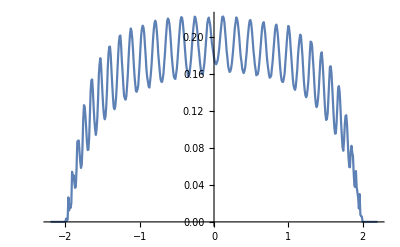

```mathematica
ListPlot[data3405,Joined->True]
```

```mathematica
data3425=Table[{ω,Mean[ParallelTable[TRA[ω,0,0],5000]]},{ω,Range[-2.2,2.2,0.01]}]
```

{{-2.2,8.70025×10^-22},{-2.19,2.47176×10^-21},{-2.18,7.3577×10^-21},{-2.17,2.36101×10^-20},{-2.16,8.76151×10^-20},{-2.15,3.52733×10^-19},{-2.14,1.89354×10^-18},{-2.13,2.09117×10^-17},{-2.12,3.08639×10^-14},{-2.11,2.56666×10^-13},{-2.1,5.06656×10^-14},{-2.09,3.76294×10^-14},{-2.08,1.60727×10^-14},{-2.07,1.01306×10^-12},{-2.06,2.86244×10^-12},{-2.05,3.55438×10^-13},{-2.04,4.64897×10^-13},{-2.03,4.09418×10^-13},{-2.02,4.50023×10^-13},{-2.01,1.86247×10^-12},{-2.,5.90952×10^-11},{-1.99,1.30385×10^-7},{-1.98,1.39632×10^-6},{-1.97,7.07087×10^-6},{-1.96,0.0000404455},{-1.95,0.0000764993},{-1.94,0.000279489},{-1.93,0.000497654},{-1.92,0.000966644},{-1.91,0.00166974},{-1.9,0.00255068},{-1.89,0.0033443},{-1.88,0.00508874},{-1.87,0.00673474},{-1.86,0.00817113},{-1.85,0.0109345},{-1.84,0.012206},{-1.83,0.0145322},{-1.82,0.0168289},{-1.81,0.0195707},{-1.8,0.0230373},{-1.79,0.0254205},{-1.78,0.0300954},{-1.77,0.0316339},{-1.76,0.0346699},{-1.75,0.0365246},{-1.74,0.0387012},{-1.73,0.0414862},{-1.72,0.0454977},{-1.71,0.0483653},{-1.7,0.0519257},{-1.69,0.0510381},{-1.68,0.0592588},{-1.67,0.0600157},{-1.66,0.0632939},{-1.65,0.0643529},{-1.64,0.0646368},{-1.63,0.0635448},{-1.62,0.0689216},{-1.61,0.0700665},{-1.6,0.0765004},{-1.59,0.0788348},{-1.58,0.0817937},{-1.57,0.0852394},{-1.56,0.087024},{-1.55,0.0867105},{-1.54,0.0861523},{-1.53,0.0848567},{-1.52,0.0864711},{-1.51,0.0896263},{-1.5,0.0920485},{-1.49,0.0944631},{-1.48,0.0976896},{-1.47,0.101905},{-1.46,0.106735},{-1.45,0.107884},{-1.44,0.109137},{-1.43,0.106606},{-1.42,0.10429},{-1.41,0.104071},{-1.4,0.103162},{-1.39,0.100716},{-1.38,0.107038},{-1.37,0.109133},{-1.36,0.112101},{-1.35,0.116468},{-1.34,0.124366},{-1.33,0.123287},{-1.32,0.128885},{-1.31,0.125688},{-1.3,0.126215},{-1.29,0.125648},{-1.28,0.120178},{-1.27,0.118256},{-1.26,0.115531},{-1.25,0.119868},{-1.24,0.122731},{-1.23,0.123275},{-1.22,0.129767},{-1.21,0.133321},{-1.2,0.138838},{-1.19,0.141139},{-1.18,0.140227},{-1.17,0.145572},{-1.16,0.139714},{-1.15,0.137305},{-1.14,0.133188},{-1.13,0.129704},{-1.12,0.127193},{-1.11,0.127929},{-1.1,0.131887},{-1.09,0.134067},{-1.08,0.134616},{-1.07,0.141985},{-1.06,0.145745},{-1.05,0.152808},{-1.04,0.151164},{-1.03,0.156183},{-1.02,0.152832},{-1.01,0.154156},{-1.,0.145426},{-0.99,0.141964},{-0.98,0.141638},{-0.97,0.13545},{-0.96,0.134762},{-0.95,0.133224},{-0.94,0.135388},{-0.93,0.142782},{-0.92,0.145989},{-0.91,0.148431},{-0.9,0.155397},{-0.89,0.158511},{-0.88,0.163565},{-0.87,0.161021},{-0.86,0.16279},{-0.85,0.161249},{-0.84,0.157085},{-0.83,0.150755},{-0.82,0.147333},{-0.81,0.14375},{-0.8,0.139327},{-0.79,0.138258},{-0.78,0.140647},{-0.77,0.143257},{-0.76,0.147296},{-0.75,0.151588},{-0.74,0.159633},{-0.73,0.159961},{-0.72,0.166324},{-0.71,0.170616},{-0.7,0.170626},{-0.69,0.167321},{-0.68,0.170095},{-0.67,0.16089},{-0.66,0.160537},{-0.65,0.154962},{-0.64,0.149035},{-0.63,0.145756},{-0.62,0.145602},{-0.61,0.148296},{-0.6,0.146811},{-0.59,0.151906},{-0.58,0.151419},{-0.57,0.1606},{-0.56,0.165923},{-0.55,0.171355},{-0.54,0.173846},{-0.53,0.175967},{-0.52,0.175476},{-0.51,0.174955},{-0.5,0.173283},{-0.49,0.165887},{-0.48,0.164751},{-0.47,0.156652},{-0.46,0.153422},{-0.45,0.149252},{-0.44,0.14923},{-0.43,0.150455},{-0.42,0.151101},{-0.41,0.156629},{-0.4,0.159576},{-0.39,0.162696},{-0.38,0.167717},{-0.37,0.172392},{-0.36,0.17671},{-0.35,0.176919},{-0.34,0.17923},{-0.33,0.178428},{-0.32,0.176543},{-0.31,0.172522},{-0.3,0.169056},{-0.29,0.162999},{-0.28,0.163228},{-0.27,0.154565},{-0.26,0.148593},{-0.25,0.153069},{-0.24,0.152056},{-0.23,0.155541},{-0.22,0.158796},{-0.21,0.163513},{-0.2,0.166319},{-0.19,0.169568},{-0.18,0.176055},{-0.17,0.178682},{-0.16,0.178937},{-0.15,0.180784},{-0.14,0.17729},{-0.13,0.176156},{-0.12,0.170773},{-0.11,0.1656},{-0.1,0.165191},{-0.09,0.160321},{-0.08,0.157169},{-0.07,0.154851},{-0.06,0.153682},{-0.05,0.157991},{-0.04,0.16127},{-0.03,0.164128},{-0.02,0.170095},{-0.01,0.17516},{0.,0.175974},{0.01,0.181667},{0.02,0.187647},{0.03,0.185076},{0.04,0.184113},{0.05,0.185336},{0.06,0.184815},{0.07,0.18206},{0.08,0.182524},{0.09,0.177751},{0.1,0.177727},{0.11,0.170806},{0.12,0.171704},{0.13,0.170887},{0.14,0.170235},{0.15,0.168576},{0.16,0.170047},{0.17,0.175047},{0.18,0.179293},{0.19,0.183123},{0.2,0.183149},{0.21,0.185857},{0.22,0.185262},{0.23,0.183469},{0.24,0.180069},{0.25,0.174944},{0.26,0.173706},{0.27,0.168838},{0.28,0.16246},{0.29,0.162369},{0.3,0.160389},{0.31,0.159372},{0.32,0.160321},{0.33,0.16057},{0.34,0.164322},{0.35,0.166737},{0.36,0.169528},{0.37,0.171919},{0.38,0.178804},{0.39,0.176087},{0.4,0.178757},{0.41,0.177649},{0.42,0.174698},{0.43,0.172861},{0.44,0.170395},{0.45,0.169003},{0.46,0.164639},{0.47,0.161587},{0.48,0.159837},{0.49,0.157899},{0.5,0.158141},{0.51,0.158799},{0.52,0.161273},{0.53,0.164053},{0.54,0.165051},{0.55,0.169188},{0.56,0.16988},{0.57,0.174331},{0.58,0.17236},{0.59,0.169869},{0.6,0.172252},{0.61,0.167169},{0.62,0.163518},{0.63,0.166102},{0.64,0.160392},{0.65,0.157928},{0.66,0.157546},{0.67,0.154859},{0.68,0.157799},{0.69,0.157089},{0.7,0.161323},{0.71,0.159593},{0.72,0.163317},{0.73,0.164061},{0.74,0.167761},{0.75,0.169431},{0.76,0.169421},{0.77,0.166245},{0.78,0.164264},{0.79,0.163947},{0.8,0.159925},{0.81,0.159507},{0.82,0.155326},{0.83,0.154666},{0.84,0.15268},{0.85,0.150717},{0.86,0.15303},{0.87,0.153543},{0.88,0.15666},{0.89,0.156695},{0.9,0.164149},{0.91,0.160552},{0.92,0.164656},{0.93,0.161169},{0.94,0.162296},{0.95,0.159589},{0.96,0.154849},{0.97,0.149824},{0.98,0.151288},{0.99,0.147888},{1.,0.146482},{1.01,0.148559},{1.02,0.146899},{1.03,0.146508},{1.04,0.150292},{1.05,0.150907},{1.06,0.152365},{1.07,0.152865},{1.08,0.156018},{1.09,0.154857},{1.1,0.155384},{1.11,0.153127},{1.12,0.149432},{1.13,0.144181},{1.14,0.144148},{1.15,0.139334},{1.16,0.137329},{1.17,0.137279},{1.18,0.136285},{1.19,0.141175},{1.2,0.141457},{1.21,0.143376},{1.22,0.144972},{1.23,0.146267},{1.24,0.144404},{1.25,0.143893},{1.26,0.143433},{1.27,0.142073},{1.28,0.135515},{1.29,0.134541},{1.3,0.129052},{1.31,0.129275},{1.32,0.12583},{1.33,0.130253},{1.34,0.126368},{1.35,0.127875},{1.36,0.133528},{1.37,0.134293},{1.38,0.134359},{1.39,0.13396},{1.4,0.132695},{1.41,0.128743},{1.42,0.129583},{1.43,0.123183},{1.44,0.118399},{1.45,0.116862},{1.46,0.115583},{1.47,0.112263},{1.48,0.114249},{1.49,0.113563},{1.5,0.116652},{1.51,0.118699},{1.52,0.118224},{1.53,0.116076},{1.54,0.111758},{1.55,0.113955},{1.56,0.110472},{1.57,0.106395},{1.58,0.102834},{1.59,0.102455},{1.6,0.101068},{1.61,0.0975723},{1.62,0.100719},{1.63,0.10082},{1.64,0.0981627},{1.65,0.0974262},{1.66,0.0963519},{1.67,0.0950078},{1.68,0.0913244},{1.69,0.0884409},{1.7,0.0836595},{1.71,0.079192},{1.72,0.0822839},{1.73,0.0781003},{1.74,0.0759},{1.75,0.0770327},{1.76,0.0757463},{1.77,0.0727904},{1.78,0.0695477},{1.79,0.0666218},{1.8,0.0653726},{1.81,0.0599839},{1.82,0.0583978},{1.83,0.0539403},{1.84,0.0520794},{1.85,0.0491285},{1.86,0.0464752},{1.87,0.0423425},{1.88,0.0419896},{1.89,0.0380298},{1.9,0.0345164},{1.91,0.0292858},{1.92,0.0260398},{1.93,0.0227665},{1.94,0.0201243},{1.95,0.0166967},{1.96,0.0127548},{1.97,0.0104957},{1.98,0.00680424},{1.99,0.0042109},{2.,0.000104852},{2.01,5.96546×10^-7},{2.02,3.66501×10^-7},{2.03,6.36915×10^-7},{2.04,1.61019×10^-7},{2.05,1.04064×10^-7},{2.06,1.39353×10^-7},{2.07,1.36273×10^-7},{2.08,1.31964×10^-7},{2.09,2.7402×10^-8},{2.1,7.2218×10^-8},{2.11,4.06224×10^-8},{2.12,7.69489×10^-8},{2.13,3.30895×10^-8},{2.14,1.89852×10^-8},{2.15,1.15693×10^-8},{2.16,4.22876×10^-8},{2.17,5.29852×10^-9},{2.18,8.87522×10^-9},{2.19,3.7342×10^-9},{2.2,1.70925×10^-9}}

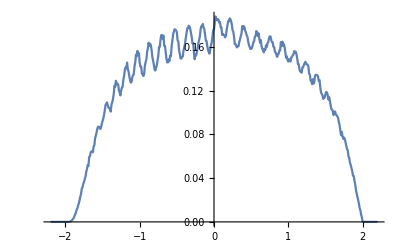

```mathematica
ListPlot[data3425,Joined->True]
```

```mathematica
15
```

```mathematica
data3415=Table[{ω,Mean[ParallelTable[TRA[ω,0,0],5000]]},{ω,Range[-2.2,2.2,0.01]}]
```

{{-2.2,9.30982×10^-21},{-2.19,2.729×10^-20},{-2.18,9.46347×10^-20},{-2.17,3.18563×10^-19},{-2.16,1.36357×10^-18},{-2.15,6.90116×10^-18},{-2.14,4.67132×10^-17},{-2.13,7.95089×10^-16},{-2.12,2.28078×10^-11},{-2.11,1.19324×10^-12},{-2.1,9.50673×10^-13},{-2.09,9.06845×10^-14},{-2.08,8.2062×10^-14},{-2.07,9.07856×10^-12},{-2.06,5.89029×10^-12},{-2.05,4.60366×10^-13},{-2.04,5.28991×10^-13},{-2.03,6.04×10^-13},{-2.02,1.8409×10^-12},{-2.01,4.91901×10^-12},{-2.,1.21221×10^-9},{-1.99,3.37619×10^-6},{-1.98,0.0000788666},{-1.97,0.000283626},{-1.96,0.000700013},{-1.95,0.00167908},{-1.94,0.00309174},{-1.93,0.00442587},{-1.92,0.00623742},{-1.91,0.0080172},{-1.9,0.011955},{-1.89,0.0153806},{-1.88,0.0195172},{-1.87,0.0219813},{-1.86,0.0244649},{-1.85,0.0264813},{-1.84,0.0302259},{-1.83,0.0340538},{-1.82,0.0397877},{-1.81,0.0438104},{-1.8,0.0483045},{-1.79,0.053443},{-1.78,0.0531123},{-1.77,0.0539609},{-1.76,0.0557999},{-1.75,0.0565407},{-1.74,0.0617391},{-1.73,0.069113},{-1.72,0.0745997},{-1.71,0.0799219},{-1.7,0.0809331},{-1.69,0.0796664},{-1.68,0.0794262},{-1.67,0.076997},{-1.66,0.0771265},{-1.65,0.0844106},{-1.64,0.0849008},{-1.63,0.0944826},{-1.62,0.101648},{-1.61,0.103245},{-1.6,0.109657},{-1.59,0.10561},{-1.58,0.103972},{-1.57,0.0988045},{-1.56,0.0947552},{-1.55,0.0985224},{-1.54,0.0991726},{-1.53,0.103071},{-1.52,0.112691},{-1.51,0.119702},{-1.5,0.127605},{-1.49,0.129422},{-1.48,0.126899},{-1.47,0.125259},{-1.46,0.119908},{-1.45,0.115301},{-1.44,0.111172},{-1.43,0.10881},{-1.42,0.11046},{-1.41,0.118418},{-1.4,0.126049},{-1.39,0.13398},{-1.38,0.141208},{-1.37,0.142285},{-1.36,0.145164},{-1.35,0.149352},{-1.34,0.13877},{-1.33,0.139556},{-1.32,0.129246},{-1.31,0.124121},{-1.3,0.120504},{-1.29,0.122994},{-1.28,0.126271},{-1.27,0.131915},{-1.26,0.141912},{-1.25,0.147931},{-1.24,0.158513},{-1.23,0.160202},{-1.22,0.165128},{-1.21,0.160341},{-1.2,0.157324},{-1.19,0.147862},{-1.18,0.142562},{-1.17,0.138363},{-1.16,0.13445},{-1.15,0.131796},{-1.14,0.135564},{-1.13,0.138742},{-1.12,0.144882},{-1.11,0.153284},{-1.1,0.160653},{-1.09,0.168533},{-1.08,0.172706},{-1.07,0.172892},{-1.06,0.174733},{-1.05,0.167992},{-1.04,0.162185},{-1.03,0.153209},{-1.02,0.14684},{-1.01,0.143032},{-1.,0.140226},{-0.99,0.140246},{-0.98,0.139804},{-0.97,0.148475},{-0.96,0.153931},{-0.95,0.162669},{-0.94,0.16901},{-0.93,0.174191},{-0.92,0.180559},{-0.91,0.183738},{-0.9,0.179268},{-0.89,0.174771},{-0.88,0.168402},{-0.87,0.160021},{-0.86,0.155689},{-0.85,0.148827},{-0.84,0.145703},{-0.83,0.141778},{-0.82,0.145434},{-0.81,0.149618},{-0.8,0.156},{-0.79,0.163352},{-0.78,0.172658},{-0.77,0.178467},{-0.76,0.184518},{-0.75,0.18756},{-0.74,0.187473},{-0.73,0.184496},{-0.72,0.181318},{-0.71,0.174971},{-0.7,0.16627},{-0.69,0.160956},{-0.68,0.156773},{-0.67,0.151064},{-0.66,0.149982},{-0.65,0.148584},{-0.64,0.154846},{-0.63,0.15755},{-0.62,0.163775},{-0.61,0.173117},{-0.6,0.17857},{-0.59,0.186151},{-0.58,0.189024},{-0.57,0.191169},{-0.56,0.190594},{-0.55,0.186867},{-0.54,0.180969},{-0.53,0.177501},{-0.52,0.169249},{-0.51,0.164209},{-0.5,0.15834},{-0.49,0.154335},{-0.48,0.151997},{-0.47,0.154297},{-0.46,0.154703},{-0.45,0.164011},{-0.44,0.168964},{-0.43,0.176306},{-0.42,0.181925},{-0.41,0.188311},{-0.4,0.191003},{-0.39,0.193774},{-0.38,0.193013},{-0.37,0.189084},{-0.36,0.184748},{-0.35,0.181765},{-0.34,0.1726},{-0.33,0.167724},{-0.32,0.162757},{-0.31,0.160757},{-0.3,0.152184},{-0.29,0.15355},{-0.28,0.159149},{-0.27,0.162366},{-0.26,0.170228},{-0.25,0.173078},{-0.24,0.178393},{-0.23,0.189278},{-0.22,0.19147},{-0.21,0.192633},{-0.2,0.192338},{-0.19,0.194129},{-0.18,0.188019},{-0.17,0.184425},{-0.16,0.178884},{-0.15,0.172404},{-0.14,0.165907},{-0.13,0.166112},{-0.12,0.158984},{-0.11,0.157931},{-0.1,0.158334},{-0.09,0.160535},{-0.08,0.166548},{-0.07,0.170866},{-0.06,0.179095},{-0.05,0.184964},{-0.04,0.19058},{-0.03,0.192782},{-0.02,0.193725},{-0.01,0.196732},{0.,0.194604},{0.01,0.193037},{0.02,0.190068},{0.03,0.1867},{0.04,0.183571},{0.05,0.179875},{0.06,0.17598},{0.07,0.174788},{0.08,0.170924},{0.09,0.171159},{0.1,0.173908},{0.11,0.177189},{0.12,0.179995},{0.13,0.183883},{0.14,0.190067},{0.15,0.195429},{0.16,0.19793},{0.17,0.197589},{0.18,0.198264},{0.19,0.195486},{0.2,0.189293},{0.21,0.181535},{0.22,0.177388},{0.23,0.172854},{0.24,0.168633},{0.25,0.163182},{0.26,0.163137},{0.27,0.161881},{0.28,0.165481},{0.29,0.166678},{0.3,0.172603},{0.31,0.174968},{0.32,0.18239},{0.33,0.187574},{0.34,0.19058},{0.35,0.194657},{0.36,0.191735},{0.37,0.189711},{0.38,0.185421},{0.39,0.181847},{0.4,0.17616},{0.41,0.172139},{0.42,0.171539},{0.43,0.162241},{0.44,0.162529},{0.45,0.164217},{0.46,0.163514},{0.47,0.164195},{0.48,0.16723},{0.49,0.175736},{0.5,0.180284},{0.51,0.182362},{0.52,0.186025},{0.53,0.191035},{0.54,0.189768},{0.55,0.18886},{0.56,0.182695},{0.57,0.177856},{0.58,0.174359},{0.59,0.169133},{0.6,0.165266},{0.61,0.16275},{0.62,0.160889},{0.63,0.159651},{0.64,0.158822},{0.65,0.164016},{0.66,0.16776},{0.67,0.170574},{0.68,0.175963},{0.69,0.180722},{0.7,0.184494},{0.71,0.185872},{0.72,0.183999},{0.73,0.182705},{0.74,0.17872},{0.75,0.171919},{0.76,0.166346},{0.77,0.1624},{0.78,0.159708},{0.79,0.155603},{0.8,0.156473},{0.81,0.15722},{0.82,0.15879},{0.83,0.162937},{0.84,0.166809},{0.85,0.171307},{0.86,0.177092},{0.87,0.178448},{0.88,0.181093},{0.89,0.180503},{0.9,0.175221},{0.91,0.174606},{0.92,0.168232},{0.93,0.162475},{0.94,0.158674},{0.95,0.156503},{0.96,0.151217},{0.97,0.151201},{0.98,0.15394},{0.99,0.152257},{1.,0.160292},{1.01,0.165523},{1.02,0.16734},{1.03,0.171678},{1.04,0.172366},{1.05,0.171819},{1.06,0.168281},{1.07,0.166356},{1.08,0.160554},{1.09,0.155959},{1.1,0.149679},{1.11,0.145743},{1.12,0.143826},{1.13,0.14208},{1.14,0.145083},{1.15,0.150025},{1.16,0.149977},{1.17,0.157455},{1.18,0.161789},{1.19,0.162427},{1.2,0.164863},{1.21,0.165257},{1.22,0.162482},{1.23,0.154768},{1.24,0.151291},{1.25,0.143373},{1.26,0.139501},{1.27,0.136951},{1.28,0.133412},{1.29,0.135198},{1.3,0.137481},{1.31,0.140624},{1.32,0.147514},{1.33,0.151711},{1.34,0.153472},{1.35,0.154449},{1.36,0.154079},{1.37,0.149048},{1.38,0.142257},{1.39,0.13871},{1.4,0.131348},{1.41,0.129701},{1.42,0.124676},{1.43,0.121368},{1.44,0.12543},{1.45,0.129626},{1.46,0.131527},{1.47,0.135717},{1.48,0.139229},{1.49,0.141714},{1.5,0.134929},{1.51,0.130167},{1.52,0.126079},{1.53,0.119898},{1.54,0.113977},{1.55,0.11277},{1.56,0.11143},{1.57,0.112099},{1.58,0.114306},{1.59,0.116068},{1.6,0.119412},{1.61,0.121878},{1.62,0.120434},{1.63,0.112391},{1.64,0.107316},{1.65,0.101078},{1.66,0.0966103},{1.67,0.0933356},{1.68,0.0906324},{1.69,0.0911948},{1.7,0.0950365},{1.71,0.0979697},{1.72,0.09565},{1.73,0.0939298},{1.74,0.0888262},{1.75,0.0841747},{1.76,0.0797114},{1.77,0.0758461},{1.78,0.0746969},{1.79,0.0714823},{1.8,0.0734943},{1.81,0.0685062},{1.82,0.068235},{1.83,0.0617799},{1.84,0.0586721},{1.85,0.0535787},{1.86,0.0497119},{1.87,0.047233},{1.88,0.0439573},{1.89,0.0417832},{1.9,0.0358077},{1.91,0.0327303},{1.92,0.0273458},{1.93,0.0241933},{1.94,0.0216801},{1.95,0.015518},{1.96,0.0122758},{1.97,0.00861641},{1.98,0.00490238},{1.99,0.00233067},{2.,0.0000277852},{2.01,1.90792×10^-7},{2.02,1.25705×10^-7},{2.03,2.0634×10^-7},{2.04,7.59382×10^-8},{2.05,7.24038×10^-8},{2.06,4.61925×10^-8},{2.07,1.96852×10^-8},{2.08,1.93502×10^-8},{2.09,6.6483×10^-9},{2.1,2.32908×10^-8},{2.11,1.72506×10^-8},{2.12,3.7802×10^-8},{2.13,1.24228×10^-8},{2.14,1.23705×10^-8},{2.15,5.92879×10^-9},{2.16,8.34921×10^-10},{2.17,1.26165×10^-9},{2.18,1.56112×10^-10},{2.19,2.07367×10^-11},{2.2,6.39541×10^-12}}

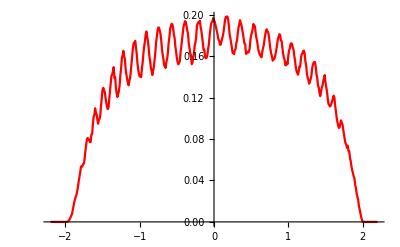

```mathematica
ListPlot[data3415,Joined->True,PlotStyle->Red]
```

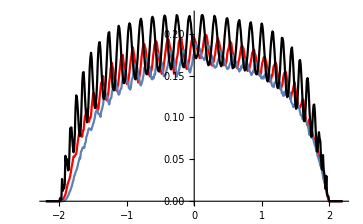

```mathematica
Show[%1193,%1191,ListPlot[data3405,Joined->True,PlotStyle->Black],PlotRange->All]
```

```mathematica
5imps
```

```mathematica
Table[{ω,Mean[ParallelTable[TRA[ω,0,0],5000]]},{ω,Range[-2.2,2.2,0.01]}]
```

{{-2.2,2.56489×10^-46},{-2.19,3.39458×10^-45},{-2.18,5.01588×10^-44},{-2.17,8.84639×10^-43},{-2.16,1.93686×10^-41},{-2.15,5.72016×10^-40},{-2.14,2.80753×10^-38},{-2.13,4.77095×10^-36},{-2.12,7.82484×10^-31},{-2.11,1.85505×10^-32},{-2.1,3.16554×10^-30},{-2.09,2.88639×10^-32},{-2.08,4.67631×10^-31},{-2.07,2.73915×10^-29},{-2.06,1.44829×10^-28},{-2.05,3.90547×10^-27},{-2.04,1.86522×10^-26},{-2.03,1.37865×10^-24},{-2.02,1.28005×10^-22},{-2.01,7.10462×10^-20},{-2.,4.33794×10^-13},{-1.99,4.19438×10^-7},{-1.98,7.514×10^-6},{-1.97,0.0000405557},{-1.96,0.000511844},{-1.95,0.00071801},{-1.94,0.00145257},{-1.93,0.00161081},{-1.92,0.00245742},{-1.91,0.00627589},{-1.9,0.00746247},{-1.89,0.00999154},{-1.88,0.00900745},{-1.87,0.00848416},{-1.86,0.0101694},{-1.85,0.0166639},{-1.84,0.0235753},{-1.83,0.0271191},{-1.82,0.0284036},{-1.81,0.024407},{-1.8,0.0224974},{-1.79,0.021004},{-1.78,0.0243241},{-1.77,0.0333399},{-1.76,0.0450999},{-1.75,0.0509636},{-1.74,0.0526148},{-1.73,0.0494443},{-1.72,0.043596},{-1.71,0.0377646},{-1.7,0.0362833},{-1.69,0.0394312},{-1.68,0.0458511},{-1.67,0.0591336},{-1.66,0.072649},{-1.65,0.0797278},{-1.64,0.0791099},{-1.63,0.0725305},{-1.62,0.0648803},{-1.61,0.0573828},{-1.6,0.0533365},{-1.59,0.0511055},{-1.58,0.0552709},{-1.57,0.0640875},{-1.56,0.0791415},{-1.55,0.0925409},{-1.54,0.101197},{-1.53,0.103581},{-1.52,0.0982479},{-1.51,0.0885183},{-1.5,0.0794581},{-1.49,0.0722801},{-1.48,0.067039},{-1.47,0.0669849},{-1.46,0.0700565},{-1.45,0.0783006},{-1.44,0.0901006},{-1.43,0.103581},{-1.42,0.117156},{-1.41,0.121969},{-1.4,0.121085},{-1.39,0.114857},{-1.38,0.104096},{-1.37,0.0953493},{-1.36,0.0863483},{-1.35,0.081738},{-1.34,0.0800658},{-1.33,0.0821736},{-1.32,0.0880924},{-1.31,0.098452},{-1.3,0.111787},{-1.29,0.124734},{-1.28,0.135056},{-1.27,0.137754},{-1.26,0.136821},{-1.25,0.128386},{-1.24,0.118165},{-1.23,0.1091},{-1.22,0.100103},{-1.21,0.0946292},{-1.2,0.0911838},{-1.19,0.0918704},{-1.18,0.0969555},{-1.17,0.104434},{-1.16,0.114815},{-1.15,0.127778},{-1.14,0.138787},{-1.13,0.146521},{-1.12,0.150246},{-1.11,0.147193},{-1.1,0.140872},{-1.09,0.131558},{-1.08,0.121247},{-1.07,0.111954},{-1.06,0.105205},{-1.05,0.101641},{-1.04,0.101437},{-1.03,0.103574},{-1.02,0.109224},{-1.01,0.117373},{-1.,0.128704},{-0.99,0.139272},{-0.98,0.14964},{-0.97,0.15789},{-0.96,0.158987},{-0.95,0.156484},{-0.94,0.149545},{-0.93,0.141078},{-0.92,0.130967},{-0.91,0.122353},{-0.9,0.115389},{-0.89,0.110083},{-0.88,0.109122},{-0.87,0.110254},{-0.86,0.113905},{-0.85,0.121731},{-0.84,0.131666},{-0.83,0.142602},{-0.82,0.151661},{-0.81,0.160897},{-0.8,0.166987},{-0.79,0.165623},{-0.78,0.162707},{-0.77,0.155411},{-0.76,0.146514},{-0.75,0.136632},{-0.74,0.128864},{-0.73,0.12085},{-0.72,0.117108},{-0.71,0.115209},{-0.7,0.115562},{-0.69,0.119629},{-0.68,0.12613},{-0.67,0.134063},{-0.66,0.145033},{-0.65,0.154933},{-0.64,0.164266},{-0.63,0.169632},{-0.62,0.17273},{-0.61,0.169817},{-0.6,0.165052},{-0.59,0.155036},{-0.58,0.14664},{-0.57,0.137615},{-0.56,0.129409},{-0.55,0.125206},{-0.54,0.121061},{-0.53,0.119956},{-0.52,0.121026},{-0.51,0.124647},{-0.5,0.132135},{-0.49,0.140829},{-0.48,0.150763},{-0.47,0.160572},{-0.46,0.16929},{-0.45,0.174568},{-0.44,0.176552},{-0.43,0.173465},{-0.42,0.16809},{-0.41,0.160213},{-0.4,0.151605},{-0.39,0.142483},{-0.38,0.134778},{-0.37,0.129328},{-0.36,0.124991},{-0.35,0.123649},{-0.34,0.124763},{-0.33,0.127903},{-0.32,0.132861},{-0.31,0.140883},{-0.3,0.150855},{-0.29,0.161573},{-0.28,0.169113},{-0.27,0.175453},{-0.26,0.1798},{-0.25,0.178306},{-0.24,0.173776},{-0.23,0.166274},{-0.22,0.156872},{-0.21,0.148284},{-0.2,0.140559},{-0.19,0.133804},{-0.18,0.12895},{-0.17,0.126151},{-0.16,0.126618},{-0.15,0.127776},{-0.14,0.132586},{-0.13,0.138498},{-0.12,0.148274},{-0.11,0.157241},{-0.1,0.1661},{-0.09,0.17402},{-0.08,0.179311},{-0.07,0.180978},{-0.06,0.179551},{-0.05,0.171297},{-0.04,0.163546},{-0.03,0.153826},{-0.02,0.144092},{-0.01,0.135899},{0.,0.130294},{0.01,0.125999},{0.02,0.124492},{0.03,0.125091},{0.04,0.12683},{0.05,0.13082},{0.06,0.138281},{0.07,0.147824},{0.08,0.159301},{0.09,0.168356},{0.1,0.17721},{0.11,0.180172},{0.12,0.181597},{0.13,0.176048},{0.14,0.169839},{0.15,0.16197},{0.16,0.153649},{0.17,0.145528},{0.18,0.137824},{0.19,0.131994},{0.2,0.127242},{0.21,0.126044},{0.22,0.127001},{0.23,0.129872},{0.24,0.135766},{0.25,0.144343},{0.26,0.153293},{0.27,0.163873},{0.28,0.172167},{0.29,0.179722},{0.3,0.180202},{0.31,0.178422},{0.32,0.173168},{0.33,0.165655},{0.34,0.156542},{0.35,0.148378},{0.36,0.139865},{0.37,0.132788},{0.38,0.127907},{0.39,0.126117},{0.4,0.124017},{0.41,0.126714},{0.42,0.132033},{0.43,0.137527},{0.44,0.146239},{0.45,0.15714},{0.46,0.166506},{0.47,0.174086},{0.48,0.178154},{0.49,0.179231},{0.5,0.172949},{0.51,0.166506},{0.52,0.156557},{0.53,0.148056},{0.54,0.138354},{0.55,0.13098},{0.56,0.125842},{0.57,0.122578},{0.58,0.121383},{0.59,0.12318},{0.6,0.12716},{0.61,0.13494},{0.62,0.143065},{0.63,0.153169},{0.64,0.163308},{0.65,0.171808},{0.66,0.175479},{0.67,0.174615},{0.68,0.170282},{0.69,0.161866},{0.7,0.152023},{0.71,0.142386},{0.72,0.134133},{0.73,0.126483},{0.74,0.120465},{0.75,0.117103},{0.76,0.117371},{0.77,0.120004},{0.78,0.12554},{0.79,0.133356},{0.8,0.142935},{0.81,0.153743},{0.82,0.162732},{0.83,0.169005},{0.84,0.171288},{0.85,0.167456},{0.86,0.160796},{0.87,0.149941},{0.88,0.139964},{0.89,0.128835},{0.9,0.121013},{0.91,0.115026},{0.92,0.112157},{0.93,0.111812},{0.94,0.114114},{0.95,0.119451},{0.96,0.126417},{0.97,0.139094},{0.98,0.148633},{0.99,0.157022},{1.,0.163113},{1.01,0.164014},{1.02,0.158958},{1.03,0.149531},{1.04,0.137391},{1.05,0.128092},{1.06,0.117492},{1.07,0.109711},{1.08,0.106303},{1.09,0.103376},{1.1,0.105805},{1.11,0.111008},{1.12,0.118556},{1.13,0.128894},{1.14,0.140617},{1.15,0.149962},{1.16,0.154367},{1.17,0.154924},{1.18,0.147456},{1.19,0.13798},{1.2,0.125325},{1.21,0.113557},{1.22,0.104147},{1.23,0.0979207},{1.24,0.0953998},{1.25,0.0959676},{1.26,0.0994068},{1.27,0.108529},{1.28,0.119202},{1.29,0.130235},{1.3,0.1379},{1.31,0.142496},{1.32,0.140389},{1.33,0.133622},{1.34,0.121156},{1.35,0.109112},{1.36,0.0989931},{1.37,0.0895517},{1.38,0.0861294},{1.39,0.0845547},{1.4,0.0872502},{1.41,0.0950111},{1.42,0.106244},{1.43,0.116724},{1.44,0.125113},{1.45,0.126409},{1.46,0.123458},{1.47,0.112845},{1.48,0.0993024},{1.49,0.0893948},{1.5,0.078775},{1.51,0.073608},{1.52,0.0711017},{1.53,0.0741078},{1.54,0.0820844},{1.55,0.0930497},{1.56,0.102635},{1.57,0.10755},{1.58,0.105893},{1.59,0.0975421},{1.6,0.0849371},{1.61,0.0736072},{1.62,0.0653991},{1.63,0.0579752},{1.64,0.0568599},{1.65,0.0616338},{1.66,0.0690442},{1.67,0.0794573},{1.68,0.0839139},{1.69,0.080101},{1.7,0.0732097},{1.71,0.0631319},{1.72,0.0518617},{1.73,0.0450987},{1.74,0.040713},{1.75,0.0428562},{1.76,0.0517818},{1.77,0.0568663},{1.78,0.0548717},{1.79,0.051751},{1.8,0.0434955},{1.81,0.0344276},{1.82,0.0292933},{1.83,0.0259415},{1.84,0.0280702},{1.85,0.0321839},{1.86,0.0283947},{1.87,0.0257796},{1.88,0.0197735},{1.89,0.0143195},{1.9,0.0124281},{1.91,0.014184},{1.92,0.0103949},{1.93,0.00753802},{1.94,0.0062241},{1.95,0.00306274},{1.96,0.00364363},{1.97,0.000903499},{1.98,0.000467422},{1.99,0.000125291},{2.,1.07662×10^-7},{2.01,2.92472×10^-13},{2.02,3.40747×10^-15},{2.03,1.8359×10^-15},{2.04,3.16382×10^-16},{2.05,5.00513×10^-16},{2.06,1.8909×10^-13},{2.07,7.55409×10^-19},{2.08,6.52877×10^-21},{2.09,1.55466×10^-23},{2.1,2.86833×10^-24},{2.11,1.57802×10^-25},{2.12,1.01574×10^-24},{2.13,1.49603×10^-27},{2.14,1.8468×10^-29},{2.15,6.41157×10^-32},{2.16,5.25437×10^-34},{2.17,2.11141×10^-34},{2.18,5.20743×10^-37},{2.19,2.80069×10^-38},{2.2,1.0103×10^-39}}

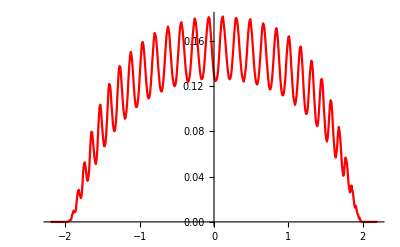

```mathematica
ListPlot[%1123,Joined->True,PlotStyle->Red]
```

```mathematica
25imps
```

```mathematica
Table[{ω,Mean[ParallelTable[TRA[ω,0,0],5000]]},{ω,Range[-2.2,2.2,0.01]}]
```

{{-2.2,1.39626×10^-52},{-2.19,1.25694×10^-51},{-2.18,1.30372×10^-50},{-2.17,1.48272×10^-49},{-2.16,1.86663×10^-48},{-2.15,2.99542×10^-47},{-2.14,6.50658×10^-46},{-2.13,2.44604×10^-44},{-2.12,3.26979×10^-40},{-2.11,4.14734×10^-39},{-2.1,2.93914×10^-39},{-2.09,3.70282×10^-38},{-2.08,8.35762×10^-38},{-2.07,2.55549×10^-35},{-2.06,1.07501×10^-34},{-2.05,5.38371×10^-34},{-2.04,6.06422×10^-33},{-2.03,4.09222×10^-32},{-2.02,1.19256×10^-30},{-2.01,2.97523×10^-29},{-2.,7.61785×10^-26},{-1.99,5.4538×10^-22},{-1.98,1.03191×10^-19},{-1.97,2.26361×10^-17},{-1.96,1.49118×10^-14},{-1.95,1.93269×10^-13},{-1.94,4.59614×10^-12},{-1.93,2.77241×10^-9},{-1.92,6.87608×10^-10},{-1.91,7.04909×10^-9},{-1.9,4.66816×10^-8},{-1.89,1.86167×10^-7},{-1.88,9.59117×10^-7},{-1.87,2.80121×10^-6},{-1.86,4.91782×10^-6},{-1.85,9.77894×10^-6},{-1.84,0.0000179813},{-1.83,0.0000306942},{-1.82,0.0000669137},{-1.81,0.0000893568},{-1.8,0.000123539},{-1.79,0.000228387},{-1.78,0.000300623},{-1.77,0.000393267},{-1.76,0.000479993},{-1.75,0.000630382},{-1.74,0.000719268},{-1.73,0.00109428},{-1.72,0.00122677},{-1.71,0.00160167},{-1.7,0.00177775},{-1.69,0.00215528},{-1.68,0.00247872},{-1.67,0.00300695},{-1.66,0.00329945},{-1.65,0.00349543},{-1.64,0.0039725},{-1.63,0.00427796},{-1.62,0.0048344},{-1.61,0.00512543},{-1.6,0.00588989},{-1.59,0.00664924},{-1.58,0.00753689},{-1.57,0.00780664},{-1.56,0.00860171},{-1.55,0.00885173},{-1.54,0.00945798},{-1.53,0.00972936},{-1.52,0.0101378},{-1.51,0.010864},{-1.5,0.0121012},{-1.49,0.012516},{-1.48,0.0136677},{-1.47,0.0149118},{-1.46,0.0155903},{-1.45,0.0161162},{-1.44,0.0173702},{-1.43,0.0170091},{-1.42,0.0176115},{-1.41,0.0176287},{-1.4,0.0177511},{-1.39,0.0183246},{-1.38,0.0193115},{-1.37,0.020229},{-1.36,0.022797},{-1.35,0.0245813},{-1.34,0.0249416},{-1.33,0.0257577},{-1.32,0.0266259},{-1.31,0.0266263},{-1.3,0.0265552},{-1.29,0.0267204},{-1.28,0.0266741},{-1.27,0.027131},{-1.26,0.0271323},{-1.25,0.0278703},{-1.24,0.0291728},{-1.23,0.0307699},{-1.22,0.0323957},{-1.21,0.0348278},{-1.2,0.0358715},{-1.19,0.0366257},{-1.18,0.0370574},{-1.17,0.0374223},{-1.16,0.0375298},{-1.15,0.0360901},{-1.14,0.0349883},{-1.13,0.0350136},{-1.12,0.035731},{-1.11,0.0363506},{-1.1,0.0376254},{-1.09,0.0395539},{-1.08,0.0416327},{-1.07,0.0429668},{-1.06,0.0442066},{-1.05,0.046196},{-1.04,0.0465271},{-1.03,0.0469619},{-1.02,0.0479019},{-1.01,0.0465918},{-1.,0.0454654},{-0.99,0.0446842},{-0.98,0.0437013},{-0.97,0.0434372},{-0.96,0.04432},{-0.95,0.0445807},{-0.94,0.0458314},{-0.93,0.0477713},{-0.92,0.0501204},{-0.91,0.0511317},{-0.9,0.0539539},{-0.89,0.0554179},{-0.88,0.0565846},{-0.87,0.0562939},{-0.86,0.0571104},{-0.85,0.0546814},{-0.84,0.0547371},{-0.83,0.0545889},{-0.82,0.0528027},{-0.81,0.0508791},{-0.8,0.050777},{-0.79,0.0517746},{-0.78,0.052555},{-0.77,0.0551003},{-0.76,0.0572853},{-0.75,0.0597677},{-0.74,0.0618007},{-0.73,0.0635404},{-0.72,0.0641421},{-0.71,0.0650337},{-0.7,0.0643681},{-0.69,0.0646139},{-0.68,0.0630389},{-0.67,0.0611967},{-0.66,0.0604696},{-0.65,0.0582717},{-0.64,0.0585775},{-0.63,0.0576489},{-0.62,0.0578123},{-0.61,0.0586036},{-0.6,0.0590897},{-0.59,0.0620729},{-0.58,0.0645204},{-0.57,0.0680513},{-0.56,0.068813},{-0.55,0.0704934},{-0.54,0.0721045},{-0.53,0.073051},{-0.52,0.0712089},{-0.51,0.0702823},{-0.5,0.0681856},{-0.49,0.0670557},{-0.48,0.0652384},{-0.47,0.0638203},{-0.46,0.0636302},{-0.45,0.0618798},{-0.44,0.061894},{-0.43,0.0627248},{-0.42,0.06504},{-0.41,0.0685105},{-0.4,0.0706425},{-0.39,0.0739133},{-0.38,0.0751745},{-0.37,0.074949},{-0.36,0.0770426},{-0.35,0.0775352},{-0.34,0.0767889},{-0.33,0.074365},{-0.32,0.0719994},{-0.31,0.0712737},{-0.3,0.0685616},{-0.29,0.0684003},{-0.28,0.0665128},{-0.27,0.0667866},{-0.26,0.0661959},{-0.25,0.0666077},{-0.24,0.0693311},{-0.23,0.071941},{-0.22,0.0733985},{-0.21,0.0761384},{-0.2,0.0776704},{-0.19,0.0793597},{-0.18,0.082031},{-0.17,0.080916},{-0.16,0.08007},{-0.15,0.0798575},{-0.14,0.0778306},{-0.13,0.0761619},{-0.12,0.0743491},{-0.11,0.0723493},{-0.1,0.07},{-0.09,0.068736},{-0.08,0.0677102},{-0.07,0.0686232},{-0.06,0.0698486},{-0.05,0.0728093},{-0.04,0.0737024},{-0.03,0.0778819},{-0.02,0.0793581},{-0.01,0.0810266},{0.,0.0831441},{0.01,0.0848301},{0.02,0.0841771},{0.03,0.0846943},{0.04,0.0823441},{0.05,0.0793737},{0.06,0.0779059},{0.07,0.0753417},{0.08,0.0742775},{0.09,0.0732742},{0.1,0.072486},{0.11,0.0721875},{0.12,0.0711883},{0.13,0.0730255},{0.14,0.0755665},{0.15,0.0773103},{0.16,0.0805723},{0.17,0.0835967},{0.18,0.0857134},{0.19,0.0864275},{0.2,0.0861537},{0.21,0.087054},{0.22,0.0853546},{0.23,0.0833133},{0.24,0.0817575},{0.25,0.0796572},{0.26,0.0755113},{0.27,0.0751634},{0.28,0.0707595},{0.29,0.0715732},{0.3,0.0715264},{0.31,0.070602},{0.32,0.0735815},{0.33,0.0745927},{0.34,0.0769841},{0.35,0.0790604},{0.36,0.0820771},{0.37,0.0852418},{0.38,0.0858267},{0.39,0.0865171},{0.4,0.0847268},{0.41,0.0821487},{0.42,0.081945},{0.43,0.078795},{0.44,0.074839},{0.45,0.07378},{0.46,0.0712631},{0.47,0.0698844},{0.48,0.0700712},{0.49,0.0684593},{0.5,0.0708636},{0.51,0.0713837},{0.52,0.0734638},{0.53,0.0756094},{0.54,0.0776495},{0.55,0.0814075},{0.56,0.0823955},{0.57,0.0835328},{0.58,0.0834353},{0.59,0.0791454},{0.6,0.0784041},{0.61,0.074604},{0.62,0.0725692},{0.63,0.0709319},{0.64,0.0693491},{0.65,0.0677617},{0.66,0.0660124},{0.67,0.0660623},{0.68,0.0671541},{0.69,0.0682828},{0.7,0.0705155},{0.71,0.0722695},{0.72,0.0746809},{0.73,0.0765292},{0.74,0.078097},{0.75,0.0789579},{0.76,0.0774752},{0.77,0.0764913},{0.78,0.0732052},{0.79,0.0723263},{0.8,0.0696168},{0.81,0.0669468},{0.82,0.065088},{0.83,0.0637149},{0.84,0.0627442},{0.85,0.0629224},{0.86,0.064036},{0.87,0.0653816},{0.88,0.0659981},{0.89,0.0680437},{0.9,0.0689314},{0.91,0.0708021},{0.92,0.0715704},{0.93,0.0703175},{0.94,0.070551},{0.95,0.0692268},{0.96,0.0661128},{0.97,0.0642329},{0.98,0.0630367},{0.99,0.059841},{1.,0.0573596},{1.01,0.0561274},{1.02,0.0566071},{1.03,0.0569261},{1.04,0.0583371},{1.05,0.0595228},{1.06,0.0622945},{1.07,0.0623507},{1.08,0.0641329},{1.09,0.0647211},{1.1,0.0628536},{1.11,0.0618824},{1.12,0.0600185},{1.13,0.0582825},{1.14,0.0553552},{1.15,0.0533375},{1.16,0.0527634},{1.17,0.0511154},{1.18,0.0503434},{1.19,0.0495529},{1.2,0.0508973},{1.21,0.0524915},{1.22,0.0535963},{1.23,0.0545764},{1.24,0.0548209},{1.25,0.05497},{1.26,0.054812},{1.27,0.0528235},{1.28,0.0517891},{1.29,0.0488488},{1.3,0.0471362},{1.31,0.0455745},{1.32,0.0437907},{1.33,0.0423029},{1.34,0.0429325},{1.35,0.0426349},{1.36,0.0440154},{1.37,0.0434106},{1.38,0.0439246},{1.39,0.0442426},{1.4,0.0434687},{1.41,0.0431444},{1.42,0.0426479},{1.43,0.0395258},{1.44,0.0387857},{1.45,0.0364008},{1.46,0.0356744},{1.47,0.0331202},{1.48,0.0336561},{1.49,0.0339055},{1.5,0.0336949},{1.51,0.0326007},{1.52,0.0336756},{1.53,0.0322174},{1.54,0.0312293},{1.55,0.0306676},{1.56,0.0300047},{1.57,0.0287526},{1.58,0.0268103},{1.59,0.0258581},{1.6,0.0246084},{1.61,0.0242812},{1.62,0.0236028},{1.63,0.0225432},{1.64,0.0227413},{1.65,0.0223273},{1.66,0.0212191},{1.67,0.0202626},{1.68,0.0193771},{1.69,0.0176737},{1.7,0.0161566},{1.71,0.0161471},{1.72,0.0151493},{1.73,0.0142003},{1.74,0.0133888},{1.75,0.0125174},{1.76,0.0119557},{1.77,0.0113794},{1.78,0.0101108},{1.79,0.00977182},{1.8,0.00838268},{1.81,0.00790637},{1.82,0.0069528},{1.83,0.00634966},{1.84,0.00575783},{1.85,0.00537161},{1.86,0.00429669},{1.87,0.00402548},{1.88,0.0034165},{1.89,0.00291346},{1.9,0.0025668},{1.91,0.00180773},{1.92,0.00145909},{1.93,0.00122348},{1.94,0.000959836},{1.95,0.00063024},{1.96,0.000383284},{1.97,0.000304642},{1.98,0.000183146},{1.99,0.0000887495},{2.,2.55127×10^-6},{2.01,8.69269×10^-9},{2.02,4.85417×10^-9},{2.03,5.56942×10^-9},{2.04,3.86487×10^-9},{2.05,8.64275×10^-10},{2.06,2.24956×10^-9},{2.07,9.83545×10^-11},{2.08,2.17278×10^-10},{2.09,1.98525×10^-12},{2.1,1.28636×10^-12},{2.11,5.1639×10^-13},{2.12,4.64054×10^-14},{2.13,2.09399×10^-14},{2.14,2.04716×10^-15},{2.15,5.21184×10^-15},{2.16,7.18125×10^-17},{2.17,3.9779×10^-17},{2.18,1.11898×10^-18},{2.19,1.03011×10^-19},{2.2,5.07603×10^-23}}

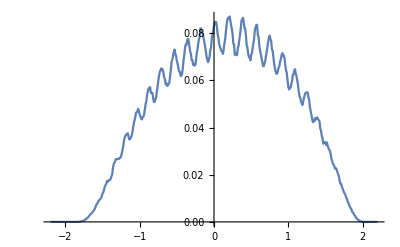

```mathematica
ListPlot[%1118,Joined->True]
```

```mathematica
15imps
```

```mathematica
Table[{ω,Mean[ParallelTable[TRA[ω,0,0],5000]]},{ω,Range[-2.2,2.2,0.01]}]
```

{{-2.2,1.07631×10^-49},{-2.19,1.17934×10^-48},{-2.18,1.41039×10^-47},{-2.17,1.91195×10^-46},{-2.16,3.12769×10^-45},{-2.15,6.19213×10^-44},{-2.14,1.91905×10^-42},{-2.13,1.48095×10^-40},{-2.12,4.28225×10^-35},{-2.11,1.34062×10^-35},{-2.1,2.95429×10^-35},{-2.09,2.71258×10^-35},{-2.08,1.20901×10^-34},{-2.07,7.80796×10^-31},{-2.06,2.38752×10^-31},{-2.05,7.33171×10^-31},{-2.04,5.0388×10^-30},{-2.03,5.83021×10^-29},{-2.02,5.14434×10^-27},{-2.01,6.97799×10^-25},{-2.,2.07093×10^-20},{-1.99,4.54522×10^-16},{-1.98,7.53217×10^-13},{-1.97,4.4556×10^-11},{-1.96,1.80901×10^-9},{-1.95,3.01323×10^-8},{-1.94,4.17201×10^-7},{-1.93,3.04532×10^-6},{-1.92,6.4379×10^-6},{-1.91,0.0000164575},{-1.9,0.0000428342},{-1.89,0.0000757653},{-1.88,0.000139033},{-1.87,0.000245341},{-1.86,0.000451681},{-1.85,0.000511564},{-1.84,0.00069281},{-1.83,0.00103023},{-1.82,0.001394},{-1.81,0.00171806},{-1.8,0.00228766},{-1.79,0.00283218},{-1.78,0.0032702},{-1.77,0.00357595},{-1.76,0.00398824},{-1.75,0.00476841},{-1.74,0.00560619},{-1.73,0.00684877},{-1.72,0.00800987},{-1.71,0.00909754},{-1.7,0.00941237},{-1.69,0.00998137},{-1.68,0.0101717},{-1.67,0.0111116},{-1.66,0.0115367},{-1.65,0.0130339},{-1.64,0.014554},{-1.63,0.0159742},{-1.62,0.0181446},{-1.61,0.0204958},{-1.6,0.0206957},{-1.59,0.020745},{-1.58,0.0207863},{-1.57,0.0205272},{-1.56,0.0208338},{-1.55,0.0216756},{-1.54,0.0231437},{-1.53,0.0254053},{-1.52,0.0275278},{-1.51,0.0308075},{-1.5,0.0329155},{-1.49,0.0341241},{-1.48,0.0339567},{-1.47,0.0336376},{-1.46,0.0325617},{-1.45,0.0316189},{-1.44,0.03229},{-1.43,0.0321809},{-1.42,0.0340396},{-1.41,0.0369382},{-1.4,0.039182},{-1.39,0.0431721},{-1.38,0.0460673},{-1.37,0.0481021},{-1.36,0.0490191},{-1.35,0.0489215},{-1.34,0.0479367},{-1.33,0.0452806},{-1.32,0.0441494},{-1.31,0.0435323},{-1.3,0.0431155},{-1.29,0.045518},{-1.28,0.0459441},{-1.27,0.0506223},{-1.26,0.0541427},{-1.25,0.0575033},{-1.24,0.0598985},{-1.23,0.0618886},{-1.22,0.0630191},{-1.21,0.0624288},{-1.2,0.0600009},{-1.19,0.0576866},{-1.18,0.0550357},{-1.17,0.0534509},{-1.16,0.0527401},{-1.15,0.0537307},{-1.14,0.0561163},{-1.13,0.0580885},{-1.12,0.0640227},{-1.11,0.0658925},{-1.1,0.0697883},{-1.09,0.072149},{-1.08,0.0755118},{-1.07,0.0744775},{-1.06,0.0740028},{-1.05,0.0710996},{-1.04,0.0691176},{-1.03,0.0657619},{-1.02,0.063811},{-1.01,0.0632758},{-1.,0.0623758},{-0.99,0.0628142},{-0.98,0.0657193},{-0.97,0.0688828},{-0.96,0.0737724},{-0.95,0.0778777},{-0.94,0.0818768},{-0.93,0.0844192},{-0.92,0.0856419},{-0.91,0.084956},{-0.9,0.083625},{-0.89,0.0814392},{-0.88,0.0789533},{-0.87,0.0755238},{-0.86,0.0730925},{-0.85,0.0712537},{-0.84,0.0703159},{-0.83,0.0716974},{-0.82,0.0730909},{-0.81,0.0760008},{-0.8,0.0792753},{-0.79,0.0837751},{-0.78,0.0880529},{-0.77,0.091768},{-0.76,0.0946804},{-0.75,0.0945577},{-0.74,0.0951533},{-0.73,0.0924654},{-0.72,0.0903134},{-0.71,0.0868128},{-0.7,0.0838185},{-0.69,0.0793454},{-0.68,0.0783332},{-0.67,0.0776916},{-0.66,0.0772679},{-0.65,0.0782469},{-0.64,0.0808436},{-0.63,0.0849474},{-0.62,0.0889026},{-0.61,0.0945823},{-0.6,0.0992807},{-0.59,0.101813},{-0.58,0.101881},{-0.57,0.101138},{-0.56,0.0995805},{-0.55,0.0977037},{-0.54,0.0953248},{-0.53,0.0912137},{-0.52,0.0881466},{-0.51,0.0846285},{-0.5,0.0829521},{-0.49,0.0818562},{-0.48,0.0826414},{-0.47,0.0841178},{-0.46,0.0872853},{-0.45,0.0911707},{-0.44,0.0974647},{-0.43,0.100195},{-0.42,0.104017},{-0.41,0.107076},{-0.4,0.106878},{-0.39,0.106765},{-0.38,0.104764},{-0.37,0.102354},{-0.36,0.0989102},{-0.35,0.0943657},{-0.34,0.092696},{-0.33,0.0895315},{-0.32,0.0868409},{-0.31,0.0855713},{-0.3,0.0859067},{-0.29,0.0871941},{-0.28,0.0903879},{-0.27,0.0935029},{-0.26,0.0978853},{-0.25,0.102779},{-0.24,0.107714},{-0.23,0.109644},{-0.22,0.110349},{-0.21,0.111903},{-0.2,0.109622},{-0.19,0.107047},{-0.18,0.103632},{-0.17,0.099832},{-0.16,0.0964276},{-0.15,0.092991},{-0.14,0.0907627},{-0.13,0.0877254},{-0.12,0.0884337},{-0.11,0.0892684},{-0.1,0.0908996},{-0.09,0.0950457},{-0.08,0.0972811},{-0.07,0.101962},{-0.06,0.105426},{-0.05,0.110725},{-0.04,0.111195},{-0.03,0.112045},{-0.02,0.111933},{-0.01,0.111024},{0.,0.108073},{0.01,0.104272},{0.02,0.0993188},{0.03,0.0959188},{0.04,0.0930051},{0.05,0.0906812},{0.06,0.0900427},{0.07,0.0896063},{0.08,0.0904046},{0.09,0.092795},{0.1,0.0952484},{0.11,0.0995002},{0.12,0.105434},{0.13,0.109464},{0.14,0.114152},{0.15,0.116361},{0.16,0.116782},{0.17,0.115858},{0.18,0.115009},{0.19,0.108437},{0.2,0.10578},{0.21,0.102318},{0.22,0.0975887},{0.23,0.0941999},{0.24,0.0921833},{0.25,0.0905381},{0.26,0.0916291},{0.27,0.0886995},{0.28,0.0919855},{0.29,0.0966717},{0.3,0.100522},{0.31,0.105234},{0.32,0.109405},{0.33,0.113182},{0.34,0.115072},{0.35,0.114367},{0.36,0.113275},{0.37,0.111321},{0.38,0.105315},{0.39,0.100832},{0.4,0.0974165},{0.41,0.0934261},{0.42,0.0910376},{0.43,0.0890462},{0.44,0.0880405},{0.45,0.0889039},{0.46,0.0899562},{0.47,0.0921978},{0.48,0.0967175},{0.49,0.100756},{0.5,0.10574},{0.51,0.110031},{0.52,0.112731},{0.53,0.113085},{0.54,0.110845},{0.55,0.106889},{0.56,0.105301},{0.57,0.100409},{0.58,0.0955136},{0.59,0.0929017},{0.6,0.0902579},{0.61,0.0856191},{0.62,0.0852249},{0.63,0.0868482},{0.64,0.0872942},{0.65,0.0888094},{0.66,0.092415},{0.67,0.0971386},{0.68,0.100203},{0.69,0.104574},{0.7,0.10754},{0.71,0.10654},{0.72,0.108093},{0.73,0.105209},{0.74,0.0996322},{0.75,0.0955786},{0.76,0.0909239},{0.77,0.0868688},{0.78,0.0839011},{0.79,0.0825329},{0.8,0.0826907},{0.81,0.081127},{0.82,0.0824043},{0.83,0.0852232},{0.84,0.0893549},{0.85,0.0944086},{0.86,0.0972599},{0.87,0.100355},{0.88,0.102664},{0.89,0.101683},{0.9,0.0992949},{0.91,0.0952345},{0.92,0.0901862},{0.93,0.0861252},{0.94,0.0822613},{0.95,0.0792058},{0.96,0.0751997},{0.97,0.0760052},{0.98,0.0748253},{0.99,0.0764001},{1.,0.0796972},{1.01,0.0828662},{1.02,0.086705},{1.03,0.0914056},{1.04,0.0914855},{1.05,0.093218},{1.06,0.0919357},{1.07,0.0889915},{1.08,0.0848551},{1.09,0.0814915},{1.1,0.0770772},{1.11,0.0723205},{1.12,0.0720847},{1.13,0.068364},{1.14,0.0687829},{1.15,0.0696931},{1.16,0.070781},{1.17,0.0741931},{1.18,0.0783583},{1.19,0.0798527},{1.2,0.0837021},{1.21,0.0813024},{1.22,0.0793385},{1.23,0.0793541},{1.24,0.0757885},{1.25,0.0709772},{1.26,0.0662409},{1.27,0.0625855},{1.28,0.0609153},{1.29,0.0593375},{1.3,0.0612339},{1.31,0.0619635},{1.32,0.0626331},{1.33,0.0676217},{1.34,0.0685183},{1.35,0.0690118},{1.36,0.0677147},{1.37,0.0681552},{1.38,0.064129},{1.39,0.062227},{1.4,0.0574818},{1.41,0.0541614},{1.42,0.0523151},{1.43,0.049529},{1.44,0.0502914},{1.45,0.0496732},{1.46,0.0531071},{1.47,0.053918},{1.48,0.0554353},{1.49,0.0552789},{1.5,0.0544371},{1.51,0.0507236},{1.52,0.0480798},{1.53,0.0464389},{1.54,0.0424678},{1.55,0.0409616},{1.56,0.0394705},{1.57,0.0373584},{1.58,0.0393745},{1.59,0.0391555},{1.6,0.0402404},{1.61,0.0396391},{1.62,0.0390788},{1.63,0.0370105},{1.64,0.0343296},{1.65,0.0325463},{1.66,0.0300883},{1.67,0.0277084},{1.68,0.0274703},{1.69,0.0265596},{1.7,0.0266012},{1.71,0.0259152},{1.72,0.0246099},{1.73,0.0237956},{1.74,0.0223442},{1.75,0.0202302},{1.76,0.0188354},{1.77,0.0178498},{1.78,0.0162461},{1.79,0.0154664},{1.8,0.0138292},{1.81,0.012935},{1.82,0.0127108},{1.83,0.010972},{1.84,0.00917239},{1.85,0.00807968},{1.86,0.00696519},{1.87,0.00610978},{1.88,0.00551057},{1.89,0.00448447},{1.9,0.00353585},{1.91,0.00302219},{1.92,0.00228415},{1.93,0.00171943},{1.94,0.00117528},{1.95,0.000733625},{1.96,0.000403607},{1.97,0.000249298},{1.98,0.0000889558},{1.99,0.0000326076},{2.,5.78516×10^-7},{2.01,2.91627×10^-10},{2.02,9.2071×10^-11},{2.03,7.07907×10^-11},{2.04,5.59357×10^-11},{2.05,5.73179×10^-11},{2.06,8.35233×10^-9},{2.07,2.05866×10^-12},{2.08,5.2453×10^-14},{2.09,4.0215×10^-15},{2.1,8.74864×10^-16},{2.11,3.66015×10^-17},{2.12,5.00008×10^-18},{2.13,7.71856×10^-17},{2.14,3.81297×10^-20},{2.15,2.95625×10^-22},{2.16,1.21601×10^-23},{2.17,9.96573×10^-24},{2.18,9.16518×10^-26},{2.19,4.39835×10^-27},{2.2,1.69651×10^-30}}

```mathematica
data=Table[{ω,TRA[ω,0,0]},{ω,Range[-2.2,2.2,0.01]}]
```

{{-2.2,4.87792×10^-50},{-2.19,5.73781×10^-49},{-2.18,4.07679×10^-48},{-2.17,6.88019×10^-47},{-2.16,1.29185×10^-45},{-2.15,3.02773×10^-44},{-2.14,2.91501×10^-43},{-2.13,9.831×10^-42},{-2.12,1.00699×10^-36},{-2.11,6.99331×10^-37},{-2.1,4.41712×10^-35},{-2.09,7.51044×10^-37},{-2.08,3.04283×10^-35},{-2.07,1.85944×10^-33},{-2.06,1.03752×10^-32},{-2.05,1.7947×10^-32},{-2.04,3.76909×10^-31},{-2.03,2.40019×10^-30},{-2.02,3.40394×10^-28},{-2.01,4.0611×10^-27},{-2.,7.7426×10^-21},{-1.99,6.12407×10^-18},{-1.98,1.50791×10^-15},{-1.97,1.10402×10^-14},{-1.96,1.31334×10^-12},{-1.95,2.91376×10^-10},{-1.94,3.04266×10^-8},{-1.93,7.48471×10^-6},{-1.92,5.84727×10^-8},{-1.91,5.12406×10^-6},{-1.9,0.0000112971},{-1.89,2.97892×10^-6},{-1.88,7.97524×10^-6},{-1.87,0.0000301026},{-1.86,0.0003649},{-1.85,9.81241×10^-6},{-1.84,0.0000546955},{-1.83,3.9805×10^-6},{-1.82,0.000145365},{-1.81,0.000410688},{-1.8,0.000247661},{-1.79,0.000374256},{-1.78,0.00122253},{-1.77,0.00174912},{-1.76,0.000600577},{-1.75,0.00111641},{-1.74,0.00257608},{-1.73,0.00321555},{-1.72,0.00533589},{-1.71,0.0265805},{-1.7,0.00474584},{-1.69,0.00201543},{-1.68,0.00340083},{-1.67,0.00412713},{-1.66,0.0000921812},{-1.65,0.0176994},{-1.64,0.000233934},{-1.63,0.00855087},{-1.62,0.00657007},{-1.61,0.00313198},{-1.6,0.0177622},{-1.59,0.0376758},{-1.58,0.0109922},{-1.57,0.00372118},{-1.56,0.00200533},{-1.55,0.0143079},{-1.54,0.0230021},{-1.53,0.0207137},{-1.52,0.00287428},{-1.51,0.032913},{-1.5,0.1664},{-1.49,0.0354828},{-1.48,0.0368198},{-1.47,0.00595423},{-1.46,0.0344449},{-1.45,0.0355014},{-1.44,0.0144902},{-1.43,0.0289871},{-1.42,0.0251901},{-1.41,0.0263202},{-1.4,0.0779007},{-1.39,0.0405265},{-1.38,0.0400091},{-1.37,0.0315504},{-1.36,0.0151611},{-1.35,0.0708281},{-1.34,0.0598879},{-1.33,0.0686054},{-1.32,0.0808047},{-1.31,0.0883926},{-1.3,0.0681321},{-1.29,0.0316426},{-1.28,0.034711},{-1.27,0.0179158},{-1.26,0.105249},{-1.25,0.052518},{-1.24,0.0233016},{-1.23,0.11132},{-1.22,0.0266546},{-1.21,0.0514749},{-1.2,0.095386},{-1.19,0.0632705},{-1.18,0.0379819},{-1.17,0.0231483},{-1.16,0.0629704},{-1.15,0.0341822},{-1.14,0.0377071},{-1.13,0.121737},{-1.12,0.0160834},{-1.11,0.0445355},{-1.1,0.0915384},{-1.09,0.101712},{-1.08,0.0705512},{-1.07,0.118905},{-1.06,0.0972839},{-1.05,0.0620606},{-1.04,0.0289194},{-1.03,0.0183925},{-1.02,0.126207},{-1.01,0.174393},{-1.,0.0740476},{-0.99,0.030809},{-0.98,0.01935},{-0.97,0.0201529},{-0.96,0.0932067},{-0.95,0.0783279},{-0.94,0.0886983},{-0.93,0.0226277},{-0.92,0.0594146},{-0.91,0.0675674},{-0.9,0.0868181},{-0.89,0.0595442},{-0.88,0.0300938},{-0.87,0.0663805},{-0.86,0.0900412},{-0.85,0.0356748},{-0.84,0.0381025},{-0.83,0.0350064},{-0.82,0.0510192},{-0.81,0.054959},{-0.8,0.0433557},{-0.79,0.133087},{-0.78,0.0677525},{-0.77,0.0698469},{-0.76,0.131351},{-0.75,0.0881899},{-0.74,0.109398},{-0.73,0.0555067},{-0.72,0.0808453},{-0.71,0.174316},{-0.7,0.0963844},{-0.69,0.0452301},{-0.68,0.109875},{-0.67,0.0746863},{-0.66,0.110578},{-0.65,0.0633286},{-0.64,0.0762261},{-0.63,0.0794832},{-0.62,0.110864},{-0.61,0.0319754},{-0.6,0.0760226},{-0.59,0.112401},{-0.58,0.0573841},{-0.57,0.0679149},{-0.56,0.0455383},{-0.55,0.101245},{-0.54,0.0528968},{-0.53,0.0407433},{-0.52,0.0470853},{-0.51,0.0330925},{-0.5,0.0457248},{-0.49,0.124481},{-0.48,0.0548468},{-0.47,0.0692485},{-0.46,0.0637982},{-0.45,0.0686367},{-0.44,0.204031},{-0.43,0.0917221},{-0.42,0.109978},{-0.41,0.0982677},{-0.4,0.0820612},{-0.39,0.0636197},{-0.38,0.176431},{-0.37,0.051426},{-0.36,0.165221},{-0.35,0.109297},{-0.34,0.113728},{-0.33,0.0893818},{-0.32,0.0506407},{-0.31,0.0627226},{-0.3,0.073333},{-0.29,0.0652172},{-0.28,0.0944922},{-0.27,0.0565567},{-0.26,0.0757511},{-0.25,0.0503571},{-0.24,0.075173},{-0.23,0.154978},{-0.22,0.175389},{-0.21,0.107555},{-0.2,0.137436},{-0.19,0.118878},{-0.18,0.0529698},{-0.17,0.0808459},{-0.16,0.239623},{-0.15,0.0573006},{-0.14,0.0765882},{-0.13,0.0830429},{-0.12,0.128633},{-0.11,0.171756},{-0.1,0.137074},{-0.09,0.0843677},{-0.08,0.0461537},{-0.07,0.0780628},{-0.06,0.140432},{-0.05,0.094847},{-0.04,0.104879},{-0.03,0.0678861},{-0.02,0.0745544},{-0.01,0.0955757},{0.,0.0891296},{0.01,0.112353},{0.02,0.102149},{0.03,0.0574868},{0.04,0.122828},{0.05,0.106834},{0.06,0.0456782},{0.07,0.0317309},{0.08,0.0600292},{0.09,0.0794873},{0.1,0.0755927},{0.11,0.081453},{0.12,0.0762411},{0.13,0.0641967},{0.14,0.11437},{0.15,0.138952},{0.16,0.0936899},{0.17,0.131888},{0.18,0.087594},{0.19,0.0618815},{0.2,0.054171},{0.21,0.107583},{0.22,0.115418},{0.23,0.0514612},{0.24,0.0794262},{0.25,0.0787713},{0.26,0.0565259},{0.27,0.0745657},{0.28,0.0961732},{0.29,0.104628},{0.3,0.146332},{0.31,0.121766},{0.32,0.0727561},{0.33,0.0641758},{0.34,0.20268},{0.35,0.0485863},{0.36,0.0670189},{0.37,0.174909},{0.38,0.056526},{0.39,0.0539012},{0.4,0.133893},{0.41,0.213554},{0.42,0.0957666},{0.43,0.074193},{0.44,0.13723},{0.45,0.105207},{0.46,0.0473621},{0.47,0.0201679},{0.48,0.0453551},{0.49,0.0611472},{0.5,0.152332},{0.51,0.121632},{0.52,0.112401},{0.53,0.124998},{0.54,0.0596049},{0.55,0.0976793},{0.56,0.0902189},{0.57,0.119833},{0.58,0.0983681},{0.59,0.0430542},{0.6,0.0969076},{0.61,0.0438249},{0.62,0.0372994},{0.63,0.0690282},{0.64,0.0422665},{0.65,0.0621739},{0.66,0.0430236},{0.67,0.086308},{0.68,0.0764277},{0.69,0.12258},{0.7,0.261919},{0.71,0.0369079},{0.72,0.100276},{0.73,0.115379},{0.74,0.0734137},{0.75,0.0925801},{0.76,0.0433664},{0.77,0.0772923},{0.78,0.142323},{0.79,0.125966},{0.8,0.0532614},{0.81,0.122024},{0.82,0.087537},{0.83,0.0519196},{0.84,0.103127},{0.85,0.0895118},{0.86,0.0664472},{0.87,0.146245},{0.88,0.0618091},{0.89,0.0628537},{0.9,0.0808785},{0.91,0.061311},{0.92,0.0643426},{0.93,0.0317834},{0.94,0.0249208},{0.95,0.129242},{0.96,0.073155},{0.97,0.049182},{0.98,0.0935634},{0.99,0.143056},{1.,0.163676},{1.01,0.0304828},{1.02,0.145788},{1.03,0.0858773},{1.04,0.0879968},{1.05,0.0932707},{1.06,0.0425538},{1.07,0.049755},{1.08,0.0464095},{1.09,0.0528334},{1.1,0.170316},{1.11,0.0909713},{1.12,0.070216},{1.13,0.0674314},{1.14,0.050275},{1.15,0.0169932},{1.16,0.0373582},{1.17,0.0973529},{1.18,0.0652672},{1.19,0.109483},{1.2,0.10167},{1.21,0.0390682},{1.22,0.0369418},{1.23,0.0538457},{1.24,0.112027},{1.25,0.0412134},{1.26,0.1468},{1.27,0.036932},{1.28,0.0450338},{1.29,0.0200248},{1.3,0.0757599},{1.31,0.0123312},{1.32,0.134},{1.33,0.0184613},{1.34,0.0762015},{1.35,0.0515849},{1.36,0.134952},{1.37,0.0812979},{1.38,0.242092},{1.39,0.0469486},{1.4,0.094622},{1.41,0.0121915},{1.42,0.0131689},{1.43,0.0948775},{1.44,0.0668401},{1.45,0.0171974},{1.46,0.0719735},{1.47,0.0297509},{1.48,0.0493561},{1.49,0.0703637},{1.5,0.128021},{1.51,0.0718268},{1.52,0.0769517},{1.53,0.113559},{1.54,0.0137497},{1.55,0.0231276},{1.56,0.0134217},{1.57,0.019018},{1.58,0.0457134},{1.59,0.00224467},{1.6,0.00222013},{1.61,0.00726622},{1.62,0.0104958},{1.63,0.0306044},{1.64,0.00890878},{1.65,0.0710469},{1.66,0.0137041},{1.67,0.0666372},{1.68,0.0205275},{1.69,0.0486505},{1.7,0.0150115},{1.71,0.128407},{1.72,0.00800445},{1.73,0.00281456},{1.74,0.024218},{1.75,0.010224},{1.76,0.00440931},{1.77,0.0266928},{1.78,0.0217459},{1.79,0.00802563},{1.8,0.00473283},{1.81,0.000321564},{1.82,0.00425929},{1.83,0.00135211},{1.84,0.00187478},{1.85,0.00368028},{1.86,0.0238167},{1.87,0.000381495},{1.88,0.00054878},{1.89,0.000519886},{1.9,0.000051282},{1.91,0.00249864},{1.92,0.000458593},{1.93,0.00516276},{1.94,0.0000530488},{1.95,0.000413702},{1.96,8.33269×10^-7},{1.97,6.18317×10^-7},{1.98,4.32011×10^-6},{1.99,4.56429×10^-7},{2.,1.63461×10^-10},{2.01,4.16795×10^-12},{2.02,1.08891×10^-12},{2.03,1.09762×10^-15},{2.04,1.53921×10^-12},{2.05,1.45734×10^-14},{2.06,2.35421×10^-14},{2.07,8.808×10^-20},{2.08,1.94334×10^-16},{2.09,9.20655×10^-19},{2.1,2.61595×10^-21},{2.11,3.87215×10^-21},{2.12,6.93747×10^-21},{2.13,5.44535×10^-19},{2.14,4.76019×10^-25},{2.15,8.24832×10^-25},{2.16,1.35439×10^-27},{2.17,9.98876×10^-24},{2.18,3.33593×10^-31},{2.19,9.21786×10^-33},{2.2,8.97749×10^-32}}

```mathematica
Interpolation[Transpose[data-%1123][[2]]]
```

InterpolatingFunction[…]

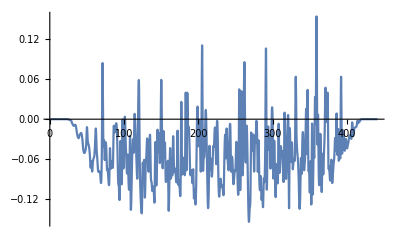

```mathematica
Plot[%1179[x],{x,1.,441.}]
```

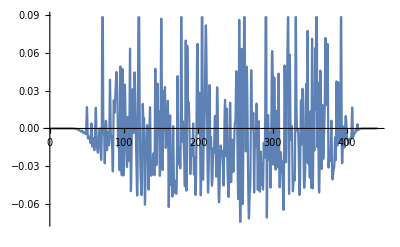

```mathematica
Plot[%1177[x],{x,1.,441.}]
```

```mathematica
mis25=NIntegrate[Abs[Interpolation[Transpose[data-%1118][[2]]][ω]],{ω,1,441}]
mis15=NIntegrate[Abs[Interpolation[Transpose[data-%1111][[2]]][ω]],{ω,1,441}]
mis5=NIntegrate[Abs[Interpolation[Transpose[data-%1123][[2]]][ω]],{ω,1,441}]
```

10.0295

9.44085

21.7385

```mathematica
Σ1[ω_]:=TRA[ω,0,0.3]+TRA[ω,0,0.2]+TRA[ω,0.1,0.2]+TRA[ω,0.1,0.3]
```

```mathematica
Σ2[ω_]:=TRA[ω,0.2,0]+TRA[ω,0.2,0.1]+TRA[ω,0.3,0.1]+TRA[ω,0.3,0]
```

```mathematica
α11[ω_]:=((TRA[ω,0,0.1]+TRA[ω,0,0.2]+TRA[ω,0,0.3])*Σ1[ω]-(TRA[ω,0,0.2]+TRA[ω,0,0.3])*(TRA[ω,0,0.1]-TRA[ω,0.1,0]+TRA[ω,0,0.2]+TRA[ω,0,0.3]))/Σ1[ω]
```

```mathematica
α22[ω_]:=((TRA[ω,0.2,0]+TRA[ω,0.2,0.1]+TRA[ω,0.2,0.3])*Σ2[ω]-(TRA[ω,0.2,0]+TRA[ω,0.2,0.1])*(TRA[ω,0.2,0]+TRA[ω,0.2,0.1]+TRA[ω,0.2,0.3]-TRA[ω,0.3,0.2]))/Σ2[ω]
```

```mathematica
α12[ω_]:= ((TRA[ω,0,0.2]+TRA[ω,0.1,0.3])-(TRA[ω,0,0.3]+TRA[ω,0.1,0.2]))/Σ1[ω]
```

```mathematica
α21[ω_]:= ((TRA[ω,0.2,0]+TRA[ω,0.3,0.2])-(TRA[ω,0.3,0]+TRA[ω,0.2,0.1]))/Σ2[ω]
```

```mathematica
R1212[ω_]:=2α22[ω]/(α11[ω]*α22[ω]-α12[ω]*α21[ω])//Abs
```

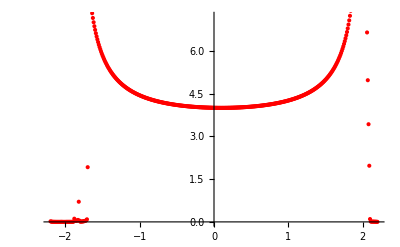

```mathematica
ListPlot[Table[{ω,R1212[ω]},{ω,Range[-2.2,2.2,0.01]}],PlotStyle->Red]
```

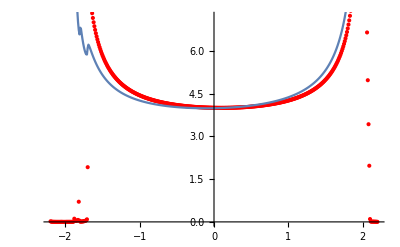

```mathematica
Show[ListPlot[Table[{ω,R1212[ω]},{ω,Range[-2.2,2.2,0.01]}],PlotStyle->Red],ListLinePlot[Table[{ω,1/TRA[ω]},{ω,Range[-2.2,2.2,0.01]}]]]
```